# Supplementary Computational Data: Supporting evidence, calculations, symbolic manipulations, and other numerical data for Maxie D. Schmidt’s article proving a few proposed new lower bounds on the Mertens function, M(x).

## ▶ Author: Maxie Dion Schmidt ▶ Source: https://github.com/maxieds/MertensFunctionCalculations ▶ Revision: 2020.08.05-v1

## File Contents Description: This file contains computational data related to the Dirichlet inverse function, g^-1. This includes generation of tables, verification of some identities for small n, and definitions and tables of auxiliary sequences.

# Custom Mathematica function definitions (**load these first**):

```mathematica
Clear[eps,Radix,Mertens,GInv,hmValues,sols,kCvl,ek,hinv,PrimesN]
eps[p_,n_]:=With[{pexp=Select[FactorInteger[n],#[[1]]==p&]},If[pexp≠{},pexp[[1]][[2]],0]]
Radix[n_]:=Times@@Map[First,FactorInteger[n]]
Mertens[x_]:=Mertens[x]=Sum[MoebiusMu[n],{n,1,x}]
GInv[x_]:=GInv[x]=If[x==1,h[1]/.hmValues,GInv[x-1]+(h[x]/.hmValues)]
(********)
nupper=5000;
sols=Table[DivisorSum[n,(PrimeNu[#]+1)h[n/#]&]==If[n==1,1,0], {n,1,nupper}] // Solve;
hmValues=Table[h[m]->(h[m]/.sols[[1]]/.(f[d_]->PrimeNu[d])),{m,1,nupper}];
(********)
kCvl[k_,n_,f_]:=If[k<=0,If[k==0,If[n==1,1,0],0],DivisorSum[n,kCvl[k-1,n/#,f]f[#]&]]
ek[k_,n_]:=SeriesCoefficient[Product[1+xi*z,{xi,Map[Last,FactorInteger[n]]}],{z,0,k}]
hinv[x_]:=DivisorSum[x,h[#]&]/.hmValues
PrimesN[n_]:=Select[Range[1,n],PrimeQ]
```

## Calculation of the inverse sequence, and sources of the LATEX table in the article.

```mathematica
nupper=300;
Table[{n,Apply[Times,Map[Superscript[#1[[1]],#1[[2]]]&,FactorInteger[n]]],SquareFreeQ[n]/.(True->"Y")/.(False->"N"),PrimePowerQ[n]/.(True->"Y")/.(False->"N"),h[n]/.hmValues,(LiouvilleLambda[n]*h[n]-Sum[Binomial[PrimeNu[n],k]Factorial[k],{k,0,PrimeNu[n]}])/.hmValues,(LiouvilleLambda[n]*h[n]-Sum[Binomial[PrimeOmega[n],k]Factorial[k],{k,0,PrimeOmega[n]}])/.hmValues,N[(DivisorSum[n,kCvl[PrimeOmega[#],#,PrimeNu]&]/Abs[h[n]])/.hmValues,8],N[1/n Length[Select[Range[1,n],LiouvilleLambda[#]===1&]],6],N[1/n Length[Select[Range[1,n],LiouvilleLambda[#]===-1&]],6],Sum[h[m]/.hmValues,{m,1,n}],N[GInv[n]/Sum[If[SquareFreeQ[m],(h[m]/.hmValues),0],{m,1,n}]*Zeta[2]],Sum[If[(h[m]/.hmValues)>0,h[m]/.hmValues,0],{m,1,n}],Sum[If[(h[m]<0)/.hmValues,h[m]/.hmValues,0]/.hmValues,{m,1,n}]},{n,2,nupper}] // TableForm
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

2 | 2^1 | Y | Y | -2 | 0 | 0 | 1. | 0.5 | 0.5 | -1 | 1.64493 | 1 | -2
3 | 3^1 | Y | Y | -2 | 0 | 0 | 1. | 0.333333 | 0.666667 | -3 | 1.64493 | 1 | -4
4 | 2^2 | N | Y | 2 | 0 | -3 | 1.5 | 0.5 | 0.5 | -1 | 0.548311 | 3 | -4
5 | 5^1 | Y | Y | -2 | 0 | 0 | 1. | 0.4 | 0.6 | -3 | 0.98696 | 3 | -6
6 | 2^1 3^1 | Y | N | 5 | 0 | 0 | 1. | 0.5 | 0.5 | 2 | ComplexInfinity | 8 | -6
7 | 7^1 | Y | Y | -2 | 0 | 0 | 1. | 0.428571 | 0.571429 | 0 | 0. | 8 | -8
8 | 2^3 | N | Y | -2 | 0 | -14 | 2. | 0.375 | 0.625 | -2 | 1.64493 | 8 | -10
9 | 3^2 | N | Y | 2 | 0 | -3 | 1.5 | 0.444444 | 0.555556 | 0 | 0. | 10 | -10
10 | 2^1 5^1 | Y | N | 5 | 0 | 0 | 1. | 0.5 | 0.5 | 5 | 2.74156 | 15 | -10
11 | 11^1 | Y | Y | -2 | 0 | 0 | 1. | 0.454545 | 0.545455 | 3 | 4.9348 | 15 | -12
12 | 2^2 3^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.416667 | 0.583333 | -4 | -6.57974 | 15 | -19
13 | 13^1 | Y | Y | -2 | 0 | 0 | 1. | 0.384615 | 0.615385 | -6 | 9.8696 | 15 | -21
14 | 2^1 7^1 | Y | N | 5 | 0 | 0 | 1. | 0.428571 | 0.571429 | -1 | -0.411234 | 20 | -21
15 | 3^1 5^1 | Y | N | 5 | 0 | 0 | 1. | 0.466667 | 0.533333 | 4 | 0.731082 | 25 | -21
16 | 2^4 | N | Y | 2 | 0 | -63 | 2.5 | 0.5 | 0.5 | 6 | 1.09662 | 27 | -21
17 | 17^1 | Y | Y | -2 | 0 | 0 | 1. | 0.470588 | 0.529412 | 4 | 0.939962 | 27 | -23
18 | 2^1 3^2 | N | N | -7 | 2 | -9 | 1.2857143 | 0.444444 | 0.555556 | -3 | -0.704972 | 27 | -30
19 | 19^1 | Y | Y | -2 | 0 | 0 | 1. | 0.421053 | 0.578947 | -5 | -1.64493 | 27 | -32
20 | 2^2 5^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.4 | 0.6 | -12 | -3.94784 | 27 | -39
21 | 3^1 7^1 | Y | N | 5 | 0 | 0 | 1. | 0.428571 | 0.571429 | -7 | -1.15145 | 32 | -39
22 | 2^1 11^1 | Y | N | 5 | 0 | 0 | 1. | 0.454545 | 0.545455 | -2 | -0.219325 | 37 | -39
23 | 23^1 | Y | Y | -2 | 0 | 0 | 1. | 0.434783 | 0.565217 | -4 | -0.506134 | 37 | -41
24 | 2^3 3^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.458333 | 0.541667 | 5 | 0.632667 | 46 | -41
25 | 5^2 | N | Y | 2 | 0 | -3 | 1.5 | 0.48 | 0.52 | 7 | 0.885734 | 48 | -41
26 | 2^1 13^1 | Y | N | 5 | 0 | 0 | 1. | 0.5 | 0.5 | 12 | 1.09662 | 53 | -41
27 | 3^3 | N | Y | -2 | 0 | -14 | 2. | 0.481481 | 0.518519 | 10 | 0.913852 | 53 | -43
28 | 2^2 7^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.464286 | 0.535714 | 3 | 0.274156 | 53 | -50
29 | 29^1 | Y | Y | -2 | 0 | 0 | 1. | 0.448276 | 0.551724 | 1 | 0.102808 | 53 | -52
30 | 2^1 3^1 5^1 | Y | N | -16 | 0 | 0 | 1. | 0.433333 | 0.566667 | -15 | ComplexInfinity | 53 | -68
31 | 31^1 | Y | Y | -2 | 0 | 0 | 1. | 0.419355 | 0.580645 | -17 | 13.9819 | 53 | -70
32 | 2^5 | N | Y | -2 | 0 | -324 | 3. | 0.40625 | 0.59375 | -19 | 15.6269 | 53 | -72
33 | 3^1 11^1 | Y | N | 5 | 0 | 0 | 1. | 0.424242 | 0.575758 | -14 | -7.67636 | 58 | -72
34 | 2^1 17^1 | Y | N | 5 | 0 | 0 | 1. | 0.441176 | 0.558824 | -9 | -1.85055 | 63 | -72
35 | 5^1 7^1 | Y | N | 5 | 0 | 0 | 1. | 0.457143 | 0.542857 | -4 | -0.506134 | 68 | -72
36 | 2^2 3^2 | N | N | 14 | 9 | -51 | 1.3571429 | 0.472222 | 0.527778 | 10 | 1.26533 | 82 | -72
37 | 37^1 | Y | Y | -2 | 0 | 0 | 1. | 0.459459 | 0.540541 | 8 | 1.19632 | 82 | -74
38 | 2^1 19^1 | Y | N | 5 | 0 | 0 | 1. | 0.473684 | 0.526316 | 13 | 1.33651 | 87 | -74
39 | 3^1 13^1 | Y | N | 5 | 0 | 0 | 1. | 0.487179 | 0.512821 | 18 | 1.40994 | 92 | -74
40 | 2^3 5^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.5 | 0.5 | 27 | 2.11492 | 101 | -74
41 | 41^1 | Y | Y | -2 | 0 | 0 | 1. | 0.487805 | 0.512195 | 25 | 2.16439 | 101 | -76
42 | 2^1 3^1 7^1 | Y | N | -16 | 0 | 0 | 1. | 0.47619 | 0.52381 | 9 | 4.9348 | 101 | -92
43 | 43^1 | Y | Y | -2 | 0 | 0 | 1. | 0.465116 | 0.534884 | 7 | 11.5145 | 101 | -94
44 | 2^2 11^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.454545 | 0.545455 | 0 | 0. | 101 | -101
45 | 3^2 5^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.444444 | 0.555556 | -7 | -11.5145 | 101 | -108
46 | 2^1 23^1 | Y | N | 5 | 0 | 0 | 1. | 0.456522 | 0.543478 | -2 | -0.548311 | 106 | -108
47 | 47^1 | Y | Y | -2 | 0 | 0 | 1. | 0.446809 | 0.553191 | -4 | -1.64493 | 106 | -110
48 | 2^4 3^1 | N | N | -11 | 6 | -315 | 1.8181818 | 0.4375 | 0.5625 | -15 | -6.1685 | 106 | -121
49 | 7^2 | N | Y | 2 | 0 | -3 | 1.5 | 0.44898 | 0.55102 | -13 | -5.34604 | 108 | -121
50 | 2^1 5^2 | N | N | -7 | 2 | -9 | 1.2857143 | 0.44 | 0.56 | -20 | -8.22467 | 108 | -128
51 | 3^1 17^1 | Y | N | 5 | 0 | 0 | 1. | 0.45098 | 0.54902 | -15 | -2.74156 | 113 | -128
52 | 2^2 13^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.442308 | 0.557692 | -22 | -4.02095 | 113 | -135
53 | 53^1 | Y | Y | -2 | 0 | 0 | 1. | 0.433962 | 0.566038 | -24 | -5.63977 | 113 | -137
54 | 2^1 3^3 | N | N | 9 | 4 | -56 | 1.5555556 | 0.444444 | 0.555556 | -15 | -3.52486 | 122 | -137
55 | 5^1 11^1 | Y | N | 5 | 0 | 0 | 1. | 0.454545 | 0.545455 | -10 | -1.37078 | 127 | -137
56 | 2^3 7^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.464286 | 0.535714 | -1 | -0.137078 | 136 | -137
57 | 3^1 19^1 | Y | N | 5 | 0 | 0 | 1. | 0.473684 | 0.526316 | 4 | 0.387043 | 141 | -137
58 | 2^1 29^1 | Y | N | 5 | 0 | 0 | 1. | 0.482759 | 0.517241 | 9 | 0.672928 | 146 | -137
59 | 59^1 | Y | Y | -2 | 0 | 0 | 1. | 0.474576 | 0.525424 | 7 | 0.575727 | 146 | -139
60 | 2^2 3^1 5^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.483333 | 0.516667 | 37 | 3.04313 | 176 | -139
61 | 61^1 | Y | Y | -2 | 0 | 0 | 1. | 0.47541 | 0.52459 | 35 | 3.19848 | 176 | -141
62 | 2^1 31^1 | Y | N | 5 | 0 | 0 | 1. | 0.483871 | 0.516129 | 40 | 2.86075 | 181 | -141
63 | 3^2 7^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.47619 | 0.52381 | 33 | 2.36012 | 181 | -148
64 | 2^6 | N | Y | 2 | 0 | -1955 | 3.5 | 0.484375 | 0.515625 | 35 | 2.50316 | 183 | -148
65 | 5^1 13^1 | Y | N | 5 | 0 | 0 | 1. | 0.492308 | 0.507692 | 40 | 2.34991 | 188 | -148
66 | 2^1 3^1 11^1 | Y | N | -16 | 0 | 0 | 1. | 0.484848 | 0.515152 | 24 | 3.28987 | 188 | -164
67 | 67^1 | Y | Y | -2 | 0 | 0 | 1. | 0.477612 | 0.522388 | 22 | 3.61885 | 188 | -166
68 | 2^2 17^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.470588 | 0.529412 | 15 | 2.4674 | 188 | -173
69 | 3^1 23^1 | Y | N | 5 | 0 | 0 | 1. | 0.478261 | 0.521739 | 20 | 2.19325 | 193 | -173
70 | 2^1 5^1 7^1 | Y | N | -16 | 0 | 0 | 1. | 0.471429 | 0.528571 | 4 | -6.57974 | 193 | -189
71 | 71^1 | Y | Y | -2 | 0 | 0 | 1. | 0.464789 | 0.535211 | 2 | -1.09662 | 193 | -191
72 | 2^3 3^2 | N | N | -23 | 18 | -303 | 1.4782609 | 0.458333 | 0.541667 | -21 | 11.5145 | 193 | -214
73 | 73^1 | Y | Y | -2 | 0 | 0 | 1. | 0.452055 | 0.547945 | -23 | 7.5667 | 193 | -216
74 | 2^1 37^1 | Y | N | 5 | 0 | 0 | 1. | 0.459459 | 0.540541 | -18 | ComplexInfinity | 198 | -216
75 | 3^1 5^2 | N | N | -7 | 2 | -9 | 1.2857143 | 0.453333 | 0.546667 | -25 | ComplexInfinity | 198 | -223
76 | 2^2 19^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.447368 | 0.552632 | -32 | ComplexInfinity | 198 | -230
77 | 7^1 11^1 | Y | N | 5 | 0 | 0 | 1. | 0.454545 | 0.545455 | -27 | -8.88264 | 203 | -230
78 | 2^1 3^1 13^1 | Y | N | -16 | 0 | 0 | 1. | 0.448718 | 0.551282 | -43 | 6.4302 | 203 | -246
79 | 79^1 | Y | Y | -2 | 0 | 0 | 1. | 0.443038 | 0.556962 | -45 | 5.694 | 203 | -248
80 | 2^4 5^1 | N | N | -11 | 6 | -315 | 1.8181818 | 0.4375 | 0.5625 | -56 | 7.08587 | 203 | -259
81 | 3^4 | N | Y | 2 | 0 | -63 | 2.5 | 0.444444 | 0.555556 | -54 | 6.8328 | 205 | -259
82 | 2^1 41^1 | Y | N | 5 | 0 | 0 | 1. | 0.45122 | 0.54878 | -49 | 10.0752 | 210 | -259
83 | 83^1 | Y | Y | -2 | 0 | 0 | 1. | 0.445783 | 0.554217 | -51 | 8.38916 | 210 | -261
84 | 2^2 3^1 7^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.452381 | 0.547619 | -21 | 3.45436 | 240 | -261
85 | 5^1 17^1 | Y | N | 5 | 0 | 0 | 1. | 0.458824 | 0.541176 | -16 | 5.26379 | 245 | -261
86 | 2^1 43^1 | Y | N | 5 | 0 | 0 | 1. | 0.465116 | 0.534884 | -11 | ComplexInfinity | 250 | -261
87 | 3^1 29^1 | Y | N | 5 | 0 | 0 | 1. | 0.471264 | 0.528736 | -6 | -1.97392 | 255 | -261
88 | 2^3 11^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.477273 | 0.522727 | 3 | 0.98696 | 264 | -261
89 | 89^1 | Y | Y | -2 | 0 | 0 | 1. | 0.47191 | 0.52809 | 1 | 0.548311 | 264 | -263
90 | 2^1 3^2 5^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.477778 | 0.522222 | 31 | 16.9977 | 294 | -263
91 | 7^1 13^1 | Y | N | 5 | 0 | 0 | 1. | 0.483516 | 0.516484 | 36 | 7.4022 | 299 | -263
92 | 2^2 23^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.478261 | 0.521739 | 29 | 5.96289 | 299 | -270
93 | 3^1 31^1 | Y | N | 5 | 0 | 0 | 1. | 0.483871 | 0.516129 | 34 | 4.30214 | 304 | -270
94 | 2^1 47^1 | Y | N | 5 | 0 | 0 | 1. | 0.489362 | 0.510638 | 39 | 3.56402 | 309 | -270
95 | 5^1 19^1 | Y | N | 5 | 0 | 0 | 1. | 0.494737 | 0.505263 | 44 | 3.14683 | 314 | -270
96 | 2^5 3^1 | N | N | 13 | 8 | -1944 | 2.0769231 | 0.5 | 0.5 | 57 | 4.07658 | 327 | -270
97 | 97^1 | Y | Y | -2 | 0 | 0 | 1. | 0.494845 | 0.505155 | 55 | 4.30816 | 327 | -272
98 | 2^1 7^2 | N | N | -7 | 2 | -9 | 1.2857143 | 0.489796 | 0.510204 | 48 | 3.75985 | 327 | -279
99 | 3^2 11^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.484848 | 0.515152 | 41 | 3.21154 | 327 | -286
100 | 2^2 5^2 | N | N | 14 | 9 | -51 | 1.3571429 | 0.49 | 0.51 | 55 | 4.30816 | 341 | -286
101 | 101^1 | Y | Y | -2 | 0 | 0 | 1. | 0.485149 | 0.514851 | 53 | 4.5885 | 341 | -288
102 | 2^1 3^1 17^1 | Y | N | -16 | 0 | 0 | 1. | 0.480392 | 0.519608 | 37 | 20.2875 | 341 | -304
103 | 103^1 | Y | Y | -2 | 0 | 0 | 1. | 0.475728 | 0.524272 | 35 | 57.5727 | 341 | -306
104 | 2^3 13^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.480769 | 0.519231 | 44 | 72.3771 | 350 | -306
105 | 3^1 5^1 7^1 | Y | N | -16 | 0 | 0 | 1. | 0.47619 | 0.52381 | 28 | -3.07054 | 350 | -322
106 | 2^1 53^1 | Y | N | 5 | 0 | 0 | 1. | 0.481132 | 0.518868 | 33 | -5.42828 | 355 | -322
107 | 107^1 | Y | Y | -2 | 0 | 0 | 1. | 0.476636 | 0.523364 | 31 | -4.24941 | 355 | -324
108 | 2^2 3^3 | N | N | -23 | 18 | -303 | 1.4782609 | 0.472222 | 0.527778 | 8 | -1.09662 | 355 | -347
109 | 109^1 | Y | Y | -2 | 0 | 0 | 1. | 0.46789 | 0.53211 | 6 | -0.704972 | 355 | -349
110 | 2^1 5^1 11^1 | Y | N | -16 | 0 | 0 | 1. | 0.463636 | 0.536364 | -10 | 0.548311 | 355 | -365
111 | 3^1 37^1 | Y | N | 5 | 0 | 0 | 1. | 0.468468 | 0.531532 | -5 | 0.328987 | 360 | -365
112 | 2^4 7^1 | N | N | -11 | 6 | -315 | 1.8181818 | 0.464286 | 0.535714 | -16 | 1.05276 | 360 | -376
113 | 113^1 | Y | Y | -2 | 0 | 0 | 1. | 0.460177 | 0.539823 | -18 | 1.09662 | 360 | -378
114 | 2^1 3^1 19^1 | Y | N | -16 | 0 | 0 | 1. | 0.45614 | 0.54386 | -34 | 1.30065 | 360 | -394
115 | 5^1 23^1 | Y | N | 5 | 0 | 0 | 1. | 0.46087 | 0.53913 | -29 | 1.25534 | 365 | -394
116 | 2^2 29^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.456897 | 0.543103 | -36 | 1.55836 | 365 | -401
117 | 3^2 13^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.452991 | 0.547009 | -43 | 1.86137 | 365 | -408
118 | 2^1 59^1 | Y | N | 5 | 0 | 0 | 1. | 0.457627 | 0.542373 | -38 | 1.89417 | 370 | -408
119 | 7^1 17^1 | Y | N | 5 | 0 | 0 | 1. | 0.462185 | 0.537815 | -33 | 1.93867 | 375 | -408
120 | 2^3 3^1 5^1 | N | N | -48 | 32 | -278 | 1.3333333 | 0.458333 | 0.541667 | -81 | 4.75856 | 375 | -456
121 | 11^2 | N | Y | 2 | 0 | -3 | 1.5 | 0.46281 | 0.53719 | -79 | 4.64106 | 377 | -456
122 | 2^1 61^1 | Y | N | 5 | 0 | 0 | 1. | 0.467213 | 0.532787 | -74 | 5.2924 | 382 | -456
123 | 3^1 41^1 | Y | N | 5 | 0 | 0 | 1. | 0.471545 | 0.528455 | -69 | 6.30558 | 387 | -456
124 | 2^2 31^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.467742 | 0.532258 | -76 | 6.94528 | 387 | -463
125 | 5^3 | N | Y | -2 | 0 | -14 | 2. | 0.464 | 0.536 | -78 | 7.12805 | 387 | -465
126 | 2^1 3^2 7^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.468254 | 0.531746 | -48 | 4.38649 | 417 | -465
127 | 127^1 | Y | Y | -2 | 0 | 0 | 1. | 0.464567 | 0.535433 | -50 | 4.11234 | 417 | -467
128 | 2^7 | N | Y | -2 | 0 | -13698 | 4. | 0.460938 | 0.539063 | -52 | 4.27683 | 417 | -469
129 | 3^1 43^1 | Y | N | 5 | 0 | 0 | 1. | 0.465116 | 0.534884 | -47 | 5.15413 | 422 | -469
130 | 2^1 5^1 13^1 | Y | N | -16 | 0 | 0 | 1. | 0.461538 | 0.538462 | -63 | 3.34293 | 422 | -485
131 | 131^1 | Y | Y | -2 | 0 | 0 | 1. | 0.458015 | 0.541985 | -65 | 3.24002 | 422 | -487
132 | 2^2 3^1 11^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.462121 | 0.537879 | -35 | 1.74463 | 452 | -487
133 | 7^1 19^1 | Y | N | 5 | 0 | 0 | 1. | 0.466165 | 0.533835 | -30 | 1.76243 | 457 | -487
134 | 2^1 67^1 | Y | N | 5 | 0 | 0 | 1. | 0.470149 | 0.529851 | -25 | 1.78797 | 462 | -487
135 | 3^3 5^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.474074 | 0.525926 | -16 | 1.1443 | 471 | -487
136 | 2^3 17^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.477941 | 0.522059 | -7 | 0.500632 | 480 | -487
137 | 137^1 | Y | Y | -2 | 0 | 0 | 1. | 0.474453 | 0.525547 | -9 | 0.592176 | 480 | -489
138 | 2^1 3^1 23^1 | Y | N | -16 | 0 | 0 | 1. | 0.471014 | 0.528986 | -25 | 1.00301 | 480 | -505
139 | 139^1 | Y | Y | -2 | 0 | 0 | 1. | 0.467626 | 0.532374 | -27 | 1.03287 | 480 | -507
140 | 2^2 5^1 7^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.471429 | 0.528571 | 3 | -0.114763 | 510 | -507
141 | 3^1 47^1 | Y | N | 5 | 0 | 0 | 1. | 0.475177 | 0.524823 | 8 | -0.346302 | 515 | -507
142 | 2^1 71^1 | Y | N | 5 | 0 | 0 | 1. | 0.478873 | 0.521127 | 13 | -0.648004 | 520 | -507
143 | 11^1 13^1 | Y | N | 5 | 0 | 0 | 1. | 0.482517 | 0.517483 | 18 | -1.05746 | 525 | -507
144 | 2^4 3^2 | N | N | 34 | 29 | -1923 | 1.6176471 | 0.486111 | 0.513889 | 52 | -3.05488 | 559 | -507
145 | 5^1 29^1 | Y | N | 5 | 0 | 0 | 1. | 0.489655 | 0.510345 | 57 | -4.07658 | 564 | -507
146 | 2^1 73^1 | Y | N | 5 | 0 | 0 | 1. | 0.493151 | 0.506849 | 62 | -5.66588 | 569 | -507
147 | 3^1 7^2 | N | N | -7 | 2 | -9 | 1.2857143 | 0.489796 | 0.510204 | 55 | -5.02619 | 569 | -514
148 | 2^2 37^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.486486 | 0.513514 | 48 | -4.38649 | 569 | -521
149 | 149^1 | Y | Y | -2 | 0 | 0 | 1. | 0.483221 | 0.516779 | 46 | -3.78335 | 569 | -523
150 | 2^1 3^1 5^2 | N | N | 30 | 14 | -35 | 1.1666667 | 0.486667 | 0.513333 | 76 | -6.25075 | 599 | -523
151 | 151^1 | Y | Y | -2 | 0 | 0 | 1. | 0.483444 | 0.516556 | 74 | -5.53296 | 599 | -525
152 | 2^3 19^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.486842 | 0.513158 | 83 | -6.20589 | 608 | -525
153 | 3^2 17^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.48366 | 0.51634 | 76 | -5.6825 | 608 | -532
154 | 2^1 7^1 11^1 | Y | N | -16 | 0 | 0 | 1. | 0.480519 | 0.519481 | 60 | -2.59726 | 608 | -548
155 | 5^1 31^1 | Y | N | 5 | 0 | 0 | 1. | 0.483871 | 0.516129 | 65 | -3.24002 | 613 | -548
156 | 2^2 3^1 13^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.487179 | 0.512821 | 95 | -4.73542 | 643 | -548
157 | 157^1 | Y | Y | -2 | 0 | 0 | 1. | 0.484076 | 0.515924 | 93 | -4.37082 | 643 | -550
158 | 2^1 79^1 | Y | N | 5 | 0 | 0 | 1. | 0.487342 | 0.512658 | 98 | -5.37345 | 648 | -550
159 | 3^1 53^1 | Y | N | 5 | 0 | 0 | 1. | 0.490566 | 0.509434 | 103 | -6.77713 | 653 | -550
160 | 2^5 5^1 | N | N | 13 | 8 | -1944 | 2.0769231 | 0.49375 | 0.50625 | 116 | -7.63249 | 666 | -550
161 | 7^1 23^1 | Y | N | 5 | 0 | 0 | 1. | 0.496894 | 0.503106 | 121 | -9.95185 | 671 | -550
162 | 2^1 3^4 | N | N | -11 | 6 | -315 | 1.8181818 | 0.493827 | 0.506173 | 110 | -9.04714 | 671 | -561
163 | 163^1 | Y | Y | -2 | 0 | 0 | 1. | 0.490798 | 0.509202 | 108 | -8.07513 | 671 | -563
164 | 2^2 41^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.487805 | 0.512195 | 101 | -7.55174 | 671 | -570
165 | 3^1 5^1 11^1 | Y | N | -16 | 0 | 0 | 1. | 0.484848 | 0.515152 | 85 | -3.67946 | 671 | -586
166 | 2^1 83^1 | Y | N | 5 | 0 | 0 | 1. | 0.487952 | 0.512048 | 90 | -4.48618 | 676 | -586
167 | 167^1 | Y | Y | -2 | 0 | 0 | 1. | 0.48503 | 0.51497 | 88 | -4.13583 | 676 | -588
168 | 2^3 3^1 7^1 | N | N | -48 | 32 | -278 | 1.3333333 | 0.482143 | 0.517857 | 40 | -1.87992 | 676 | -636
169 | 13^2 | N | Y | 2 | 0 | -3 | 1.5 | 0.485207 | 0.514793 | 42 | -1.97392 | 678 | -636
170 | 2^1 5^1 17^1 | Y | N | -16 | 0 | 0 | 1. | 0.482353 | 0.517647 | 26 | -0.838594 | 678 | -652
171 | 3^2 19^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.479532 | 0.520468 | 19 | -0.612819 | 678 | -659
172 | 2^2 43^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.476744 | 0.523256 | 12 | -0.387043 | 678 | -666
173 | 173^1 | Y | Y | -2 | 0 | 0 | 1. | 0.473988 | 0.526012 | 10 | -0.310365 | 678 | -668
174 | 2^1 3^1 29^1 | Y | N | -16 | 0 | 0 | 1. | 0.471264 | 0.528736 | -6 | 0.143038 | 678 | -684
175 | 5^2 7^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.468571 | 0.531429 | -13 | 0.309915 | 678 | -691
176 | 2^4 11^1 | N | N | -11 | 6 | -315 | 1.8181818 | 0.465909 | 0.534091 | -24 | 0.572151 | 678 | -702
177 | 3^1 59^1 | Y | N | 5 | 0 | 0 | 1. | 0.468927 | 0.531073 | -19 | 0.48834 | 683 | -702
178 | 2^1 89^1 | Y | N | 5 | 0 | 0 | 1. | 0.47191 | 0.52809 | -14 | 0.390323 | 688 | -702
179 | 179^1 | Y | Y | -2 | 0 | 0 | 1. | 0.469274 | 0.530726 | -16 | 0.431458 | 688 | -704
180 | 2^2 3^2 5^1 | N | N | -74 | 58 | -252 | 1.2162162 | 0.466667 | 0.533333 | -90 | 2.42695 | 688 | -778
181 | 181^1 | Y | Y | -2 | 0 | 0 | 1. | 0.464088 | 0.535912 | -92 | 2.40213 | 688 | -780
182 | 2^1 7^1 13^1 | Y | N | -16 | 0 | 0 | 1. | 0.461538 | 0.538462 | -108 | 2.24877 | 688 | -796
183 | 3^1 61^1 | Y | N | 5 | 0 | 0 | 1. | 0.464481 | 0.535519 | -103 | 2.28957 | 693 | -796
184 | 2^3 23^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.467391 | 0.532609 | -94 | 2.08951 | 702 | -796
185 | 5^1 37^1 | Y | N | 5 | 0 | 0 | 1. | 0.47027 | 0.52973 | -89 | 2.12173 | 707 | -796
186 | 2^1 3^1 31^1 | Y | N | -16 | 0 | 0 | 1. | 0.467742 | 0.532258 | -105 | 2.03198 | 707 | -812
187 | 11^1 17^1 | Y | N | 5 | 0 | 0 | 1. | 0.470588 | 0.529412 | -100 | 2.05617 | 712 | -812
188 | 2^2 47^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.468085 | 0.531915 | -107 | 2.2001 | 712 | -819
189 | 3^3 7^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.470899 | 0.529101 | -98 | 2.01504 | 721 | -819
190 | 2^1 5^1 19^1 | Y | N | -16 | 0 | 0 | 1. | 0.468421 | 0.531579 | -114 | 1.95336 | 721 | -835
191 | 191^1 | Y | Y | -2 | 0 | 0 | 1. | 0.465969 | 0.534031 | -116 | 1.94706 | 721 | -837
192 | 2^6 3^1 | N | N | -15 | 10 | -13685 | 2.3333333 | 0.463542 | 0.536458 | -131 | 2.19884 | 721 | -852
193 | 193^1 | Y | Y | -2 | 0 | 0 | 1. | 0.46114 | 0.53886 | -133 | 2.18776 | 721 | -854
194 | 2^1 97^1 | Y | N | 5 | 0 | 0 | 1. | 0.463918 | 0.536082 | -128 | 2.21633 | 726 | -854
195 | 3^1 5^1 13^1 | Y | N | -16 | 0 | 0 | 1. | 0.461538 | 0.538462 | -144 | 2.13397 | 726 | -870
196 | 2^2 7^2 | N | N | 14 | 9 | -51 | 1.3571429 | 0.464286 | 0.535714 | -130 | 1.9265 | 740 | -870
197 | 197^1 | Y | Y | -2 | 0 | 0 | 1. | 0.461929 | 0.538071 | -132 | 1.92152 | 740 | -872
198 | 2^1 3^2 11^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.464646 | 0.535354 | -102 | 1.48481 | 770 | -872
199 | 199^1 | Y | Y | -2 | 0 | 0 | 1. | 0.462312 | 0.537688 | -104 | 1.48759 | 770 | -874
200 | 2^3 5^2 | N | N | -23 | 18 | -303 | 1.4782609 | 0.46 | 0.54 | -127 | 1.81658 | 770 | -897
201 | 3^1 67^1 | Y | N | 5 | 0 | 0 | 1. | 0.462687 | 0.537313 | -122 | 1.82438 | 775 | -897
202 | 2^1 101^1 | Y | N | 5 | 0 | 0 | 1. | 0.465347 | 0.534653 | -117 | 1.83293 | 780 | -897
203 | 7^1 29^1 | Y | N | 5 | 0 | 0 | 1. | 0.46798 | 0.53202 | -112 | 1.84233 | 785 | -897
204 | 2^2 3^1 17^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.470588 | 0.529412 | -82 | 1.34885 | 815 | -897
205 | 5^1 41^1 | Y | N | 5 | 0 | 0 | 1. | 0.473171 | 0.526829 | -77 | 1.33326 | 820 | -897
206 | 2^1 103^1 | Y | N | 5 | 0 | 0 | 1. | 0.475728 | 0.524272 | -72 | 1.31595 | 825 | -897
207 | 3^2 23^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.47343 | 0.52657 | -79 | 1.44389 | 825 | -904
208 | 2^4 13^1 | N | N | -11 | 6 | -315 | 1.8181818 | 0.471154 | 0.528846 | -90 | 1.64493 | 825 | -915
209 | 11^1 19^1 | Y | N | 5 | 0 | 0 | 1. | 0.473684 | 0.526316 | -85 | 1.64493 | 830 | -915
210 | 2^1 3^1 5^1 7^1 | Y | N | 65 | 0 | 0 | 1. | 0.47619 | 0.52381 | -20 | 1.64493 | 895 | -915
211 | 211^1 | Y | Y | -2 | 0 | 0 | 1. | 0.473934 | 0.526066 | -22 | 1.64493 | 895 | -917
212 | 2^2 53^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.471698 | 0.528302 | -29 | 2.16832 | 895 | -924
213 | 3^1 71^1 | Y | N | 5 | 0 | 0 | 1. | 0.474178 | 0.525822 | -24 | 2.32226 | 900 | -924
214 | 2^1 107^1 | Y | N | 5 | 0 | 0 | 1. | 0.476636 | 0.523364 | -19 | 2.60448 | 905 | -924
215 | 5^1 43^1 | Y | N | 5 | 0 | 0 | 1. | 0.47907 | 0.52093 | -14 | 3.28987 | 910 | -924
216 | 2^3 3^3 | N | N | 46 | 41 | -1911 | 1.5 | 0.481481 | 0.518519 | 32 | -7.5197 | 956 | -924
217 | 7^1 31^1 | Y | N | 5 | 0 | 0 | 1. | 0.483871 | 0.516129 | 37 | -30.4313 | 961 | -924
218 | 2^1 109^1 | Y | N | 5 | 0 | 0 | 1. | 0.486239 | 0.513761 | 42 | 23.0291 | 966 | -924
219 | 3^1 73^1 | Y | N | 5 | 0 | 0 | 1. | 0.488584 | 0.511416 | 47 | 9.66399 | 971 | -924
220 | 2^2 5^1 11^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.490909 | 0.509091 | 77 | 15.8325 | 1001 | -924
221 | 13^1 17^1 | Y | N | 5 | 0 | 0 | 1. | 0.493213 | 0.506787 | 82 | 10.3757 | 1006 | -924
222 | 2^1 3^1 37^1 | Y | N | -16 | 0 | 0 | 1. | 0.490991 | 0.509009 | 66 | -36.1885 | 1006 | -940
223 | 223^1 | Y | Y | -2 | 0 | 0 | 1. | 0.488789 | 0.511211 | 64 | -21.0552 | 1006 | -942
224 | 2^5 7^1 | N | N | 13 | 8 | -1944 | 2.0769231 | 0.491071 | 0.508929 | 77 | -25.332 | 1019 | -942
225 | 3^2 5^2 | N | N | 14 | 9 | -51 | 1.3571429 | 0.493333 | 0.506667 | 91 | -29.9378 | 1033 | -942
226 | 2^1 113^1 | Y | N | 5 | 0 | 0 | 1. | 0.495575 | 0.504425 | 96 | ComplexInfinity | 1038 | -942
227 | 227^1 | Y | Y | -2 | 0 | 0 | 1. | 0.493392 | 0.506608 | 94 | -77.3119 | 1038 | -944
228 | 2^2 3^1 19^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.495614 | 0.504386 | 124 | -101.986 | 1068 | -944
229 | 229^1 | Y | Y | -2 | 0 | 0 | 1. | 0.49345 | 0.50655 | 122 | -50.1705 | 1068 | -946
230 | 2^1 5^1 23^1 | Y | N | -16 | 0 | 0 | 1. | 0.491304 | 0.508696 | 106 | -8.71815 | 1068 | -962
231 | 3^1 7^1 11^1 | Y | N | -16 | 0 | 0 | 1. | 0.489177 | 0.510823 | 90 | -4.11234 | 1068 | -978
232 | 2^3 29^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.491379 | 0.508621 | 99 | -4.52357 | 1077 | -978
233 | 233^1 | Y | Y | -2 | 0 | 0 | 1. | 0.48927 | 0.51073 | 97 | -4.19891 | 1077 | -980
234 | 2^1 3^2 13^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.491453 | 0.508547 | 127 | -5.49754 | 1107 | -980
235 | 5^1 47^1 | Y | N | 5 | 0 | 0 | 1. | 0.493617 | 0.506383 | 132 | -6.57974 | 1112 | -980
236 | 2^2 59^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.491525 | 0.508475 | 125 | -6.23081 | 1112 | -987
237 | 3^1 79^1 | Y | N | 5 | 0 | 0 | 1. | 0.493671 | 0.506329 | 130 | -7.63719 | 1117 | -987
238 | 2^1 7^1 17^1 | Y | N | -16 | 0 | 0 | 1. | 0.491597 | 0.508403 | 114 | -4.26187 | 1117 | -1003
239 | 239^1 | Y | Y | -2 | 0 | 0 | 1. | 0.48954 | 0.51046 | 112 | -4.00506 | 1117 | -1005
240 | 2^4 3^1 5^1 | N | N | 70 | 54 | -1887 | 1.5 | 0.491667 | 0.508333 | 182 | -6.50822 | 1187 | -1005
241 | 241^1 | Y | Y | -2 | 0 | 0 | 1. | 0.489627 | 0.510373 | 180 | -6.1685 | 1187 | -1007
242 | 2^1 11^2 | N | N | -7 | 2 | -9 | 1.2857143 | 0.487603 | 0.512397 | 173 | -5.92862 | 1187 | -1014
243 | 3^5 | N | Y | -2 | 0 | -324 | 3. | 0.485597 | 0.514403 | 171 | -5.86008 | 1187 | -1016
244 | 2^2 61^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.483607 | 0.516393 | 164 | -5.62019 | 1187 | -1023
245 | 5^1 7^2 | N | N | -7 | 2 | -9 | 1.2857143 | 0.481633 | 0.518367 | 157 | -5.38031 | 1187 | -1030
246 | 2^1 3^1 41^1 | Y | N | -16 | 0 | 0 | 1. | 0.479675 | 0.520325 | 141 | -3.624 | 1187 | -1046
247 | 13^1 19^1 | Y | N | 5 | 0 | 0 | 1. | 0.481781 | 0.518219 | 146 | -4.07051 | 1192 | -1046
248 | 2^3 31^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.483871 | 0.516129 | 155 | -4.32144 | 1201 | -1046
249 | 3^1 83^1 | Y | N | 5 | 0 | 0 | 1. | 0.485944 | 0.514056 | 160 | -4.87388 | 1206 | -1046
250 | 2^1 5^3 | N | N | 9 | 4 | -56 | 1.5555556 | 0.488 | 0.512 | 169 | -5.14803 | 1215 | -1046
251 | 251^1 | Y | Y | -2 | 0 | 0 | 1. | 0.486056 | 0.513944 | 167 | -4.90543 | 1215 | -1048
252 | 2^2 3^2 7^1 | N | N | -74 | 58 | -252 | 1.2162162 | 0.484127 | 0.515873 | 93 | -2.73177 | 1215 | -1122
253 | 11^1 23^1 | Y | N | 5 | 0 | 0 | 1. | 0.486166 | 0.513834 | 98 | -3.16085 | 1220 | -1122
254 | 2^1 127^1 | Y | N | 5 | 0 | 0 | 1. | 0.488189 | 0.511811 | 103 | -3.68322 | 1225 | -1122
255 | 3^1 5^1 17^1 | Y | N | -16 | 0 | 0 | 1. | 0.486275 | 0.513725 | 87 | -2.30821 | 1225 | -1138
256 | 2^8 | N | Y | 2 | 0 | -109599 | 4.5 | 0.488281 | 0.511719 | 89 | -2.36128 | 1227 | -1138
257 | 257^1 | Y | Y | -2 | 0 | 0 | 1. | 0.486381 | 0.513619 | 87 | -2.23608 | 1227 | -1140
258 | 2^1 3^1 43^1 | Y | N | -16 | 0 | 0 | 1. | 0.484496 | 0.515504 | 71 | -1.45988 | 1227 | -1156
259 | 7^1 37^1 | Y | N | 5 | 0 | 0 | 1. | 0.486486 | 0.513514 | 76 | -1.66687 | 1232 | -1156
260 | 2^2 5^1 13^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.488462 | 0.511538 | 106 | -2.32484 | 1262 | -1156
261 | 3^2 29^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.48659 | 0.51341 | 99 | -2.17131 | 1262 | -1163
262 | 2^1 131^1 | Y | N | 5 | 0 | 0 | 1. | 0.48855 | 0.51145 | 104 | -2.4439 | 1267 | -1163
263 | 263^1 | Y | Y | -2 | 0 | 0 | 1. | 0.486692 | 0.513308 | 102 | -2.33032 | 1267 | -1165
264 | 2^3 3^1 11^1 | N | N | -48 | 32 | -278 | 1.3333333 | 0.484848 | 0.515152 | 54 | -1.2337 | 1267 | -1213
265 | 5^1 53^1 | Y | N | 5 | 0 | 0 | 1. | 0.486792 | 0.513208 | 59 | -1.44852 | 1272 | -1213
266 | 2^1 7^1 19^1 | Y | N | -16 | 0 | 0 | 1. | 0.484962 | 0.515038 | 43 | -0.852195 | 1272 | -1229
267 | 3^1 89^1 | Y | N | 5 | 0 | 0 | 1. | 0.486891 | 0.513109 | 48 | -1.01227 | 1277 | -1229
268 | 2^2 67^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.485075 | 0.514925 | 41 | -0.864645 | 1277 | -1236
269 | 269^1 | Y | Y | -2 | 0 | 0 | 1. | 0.483271 | 0.516729 | 39 | -0.801905 | 1277 | -1238
270 | 2^1 3^3 5^1 | N | N | -48 | 32 | -278 | 1.3333333 | 0.481481 | 0.518519 | -9 | 0.185055 | 1277 | -1286
271 | 271^1 | Y | Y | -2 | 0 | 0 | 1. | 0.479705 | 0.520295 | -11 | 0.220662 | 1277 | -1288
272 | 2^4 17^1 | N | N | -11 | 6 | -315 | 1.8181818 | 0.477941 | 0.522059 | -22 | 0.441324 | 1277 | -1299
273 | 3^1 7^1 13^1 | Y | N | -16 | 0 | 0 | 1. | 0.47619 | 0.52381 | -38 | 0.637832 | 1277 | -1315
274 | 2^1 137^1 | Y | N | 5 | 0 | 0 | 1. | 0.478102 | 0.521898 | -33 | 0.583686 | 1282 | -1315
275 | 5^2 11^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.476364 | 0.523636 | -40 | 0.707499 | 1282 | -1322
276 | 2^2 3^1 23^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.478261 | 0.521739 | -10 | 0.176875 | 1312 | -1322
277 | 277^1 | Y | Y | -2 | 0 | 0 | 1. | 0.476534 | 0.523466 | -12 | 0.207781 | 1312 | -1324
278 | 2^1 139^1 | Y | N | 5 | 0 | 0 | 1. | 0.478417 | 0.521583 | -7 | 0.127939 | 1317 | -1324
279 | 3^2 31^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.476703 | 0.523297 | -14 | 0.255879 | 1317 | -1331
280 | 2^3 5^1 7^1 | N | N | -48 | 32 | -278 | 1.3333333 | 0.475 | 0.525 | -62 | 1.13318 | 1317 | -1379
281 | 281^1 | Y | Y | -2 | 0 | 0 | 1. | 0.47331 | 0.52669 | -64 | 1.1443 | 1317 | -1381
282 | 2^1 3^1 47^1 | Y | N | -16 | 0 | 0 | 1. | 0.471631 | 0.528369 | -80 | 1.21847 | 1317 | -1397
283 | 283^1 | Y | Y | -2 | 0 | 0 | 1. | 0.469965 | 0.530035 | -82 | 1.22622 | 1317 | -1399
284 | 2^2 71^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.46831 | 0.53169 | -89 | 1.3309 | 1317 | -1406
285 | 3^1 5^1 19^1 | Y | N | -16 | 0 | 0 | 1. | 0.466667 | 0.533333 | -105 | 1.37078 | 1317 | -1422
286 | 2^1 11^1 13^1 | Y | N | -16 | 0 | 0 | 1. | 0.465035 | 0.534965 | -121 | 1.40167 | 1317 | -1438
287 | 7^1 41^1 | Y | N | 5 | 0 | 0 | 1. | 0.466899 | 0.533101 | -116 | 1.39279 | 1322 | -1438
288 | 2^5 3^2 | N | N | -47 | 42 | -13653 | 1.7659574 | 0.465278 | 0.534722 | -163 | 1.95711 | 1322 | -1485
289 | 17^2 | N | Y | 2 | 0 | -3 | 1.5 | 0.467128 | 0.532872 | -161 | 1.9331 | 1324 | -1485
290 | 2^1 5^1 29^1 | Y | N | -16 | 0 | 0 | 1. | 0.465517 | 0.534483 | -177 | 1.90296 | 1324 | -1501
291 | 3^1 97^1 | Y | N | 5 | 0 | 0 | 1. | 0.467354 | 0.532646 | -172 | 1.91168 | 1329 | -1501
292 | 2^2 73^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.465753 | 0.534247 | -179 | 1.98948 | 1329 | -1508
293 | 293^1 | Y | Y | -2 | 0 | 0 | 1. | 0.464164 | 0.535836 | -181 | 1.98489 | 1329 | -1510
294 | 2^1 3^1 7^2 | N | N | 30 | 14 | -35 | 1.1666667 | 0.465986 | 0.534014 | -151 | 1.6559 | 1359 | -1510
295 | 5^1 59^1 | Y | N | 5 | 0 | 0 | 1. | 0.467797 | 0.532203 | -146 | 1.65628 | 1364 | -1510
296 | 2^3 37^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.469595 | 0.530405 | -137 | 1.55418 | 1373 | -1510
297 | 3^3 11^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.47138 | 0.52862 | -128 | 1.45208 | 1382 | -1510
298 | 2^1 149^1 | Y | N | 5 | 0 | 0 | 1. | 0.473154 | 0.526846 | -123 | 1.44519 | 1387 | -1510
299 | 13^1 23^1 | Y | N | 5 | 0 | 0 | 1. | 0.474916 | 0.525084 | -118 | 1.43779 | 1392 | -1510
300 | 2^2 3^1 5^2 | N | N | -74 | 58 | -252 | 1.2162162 | 0.473333 | 0.526667 | -192 | 2.33946 | 1392 | -1584

```mathematica
Table[{n,Apply[Times,Map[Superscript[#1[[1]],#1[[2]]]&,FactorInteger[n]]],SquareFreeQ[n]/.(True->"Y")/.(False->"N"),PrimePowerQ[n]/.(True->"Y")/.(False->"N"),h[n]/.hmValues,(LiouvilleLambda[n]*h[n]-Sum[Binomial[PrimeNu[n],k]Factorial[k],{k,0,PrimeNu[n]}])/.hmValues,(LiouvilleLambda[n]*h[n]-Sum[Binomial[PrimeOmega[n],k]Factorial[k],{k,0,PrimeOmega[n]}])/.hmValues,N[(DivisorSum[n,kCvl[PrimeOmega[#],#,PrimeNu]&]/Abs[h[n]])/.hmValues,8],N[1/n Length[Select[Range[1,n],LiouvilleLambda[#]===1&]],6],N[1/n Length[Select[Range[1,n],LiouvilleLambda[#]===-1&]],6],Sum[h[m]/.hmValues,{m,1,n}],Sum[If[(h[m]/.hmValues)>0,h[m]/.hmValues,0],{m,1,n}],Sum[If[(h[m]<0)/.hmValues,h[m]/.hmValues,0]/.hmValues,{m,1,n}]},{n,1,nupper}] // TableForm
TeXForm[%]
```

1 | 1^1 | Y | N | 1 | 0 | 0 | 1. | 1. | 0 | 1 | 1 | 0
2 | 2^1 | Y | Y | -2 | 0 | 0 | 1. | 0.5 | 0.5 | -1 | 1 | -2
3 | 3^1 | Y | Y | -2 | 0 | 0 | 1. | 0.333333 | 0.666667 | -3 | 1 | -4
4 | 2^2 | N | Y | 2 | 0 | -3 | 1.5 | 0.5 | 0.5 | -1 | 3 | -4
5 | 5^1 | Y | Y | -2 | 0 | 0 | 1. | 0.4 | 0.6 | -3 | 3 | -6
6 | 2^1 3^1 | Y | N | 5 | 0 | 0 | 1. | 0.5 | 0.5 | 2 | 8 | -6
7 | 7^1 | Y | Y | -2 | 0 | 0 | 1. | 0.428571 | 0.571429 | 0 | 8 | -8
8 | 2^3 | N | Y | -2 | 0 | -14 | 2. | 0.375 | 0.625 | -2 | 8 | -10
9 | 3^2 | N | Y | 2 | 0 | -3 | 1.5 | 0.444444 | 0.555556 | 0 | 10 | -10
10 | 2^1 5^1 | Y | N | 5 | 0 | 0 | 1. | 0.5 | 0.5 | 5 | 15 | -10
11 | 11^1 | Y | Y | -2 | 0 | 0 | 1. | 0.454545 | 0.545455 | 3 | 15 | -12
12 | 2^2 3^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.416667 | 0.583333 | -4 | 15 | -19
13 | 13^1 | Y | Y | -2 | 0 | 0 | 1. | 0.384615 | 0.615385 | -6 | 15 | -21
14 | 2^1 7^1 | Y | N | 5 | 0 | 0 | 1. | 0.428571 | 0.571429 | -1 | 20 | -21
15 | 3^1 5^1 | Y | N | 5 | 0 | 0 | 1. | 0.466667 | 0.533333 | 4 | 25 | -21
16 | 2^4 | N | Y | 2 | 0 | -63 | 2.5 | 0.5 | 0.5 | 6 | 27 | -21
17 | 17^1 | Y | Y | -2 | 0 | 0 | 1. | 0.470588 | 0.529412 | 4 | 27 | -23
18 | 2^1 3^2 | N | N | -7 | 2 | -9 | 1.2857143 | 0.444444 | 0.555556 | -3 | 27 | -30
19 | 19^1 | Y | Y | -2 | 0 | 0 | 1. | 0.421053 | 0.578947 | -5 | 27 | -32
20 | 2^2 5^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.4 | 0.6 | -12 | 27 | -39
21 | 3^1 7^1 | Y | N | 5 | 0 | 0 | 1. | 0.428571 | 0.571429 | -7 | 32 | -39
22 | 2^1 11^1 | Y | N | 5 | 0 | 0 | 1. | 0.454545 | 0.545455 | -2 | 37 | -39
23 | 23^1 | Y | Y | -2 | 0 | 0 | 1. | 0.434783 | 0.565217 | -4 | 37 | -41
24 | 2^3 3^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.458333 | 0.541667 | 5 | 46 | -41
25 | 5^2 | N | Y | 2 | 0 | -3 | 1.5 | 0.48 | 0.52 | 7 | 48 | -41
26 | 2^1 13^1 | Y | N | 5 | 0 | 0 | 1. | 0.5 | 0.5 | 12 | 53 | -41
27 | 3^3 | N | Y | -2 | 0 | -14 | 2. | 0.481481 | 0.518519 | 10 | 53 | -43
28 | 2^2 7^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.464286 | 0.535714 | 3 | 53 | -50
29 | 29^1 | Y | Y | -2 | 0 | 0 | 1. | 0.448276 | 0.551724 | 1 | 53 | -52
30 | 2^1 3^1 5^1 | Y | N | -16 | 0 | 0 | 1. | 0.433333 | 0.566667 | -15 | 53 | -68
31 | 31^1 | Y | Y | -2 | 0 | 0 | 1. | 0.419355 | 0.580645 | -17 | 53 | -70
32 | 2^5 | N | Y | -2 | 0 | -324 | 3. | 0.40625 | 0.59375 | -19 | 53 | -72
33 | 3^1 11^1 | Y | N | 5 | 0 | 0 | 1. | 0.424242 | 0.575758 | -14 | 58 | -72
34 | 2^1 17^1 | Y | N | 5 | 0 | 0 | 1. | 0.441176 | 0.558824 | -9 | 63 | -72
35 | 5^1 7^1 | Y | N | 5 | 0 | 0 | 1. | 0.457143 | 0.542857 | -4 | 68 | -72
36 | 2^2 3^2 | N | N | 14 | 9 | -51 | 1.3571429 | 0.472222 | 0.527778 | 10 | 82 | -72
37 | 37^1 | Y | Y | -2 | 0 | 0 | 1. | 0.459459 | 0.540541 | 8 | 82 | -74
38 | 2^1 19^1 | Y | N | 5 | 0 | 0 | 1. | 0.473684 | 0.526316 | 13 | 87 | -74
39 | 3^1 13^1 | Y | N | 5 | 0 | 0 | 1. | 0.487179 | 0.512821 | 18 | 92 | -74
40 | 2^3 5^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.5 | 0.5 | 27 | 101 | -74
41 | 41^1 | Y | Y | -2 | 0 | 0 | 1. | 0.487805 | 0.512195 | 25 | 101 | -76
42 | 2^1 3^1 7^1 | Y | N | -16 | 0 | 0 | 1. | 0.47619 | 0.52381 | 9 | 101 | -92
43 | 43^1 | Y | Y | -2 | 0 | 0 | 1. | 0.465116 | 0.534884 | 7 | 101 | -94
44 | 2^2 11^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.454545 | 0.545455 | 0 | 101 | -101
45 | 3^2 5^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.444444 | 0.555556 | -7 | 101 | -108
46 | 2^1 23^1 | Y | N | 5 | 0 | 0 | 1. | 0.456522 | 0.543478 | -2 | 106 | -108
47 | 47^1 | Y | Y | -2 | 0 | 0 | 1. | 0.446809 | 0.553191 | -4 | 106 | -110
48 | 2^4 3^1 | N | N | -11 | 6 | -315 | 1.8181818 | 0.4375 | 0.5625 | -15 | 106 | -121
49 | 7^2 | N | Y | 2 | 0 | -3 | 1.5 | 0.44898 | 0.55102 | -13 | 108 | -121
50 | 2^1 5^2 | N | N | -7 | 2 | -9 | 1.2857143 | 0.44 | 0.56 | -20 | 108 | -128
51 | 3^1 17^1 | Y | N | 5 | 0 | 0 | 1. | 0.45098 | 0.54902 | -15 | 113 | -128
52 | 2^2 13^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.442308 | 0.557692 | -22 | 113 | -135
53 | 53^1 | Y | Y | -2 | 0 | 0 | 1. | 0.433962 | 0.566038 | -24 | 113 | -137
54 | 2^1 3^3 | N | N | 9 | 4 | -56 | 1.5555556 | 0.444444 | 0.555556 | -15 | 122 | -137
55 | 5^1 11^1 | Y | N | 5 | 0 | 0 | 1. | 0.454545 | 0.545455 | -10 | 127 | -137
56 | 2^3 7^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.464286 | 0.535714 | -1 | 136 | -137
57 | 3^1 19^1 | Y | N | 5 | 0 | 0 | 1. | 0.473684 | 0.526316 | 4 | 141 | -137
58 | 2^1 29^1 | Y | N | 5 | 0 | 0 | 1. | 0.482759 | 0.517241 | 9 | 146 | -137
59 | 59^1 | Y | Y | -2 | 0 | 0 | 1. | 0.474576 | 0.525424 | 7 | 146 | -139
60 | 2^2 3^1 5^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.483333 | 0.516667 | 37 | 176 | -139
61 | 61^1 | Y | Y | -2 | 0 | 0 | 1. | 0.47541 | 0.52459 | 35 | 176 | -141
62 | 2^1 31^1 | Y | N | 5 | 0 | 0 | 1. | 0.483871 | 0.516129 | 40 | 181 | -141
63 | 3^2 7^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.47619 | 0.52381 | 33 | 181 | -148
64 | 2^6 | N | Y | 2 | 0 | -1955 | 3.5 | 0.484375 | 0.515625 | 35 | 183 | -148
65 | 5^1 13^1 | Y | N | 5 | 0 | 0 | 1. | 0.492308 | 0.507692 | 40 | 188 | -148
66 | 2^1 3^1 11^1 | Y | N | -16 | 0 | 0 | 1. | 0.484848 | 0.515152 | 24 | 188 | -164
67 | 67^1 | Y | Y | -2 | 0 | 0 | 1. | 0.477612 | 0.522388 | 22 | 188 | -166
68 | 2^2 17^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.470588 | 0.529412 | 15 | 188 | -173
69 | 3^1 23^1 | Y | N | 5 | 0 | 0 | 1. | 0.478261 | 0.521739 | 20 | 193 | -173
70 | 2^1 5^1 7^1 | Y | N | -16 | 0 | 0 | 1. | 0.471429 | 0.528571 | 4 | 193 | -189
71 | 71^1 | Y | Y | -2 | 0 | 0 | 1. | 0.464789 | 0.535211 | 2 | 193 | -191
72 | 2^3 3^2 | N | N | -23 | 18 | -303 | 1.4782609 | 0.458333 | 0.541667 | -21 | 193 | -214
73 | 73^1 | Y | Y | -2 | 0 | 0 | 1. | 0.452055 | 0.547945 | -23 | 193 | -216
74 | 2^1 37^1 | Y | N | 5 | 0 | 0 | 1. | 0.459459 | 0.540541 | -18 | 198 | -216
75 | 3^1 5^2 | N | N | -7 | 2 | -9 | 1.2857143 | 0.453333 | 0.546667 | -25 | 198 | -223
76 | 2^2 19^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.447368 | 0.552632 | -32 | 198 | -230
77 | 7^1 11^1 | Y | N | 5 | 0 | 0 | 1. | 0.454545 | 0.545455 | -27 | 203 | -230
78 | 2^1 3^1 13^1 | Y | N | -16 | 0 | 0 | 1. | 0.448718 | 0.551282 | -43 | 203 | -246
79 | 79^1 | Y | Y | -2 | 0 | 0 | 1. | 0.443038 | 0.556962 | -45 | 203 | -248
80 | 2^4 5^1 | N | N | -11 | 6 | -315 | 1.8181818 | 0.4375 | 0.5625 | -56 | 203 | -259
81 | 3^4 | N | Y | 2 | 0 | -63 | 2.5 | 0.444444 | 0.555556 | -54 | 205 | -259
82 | 2^1 41^1 | Y | N | 5 | 0 | 0 | 1. | 0.45122 | 0.54878 | -49 | 210 | -259
83 | 83^1 | Y | Y | -2 | 0 | 0 | 1. | 0.445783 | 0.554217 | -51 | 210 | -261
84 | 2^2 3^1 7^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.452381 | 0.547619 | -21 | 240 | -261
85 | 5^1 17^1 | Y | N | 5 | 0 | 0 | 1. | 0.458824 | 0.541176 | -16 | 245 | -261
86 | 2^1 43^1 | Y | N | 5 | 0 | 0 | 1. | 0.465116 | 0.534884 | -11 | 250 | -261
87 | 3^1 29^1 | Y | N | 5 | 0 | 0 | 1. | 0.471264 | 0.528736 | -6 | 255 | -261
88 | 2^3 11^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.477273 | 0.522727 | 3 | 264 | -261
89 | 89^1 | Y | Y | -2 | 0 | 0 | 1. | 0.47191 | 0.52809 | 1 | 264 | -263
90 | 2^1 3^2 5^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.477778 | 0.522222 | 31 | 294 | -263
91 | 7^1 13^1 | Y | N | 5 | 0 | 0 | 1. | 0.483516 | 0.516484 | 36 | 299 | -263
92 | 2^2 23^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.478261 | 0.521739 | 29 | 299 | -270
93 | 3^1 31^1 | Y | N | 5 | 0 | 0 | 1. | 0.483871 | 0.516129 | 34 | 304 | -270
94 | 2^1 47^1 | Y | N | 5 | 0 | 0 | 1. | 0.489362 | 0.510638 | 39 | 309 | -270
95 | 5^1 19^1 | Y | N | 5 | 0 | 0 | 1. | 0.494737 | 0.505263 | 44 | 314 | -270
96 | 2^5 3^1 | N | N | 13 | 8 | -1944 | 2.0769231 | 0.5 | 0.5 | 57 | 327 | -270
97 | 97^1 | Y | Y | -2 | 0 | 0 | 1. | 0.494845 | 0.505155 | 55 | 327 | -272
98 | 2^1 7^2 | N | N | -7 | 2 | -9 | 1.2857143 | 0.489796 | 0.510204 | 48 | 327 | -279
99 | 3^2 11^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.484848 | 0.515152 | 41 | 327 | -286
100 | 2^2 5^2 | N | N | 14 | 9 | -51 | 1.3571429 | 0.49 | 0.51 | 55 | 341 | -286
101 | 101^1 | Y | Y | -2 | 0 | 0 | 1. | 0.485149 | 0.514851 | 53 | 341 | -288
102 | 2^1 3^1 17^1 | Y | N | -16 | 0 | 0 | 1. | 0.480392 | 0.519608 | 37 | 341 | -304
103 | 103^1 | Y | Y | -2 | 0 | 0 | 1. | 0.475728 | 0.524272 | 35 | 341 | -306
104 | 2^3 13^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.480769 | 0.519231 | 44 | 350 | -306
105 | 3^1 5^1 7^1 | Y | N | -16 | 0 | 0 | 1. | 0.47619 | 0.52381 | 28 | 350 | -322
106 | 2^1 53^1 | Y | N | 5 | 0 | 0 | 1. | 0.481132 | 0.518868 | 33 | 355 | -322
107 | 107^1 | Y | Y | -2 | 0 | 0 | 1. | 0.476636 | 0.523364 | 31 | 355 | -324
108 | 2^2 3^3 | N | N | -23 | 18 | -303 | 1.4782609 | 0.472222 | 0.527778 | 8 | 355 | -347
109 | 109^1 | Y | Y | -2 | 0 | 0 | 1. | 0.46789 | 0.53211 | 6 | 355 | -349
110 | 2^1 5^1 11^1 | Y | N | -16 | 0 | 0 | 1. | 0.463636 | 0.536364 | -10 | 355 | -365
111 | 3^1 37^1 | Y | N | 5 | 0 | 0 | 1. | 0.468468 | 0.531532 | -5 | 360 | -365
112 | 2^4 7^1 | N | N | -11 | 6 | -315 | 1.8181818 | 0.464286 | 0.535714 | -16 | 360 | -376
113 | 113^1 | Y | Y | -2 | 0 | 0 | 1. | 0.460177 | 0.539823 | -18 | 360 | -378
114 | 2^1 3^1 19^1 | Y | N | -16 | 0 | 0 | 1. | 0.45614 | 0.54386 | -34 | 360 | -394
115 | 5^1 23^1 | Y | N | 5 | 0 | 0 | 1. | 0.46087 | 0.53913 | -29 | 365 | -394
116 | 2^2 29^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.456897 | 0.543103 | -36 | 365 | -401
117 | 3^2 13^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.452991 | 0.547009 | -43 | 365 | -408
118 | 2^1 59^1 | Y | N | 5 | 0 | 0 | 1. | 0.457627 | 0.542373 | -38 | 370 | -408
119 | 7^1 17^1 | Y | N | 5 | 0 | 0 | 1. | 0.462185 | 0.537815 | -33 | 375 | -408
120 | 2^3 3^1 5^1 | N | N | -48 | 32 | -278 | 1.3333333 | 0.458333 | 0.541667 | -81 | 375 | -456
121 | 11^2 | N | Y | 2 | 0 | -3 | 1.5 | 0.46281 | 0.53719 | -79 | 377 | -456
122 | 2^1 61^1 | Y | N | 5 | 0 | 0 | 1. | 0.467213 | 0.532787 | -74 | 382 | -456
123 | 3^1 41^1 | Y | N | 5 | 0 | 0 | 1. | 0.471545 | 0.528455 | -69 | 387 | -456
124 | 2^2 31^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.467742 | 0.532258 | -76 | 387 | -463
125 | 5^3 | N | Y | -2 | 0 | -14 | 2. | 0.464 | 0.536 | -78 | 387 | -465
126 | 2^1 3^2 7^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.468254 | 0.531746 | -48 | 417 | -465
127 | 127^1 | Y | Y | -2 | 0 | 0 | 1. | 0.464567 | 0.535433 | -50 | 417 | -467
128 | 2^7 | N | Y | -2 | 0 | -13698 | 4. | 0.460938 | 0.539063 | -52 | 417 | -469
129 | 3^1 43^1 | Y | N | 5 | 0 | 0 | 1. | 0.465116 | 0.534884 | -47 | 422 | -469
130 | 2^1 5^1 13^1 | Y | N | -16 | 0 | 0 | 1. | 0.461538 | 0.538462 | -63 | 422 | -485
131 | 131^1 | Y | Y | -2 | 0 | 0 | 1. | 0.458015 | 0.541985 | -65 | 422 | -487
132 | 2^2 3^1 11^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.462121 | 0.537879 | -35 | 452 | -487
133 | 7^1 19^1 | Y | N | 5 | 0 | 0 | 1. | 0.466165 | 0.533835 | -30 | 457 | -487
134 | 2^1 67^1 | Y | N | 5 | 0 | 0 | 1. | 0.470149 | 0.529851 | -25 | 462 | -487
135 | 3^3 5^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.474074 | 0.525926 | -16 | 471 | -487
136 | 2^3 17^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.477941 | 0.522059 | -7 | 480 | -487
137 | 137^1 | Y | Y | -2 | 0 | 0 | 1. | 0.474453 | 0.525547 | -9 | 480 | -489
138 | 2^1 3^1 23^1 | Y | N | -16 | 0 | 0 | 1. | 0.471014 | 0.528986 | -25 | 480 | -505
139 | 139^1 | Y | Y | -2 | 0 | 0 | 1. | 0.467626 | 0.532374 | -27 | 480 | -507
140 | 2^2 5^1 7^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.471429 | 0.528571 | 3 | 510 | -507
141 | 3^1 47^1 | Y | N | 5 | 0 | 0 | 1. | 0.475177 | 0.524823 | 8 | 515 | -507
142 | 2^1 71^1 | Y | N | 5 | 0 | 0 | 1. | 0.478873 | 0.521127 | 13 | 520 | -507
143 | 11^1 13^1 | Y | N | 5 | 0 | 0 | 1. | 0.482517 | 0.517483 | 18 | 525 | -507
144 | 2^4 3^2 | N | N | 34 | 29 | -1923 | 1.6176471 | 0.486111 | 0.513889 | 52 | 559 | -507
145 | 5^1 29^1 | Y | N | 5 | 0 | 0 | 1. | 0.489655 | 0.510345 | 57 | 564 | -507
146 | 2^1 73^1 | Y | N | 5 | 0 | 0 | 1. | 0.493151 | 0.506849 | 62 | 569 | -507
147 | 3^1 7^2 | N | N | -7 | 2 | -9 | 1.2857143 | 0.489796 | 0.510204 | 55 | 569 | -514
148 | 2^2 37^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.486486 | 0.513514 | 48 | 569 | -521
149 | 149^1 | Y | Y | -2 | 0 | 0 | 1. | 0.483221 | 0.516779 | 46 | 569 | -523
150 | 2^1 3^1 5^2 | N | N | 30 | 14 | -35 | 1.1666667 | 0.486667 | 0.513333 | 76 | 599 | -523
151 | 151^1 | Y | Y | -2 | 0 | 0 | 1. | 0.483444 | 0.516556 | 74 | 599 | -525
152 | 2^3 19^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.486842 | 0.513158 | 83 | 608 | -525
153 | 3^2 17^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.48366 | 0.51634 | 76 | 608 | -532
154 | 2^1 7^1 11^1 | Y | N | -16 | 0 | 0 | 1. | 0.480519 | 0.519481 | 60 | 608 | -548
155 | 5^1 31^1 | Y | N | 5 | 0 | 0 | 1. | 0.483871 | 0.516129 | 65 | 613 | -548
156 | 2^2 3^1 13^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.487179 | 0.512821 | 95 | 643 | -548
157 | 157^1 | Y | Y | -2 | 0 | 0 | 1. | 0.484076 | 0.515924 | 93 | 643 | -550
158 | 2^1 79^1 | Y | N | 5 | 0 | 0 | 1. | 0.487342 | 0.512658 | 98 | 648 | -550
159 | 3^1 53^1 | Y | N | 5 | 0 | 0 | 1. | 0.490566 | 0.509434 | 103 | 653 | -550
160 | 2^5 5^1 | N | N | 13 | 8 | -1944 | 2.0769231 | 0.49375 | 0.50625 | 116 | 666 | -550
161 | 7^1 23^1 | Y | N | 5 | 0 | 0 | 1. | 0.496894 | 0.503106 | 121 | 671 | -550
162 | 2^1 3^4 | N | N | -11 | 6 | -315 | 1.8181818 | 0.493827 | 0.506173 | 110 | 671 | -561
163 | 163^1 | Y | Y | -2 | 0 | 0 | 1. | 0.490798 | 0.509202 | 108 | 671 | -563
164 | 2^2 41^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.487805 | 0.512195 | 101 | 671 | -570
165 | 3^1 5^1 11^1 | Y | N | -16 | 0 | 0 | 1. | 0.484848 | 0.515152 | 85 | 671 | -586
166 | 2^1 83^1 | Y | N | 5 | 0 | 0 | 1. | 0.487952 | 0.512048 | 90 | 676 | -586
167 | 167^1 | Y | Y | -2 | 0 | 0 | 1. | 0.48503 | 0.51497 | 88 | 676 | -588
168 | 2^3 3^1 7^1 | N | N | -48 | 32 | -278 | 1.3333333 | 0.482143 | 0.517857 | 40 | 676 | -636
169 | 13^2 | N | Y | 2 | 0 | -3 | 1.5 | 0.485207 | 0.514793 | 42 | 678 | -636
170 | 2^1 5^1 17^1 | Y | N | -16 | 0 | 0 | 1. | 0.482353 | 0.517647 | 26 | 678 | -652
171 | 3^2 19^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.479532 | 0.520468 | 19 | 678 | -659
172 | 2^2 43^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.476744 | 0.523256 | 12 | 678 | -666
173 | 173^1 | Y | Y | -2 | 0 | 0 | 1. | 0.473988 | 0.526012 | 10 | 678 | -668
174 | 2^1 3^1 29^1 | Y | N | -16 | 0 | 0 | 1. | 0.471264 | 0.528736 | -6 | 678 | -684
175 | 5^2 7^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.468571 | 0.531429 | -13 | 678 | -691
176 | 2^4 11^1 | N | N | -11 | 6 | -315 | 1.8181818 | 0.465909 | 0.534091 | -24 | 678 | -702
177 | 3^1 59^1 | Y | N | 5 | 0 | 0 | 1. | 0.468927 | 0.531073 | -19 | 683 | -702
178 | 2^1 89^1 | Y | N | 5 | 0 | 0 | 1. | 0.47191 | 0.52809 | -14 | 688 | -702
179 | 179^1 | Y | Y | -2 | 0 | 0 | 1. | 0.469274 | 0.530726 | -16 | 688 | -704
180 | 2^2 3^2 5^1 | N | N | -74 | 58 | -252 | 1.2162162 | 0.466667 | 0.533333 | -90 | 688 | -778
181 | 181^1 | Y | Y | -2 | 0 | 0 | 1. | 0.464088 | 0.535912 | -92 | 688 | -780
182 | 2^1 7^1 13^1 | Y | N | -16 | 0 | 0 | 1. | 0.461538 | 0.538462 | -108 | 688 | -796
183 | 3^1 61^1 | Y | N | 5 | 0 | 0 | 1. | 0.464481 | 0.535519 | -103 | 693 | -796
184 | 2^3 23^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.467391 | 0.532609 | -94 | 702 | -796
185 | 5^1 37^1 | Y | N | 5 | 0 | 0 | 1. | 0.47027 | 0.52973 | -89 | 707 | -796
186 | 2^1 3^1 31^1 | Y | N | -16 | 0 | 0 | 1. | 0.467742 | 0.532258 | -105 | 707 | -812
187 | 11^1 17^1 | Y | N | 5 | 0 | 0 | 1. | 0.470588 | 0.529412 | -100 | 712 | -812
188 | 2^2 47^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.468085 | 0.531915 | -107 | 712 | -819
189 | 3^3 7^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.470899 | 0.529101 | -98 | 721 | -819
190 | 2^1 5^1 19^1 | Y | N | -16 | 0 | 0 | 1. | 0.468421 | 0.531579 | -114 | 721 | -835
191 | 191^1 | Y | Y | -2 | 0 | 0 | 1. | 0.465969 | 0.534031 | -116 | 721 | -837
192 | 2^6 3^1 | N | N | -15 | 10 | -13685 | 2.3333333 | 0.463542 | 0.536458 | -131 | 721 | -852
193 | 193^1 | Y | Y | -2 | 0 | 0 | 1. | 0.46114 | 0.53886 | -133 | 721 | -854
194 | 2^1 97^1 | Y | N | 5 | 0 | 0 | 1. | 0.463918 | 0.536082 | -128 | 726 | -854
195 | 3^1 5^1 13^1 | Y | N | -16 | 0 | 0 | 1. | 0.461538 | 0.538462 | -144 | 726 | -870
196 | 2^2 7^2 | N | N | 14 | 9 | -51 | 1.3571429 | 0.464286 | 0.535714 | -130 | 740 | -870
197 | 197^1 | Y | Y | -2 | 0 | 0 | 1. | 0.461929 | 0.538071 | -132 | 740 | -872
198 | 2^1 3^2 11^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.464646 | 0.535354 | -102 | 770 | -872
199 | 199^1 | Y | Y | -2 | 0 | 0 | 1. | 0.462312 | 0.537688 | -104 | 770 | -874
200 | 2^3 5^2 | N | N | -23 | 18 | -303 | 1.4782609 | 0.46 | 0.54 | -127 | 770 | -897
201 | 3^1 67^1 | Y | N | 5 | 0 | 0 | 1. | 0.462687 | 0.537313 | -122 | 775 | -897
202 | 2^1 101^1 | Y | N | 5 | 0 | 0 | 1. | 0.465347 | 0.534653 | -117 | 780 | -897
203 | 7^1 29^1 | Y | N | 5 | 0 | 0 | 1. | 0.46798 | 0.53202 | -112 | 785 | -897
204 | 2^2 3^1 17^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.470588 | 0.529412 | -82 | 815 | -897
205 | 5^1 41^1 | Y | N | 5 | 0 | 0 | 1. | 0.473171 | 0.526829 | -77 | 820 | -897
206 | 2^1 103^1 | Y | N | 5 | 0 | 0 | 1. | 0.475728 | 0.524272 | -72 | 825 | -897
207 | 3^2 23^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.47343 | 0.52657 | -79 | 825 | -904
208 | 2^4 13^1 | N | N | -11 | 6 | -315 | 1.8181818 | 0.471154 | 0.528846 | -90 | 825 | -915
209 | 11^1 19^1 | Y | N | 5 | 0 | 0 | 1. | 0.473684 | 0.526316 | -85 | 830 | -915
210 | 2^1 3^1 5^1 7^1 | Y | N | 65 | 0 | 0 | 1. | 0.47619 | 0.52381 | -20 | 895 | -915
211 | 211^1 | Y | Y | -2 | 0 | 0 | 1. | 0.473934 | 0.526066 | -22 | 895 | -917
212 | 2^2 53^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.471698 | 0.528302 | -29 | 895 | -924
213 | 3^1 71^1 | Y | N | 5 | 0 | 0 | 1. | 0.474178 | 0.525822 | -24 | 900 | -924
214 | 2^1 107^1 | Y | N | 5 | 0 | 0 | 1. | 0.476636 | 0.523364 | -19 | 905 | -924
215 | 5^1 43^1 | Y | N | 5 | 0 | 0 | 1. | 0.47907 | 0.52093 | -14 | 910 | -924
216 | 2^3 3^3 | N | N | 46 | 41 | -1911 | 1.5 | 0.481481 | 0.518519 | 32 | 956 | -924
217 | 7^1 31^1 | Y | N | 5 | 0 | 0 | 1. | 0.483871 | 0.516129 | 37 | 961 | -924
218 | 2^1 109^1 | Y | N | 5 | 0 | 0 | 1. | 0.486239 | 0.513761 | 42 | 966 | -924
219 | 3^1 73^1 | Y | N | 5 | 0 | 0 | 1. | 0.488584 | 0.511416 | 47 | 971 | -924
220 | 2^2 5^1 11^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.490909 | 0.509091 | 77 | 1001 | -924
221 | 13^1 17^1 | Y | N | 5 | 0 | 0 | 1. | 0.493213 | 0.506787 | 82 | 1006 | -924
222 | 2^1 3^1 37^1 | Y | N | -16 | 0 | 0 | 1. | 0.490991 | 0.509009 | 66 | 1006 | -940
223 | 223^1 | Y | Y | -2 | 0 | 0 | 1. | 0.488789 | 0.511211 | 64 | 1006 | -942
224 | 2^5 7^1 | N | N | 13 | 8 | -1944 | 2.0769231 | 0.491071 | 0.508929 | 77 | 1019 | -942
225 | 3^2 5^2 | N | N | 14 | 9 | -51 | 1.3571429 | 0.493333 | 0.506667 | 91 | 1033 | -942
226 | 2^1 113^1 | Y | N | 5 | 0 | 0 | 1. | 0.495575 | 0.504425 | 96 | 1038 | -942
227 | 227^1 | Y | Y | -2 | 0 | 0 | 1. | 0.493392 | 0.506608 | 94 | 1038 | -944
228 | 2^2 3^1 19^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.495614 | 0.504386 | 124 | 1068 | -944
229 | 229^1 | Y | Y | -2 | 0 | 0 | 1. | 0.49345 | 0.50655 | 122 | 1068 | -946
230 | 2^1 5^1 23^1 | Y | N | -16 | 0 | 0 | 1. | 0.491304 | 0.508696 | 106 | 1068 | -962
231 | 3^1 7^1 11^1 | Y | N | -16 | 0 | 0 | 1. | 0.489177 | 0.510823 | 90 | 1068 | -978
232 | 2^3 29^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.491379 | 0.508621 | 99 | 1077 | -978
233 | 233^1 | Y | Y | -2 | 0 | 0 | 1. | 0.48927 | 0.51073 | 97 | 1077 | -980
234 | 2^1 3^2 13^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.491453 | 0.508547 | 127 | 1107 | -980
235 | 5^1 47^1 | Y | N | 5 | 0 | 0 | 1. | 0.493617 | 0.506383 | 132 | 1112 | -980
236 | 2^2 59^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.491525 | 0.508475 | 125 | 1112 | -987
237 | 3^1 79^1 | Y | N | 5 | 0 | 0 | 1. | 0.493671 | 0.506329 | 130 | 1117 | -987
238 | 2^1 7^1 17^1 | Y | N | -16 | 0 | 0 | 1. | 0.491597 | 0.508403 | 114 | 1117 | -1003
239 | 239^1 | Y | Y | -2 | 0 | 0 | 1. | 0.48954 | 0.51046 | 112 | 1117 | -1005
240 | 2^4 3^1 5^1 | N | N | 70 | 54 | -1887 | 1.5 | 0.491667 | 0.508333 | 182 | 1187 | -1005
241 | 241^1 | Y | Y | -2 | 0 | 0 | 1. | 0.489627 | 0.510373 | 180 | 1187 | -1007
242 | 2^1 11^2 | N | N | -7 | 2 | -9 | 1.2857143 | 0.487603 | 0.512397 | 173 | 1187 | -1014
243 | 3^5 | N | Y | -2 | 0 | -324 | 3. | 0.485597 | 0.514403 | 171 | 1187 | -1016
244 | 2^2 61^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.483607 | 0.516393 | 164 | 1187 | -1023
245 | 5^1 7^2 | N | N | -7 | 2 | -9 | 1.2857143 | 0.481633 | 0.518367 | 157 | 1187 | -1030
246 | 2^1 3^1 41^1 | Y | N | -16 | 0 | 0 | 1. | 0.479675 | 0.520325 | 141 | 1187 | -1046
247 | 13^1 19^1 | Y | N | 5 | 0 | 0 | 1. | 0.481781 | 0.518219 | 146 | 1192 | -1046
248 | 2^3 31^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.483871 | 0.516129 | 155 | 1201 | -1046
249 | 3^1 83^1 | Y | N | 5 | 0 | 0 | 1. | 0.485944 | 0.514056 | 160 | 1206 | -1046
250 | 2^1 5^3 | N | N | 9 | 4 | -56 | 1.5555556 | 0.488 | 0.512 | 169 | 1215 | -1046
251 | 251^1 | Y | Y | -2 | 0 | 0 | 1. | 0.486056 | 0.513944 | 167 | 1215 | -1048
252 | 2^2 3^2 7^1 | N | N | -74 | 58 | -252 | 1.2162162 | 0.484127 | 0.515873 | 93 | 1215 | -1122
253 | 11^1 23^1 | Y | N | 5 | 0 | 0 | 1. | 0.486166 | 0.513834 | 98 | 1220 | -1122
254 | 2^1 127^1 | Y | N | 5 | 0 | 0 | 1. | 0.488189 | 0.511811 | 103 | 1225 | -1122
255 | 3^1 5^1 17^1 | Y | N | -16 | 0 | 0 | 1. | 0.486275 | 0.513725 | 87 | 1225 | -1138
256 | 2^8 | N | Y | 2 | 0 | -109599 | 4.5 | 0.488281 | 0.511719 | 89 | 1227 | -1138
257 | 257^1 | Y | Y | -2 | 0 | 0 | 1. | 0.486381 | 0.513619 | 87 | 1227 | -1140
258 | 2^1 3^1 43^1 | Y | N | -16 | 0 | 0 | 1. | 0.484496 | 0.515504 | 71 | 1227 | -1156
259 | 7^1 37^1 | Y | N | 5 | 0 | 0 | 1. | 0.486486 | 0.513514 | 76 | 1232 | -1156
260 | 2^2 5^1 13^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.488462 | 0.511538 | 106 | 1262 | -1156
261 | 3^2 29^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.48659 | 0.51341 | 99 | 1262 | -1163
262 | 2^1 131^1 | Y | N | 5 | 0 | 0 | 1. | 0.48855 | 0.51145 | 104 | 1267 | -1163
263 | 263^1 | Y | Y | -2 | 0 | 0 | 1. | 0.486692 | 0.513308 | 102 | 1267 | -1165
264 | 2^3 3^1 11^1 | N | N | -48 | 32 | -278 | 1.3333333 | 0.484848 | 0.515152 | 54 | 1267 | -1213
265 | 5^1 53^1 | Y | N | 5 | 0 | 0 | 1. | 0.486792 | 0.513208 | 59 | 1272 | -1213
266 | 2^1 7^1 19^1 | Y | N | -16 | 0 | 0 | 1. | 0.484962 | 0.515038 | 43 | 1272 | -1229
267 | 3^1 89^1 | Y | N | 5 | 0 | 0 | 1. | 0.486891 | 0.513109 | 48 | 1277 | -1229
268 | 2^2 67^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.485075 | 0.514925 | 41 | 1277 | -1236
269 | 269^1 | Y | Y | -2 | 0 | 0 | 1. | 0.483271 | 0.516729 | 39 | 1277 | -1238
270 | 2^1 3^3 5^1 | N | N | -48 | 32 | -278 | 1.3333333 | 0.481481 | 0.518519 | -9 | 1277 | -1286
271 | 271^1 | Y | Y | -2 | 0 | 0 | 1. | 0.479705 | 0.520295 | -11 | 1277 | -1288
272 | 2^4 17^1 | N | N | -11 | 6 | -315 | 1.8181818 | 0.477941 | 0.522059 | -22 | 1277 | -1299
273 | 3^1 7^1 13^1 | Y | N | -16 | 0 | 0 | 1. | 0.47619 | 0.52381 | -38 | 1277 | -1315
274 | 2^1 137^1 | Y | N | 5 | 0 | 0 | 1. | 0.478102 | 0.521898 | -33 | 1282 | -1315
275 | 5^2 11^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.476364 | 0.523636 | -40 | 1282 | -1322
276 | 2^2 3^1 23^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.478261 | 0.521739 | -10 | 1312 | -1322
277 | 277^1 | Y | Y | -2 | 0 | 0 | 1. | 0.476534 | 0.523466 | -12 | 1312 | -1324
278 | 2^1 139^1 | Y | N | 5 | 0 | 0 | 1. | 0.478417 | 0.521583 | -7 | 1317 | -1324
279 | 3^2 31^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.476703 | 0.523297 | -14 | 1317 | -1331
280 | 2^3 5^1 7^1 | N | N | -48 | 32 | -278 | 1.3333333 | 0.475 | 0.525 | -62 | 1317 | -1379
281 | 281^1 | Y | Y | -2 | 0 | 0 | 1. | 0.47331 | 0.52669 | -64 | 1317 | -1381
282 | 2^1 3^1 47^1 | Y | N | -16 | 0 | 0 | 1. | 0.471631 | 0.528369 | -80 | 1317 | -1397
283 | 283^1 | Y | Y | -2 | 0 | 0 | 1. | 0.469965 | 0.530035 | -82 | 1317 | -1399
284 | 2^2 71^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.46831 | 0.53169 | -89 | 1317 | -1406
285 | 3^1 5^1 19^1 | Y | N | -16 | 0 | 0 | 1. | 0.466667 | 0.533333 | -105 | 1317 | -1422
286 | 2^1 11^1 13^1 | Y | N | -16 | 0 | 0 | 1. | 0.465035 | 0.534965 | -121 | 1317 | -1438
287 | 7^1 41^1 | Y | N | 5 | 0 | 0 | 1. | 0.466899 | 0.533101 | -116 | 1322 | -1438
288 | 2^5 3^2 | N | N | -47 | 42 | -13653 | 1.7659574 | 0.465278 | 0.534722 | -163 | 1322 | -1485
289 | 17^2 | N | Y | 2 | 0 | -3 | 1.5 | 0.467128 | 0.532872 | -161 | 1324 | -1485
290 | 2^1 5^1 29^1 | Y | N | -16 | 0 | 0 | 1. | 0.465517 | 0.534483 | -177 | 1324 | -1501
291 | 3^1 97^1 | Y | N | 5 | 0 | 0 | 1. | 0.467354 | 0.532646 | -172 | 1329 | -1501
292 | 2^2 73^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.465753 | 0.534247 | -179 | 1329 | -1508
293 | 293^1 | Y | Y | -2 | 0 | 0 | 1. | 0.464164 | 0.535836 | -181 | 1329 | -1510
294 | 2^1 3^1 7^2 | N | N | 30 | 14 | -35 | 1.1666667 | 0.465986 | 0.534014 | -151 | 1359 | -1510
295 | 5^1 59^1 | Y | N | 5 | 0 | 0 | 1. | 0.467797 | 0.532203 | -146 | 1364 | -1510
296 | 2^3 37^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.469595 | 0.530405 | -137 | 1373 | -1510
297 | 3^3 11^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.47138 | 0.52862 | -128 | 1382 | -1510
298 | 2^1 149^1 | Y | N | 5 | 0 | 0 | 1. | 0.473154 | 0.526846 | -123 | 1387 | -1510
299 | 13^1 23^1 | Y | N | 5 | 0 | 0 | 1. | 0.474916 | 0.525084 | -118 | 1392 | -1510
300 | 2^2 3^1 5^2 | N | N | -74 | 58 | -252 | 1.2162162 | 0.473333 | 0.526667 | -192 | 1392 | -1584
301 | 7^1 43^1 | Y | N | 5 | 0 | 0 | 1. | 0.475083 | 0.524917 | -187 | 1397 | -1584
302 | 2^1 151^1 | Y | N | 5 | 0 | 0 | 1. | 0.476821 | 0.523179 | -182 | 1402 | -1584
303 | 3^1 101^1 | Y | N | 5 | 0 | 0 | 1. | 0.478548 | 0.521452 | -177 | 1407 | -1584
304 | 2^4 19^1 | N | N | -11 | 6 | -315 | 1.8181818 | 0.476974 | 0.523026 | -188 | 1407 | -1595
305 | 5^1 61^1 | Y | N | 5 | 0 | 0 | 1. | 0.478689 | 0.521311 | -183 | 1412 | -1595
306 | 2^1 3^2 17^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.480392 | 0.519608 | -153 | 1442 | -1595
307 | 307^1 | Y | Y | -2 | 0 | 0 | 1. | 0.478827 | 0.521173 | -155 | 1442 | -1597
308 | 2^2 7^1 11^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.480519 | 0.519481 | -125 | 1472 | -1597
309 | 3^1 103^1 | Y | N | 5 | 0 | 0 | 1. | 0.482201 | 0.517799 | -120 | 1477 | -1597
310 | 2^1 5^1 31^1 | Y | N | -16 | 0 | 0 | 1. | 0.480645 | 0.519355 | -136 | 1477 | -1613
311 | 311^1 | Y | Y | -2 | 0 | 0 | 1. | 0.4791 | 0.5209 | -138 | 1477 | -1615
312 | 2^3 3^1 13^1 | N | N | -48 | 32 | -278 | 1.3333333 | 0.477564 | 0.522436 | -186 | 1477 | -1663
313 | 313^1 | Y | Y | -2 | 0 | 0 | 1. | 0.476038 | 0.523962 | -188 | 1477 | -1665
314 | 2^1 157^1 | Y | N | 5 | 0 | 0 | 1. | 0.477707 | 0.522293 | -183 | 1482 | -1665
315 | 3^2 5^1 7^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.479365 | 0.520635 | -153 | 1512 | -1665
316 | 2^2 79^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.477848 | 0.522152 | -160 | 1512 | -1672
317 | 317^1 | Y | Y | -2 | 0 | 0 | 1. | 0.476341 | 0.523659 | -162 | 1512 | -1674
318 | 2^1 3^1 53^1 | Y | N | -16 | 0 | 0 | 1. | 0.474843 | 0.525157 | -178 | 1512 | -1690
319 | 11^1 29^1 | Y | N | 5 | 0 | 0 | 1. | 0.476489 | 0.523511 | -173 | 1517 | -1690
320 | 2^6 5^1 | N | N | -15 | 10 | -13685 | 2.3333333 | 0.475 | 0.525 | -188 | 1517 | -1705
321 | 3^1 107^1 | Y | N | 5 | 0 | 0 | 1. | 0.476636 | 0.523364 | -183 | 1522 | -1705
322 | 2^1 7^1 23^1 | Y | N | -16 | 0 | 0 | 1. | 0.475155 | 0.524845 | -199 | 1522 | -1721
323 | 17^1 19^1 | Y | N | 5 | 0 | 0 | 1. | 0.47678 | 0.52322 | -194 | 1527 | -1721
324 | 2^2 3^4 | N | N | 34 | 29 | -1923 | 1.6176471 | 0.478395 | 0.521605 | -160 | 1561 | -1721
325 | 5^2 13^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.476923 | 0.523077 | -167 | 1561 | -1728
326 | 2^1 163^1 | Y | N | 5 | 0 | 0 | 1. | 0.478528 | 0.521472 | -162 | 1566 | -1728
327 | 3^1 109^1 | Y | N | 5 | 0 | 0 | 1. | 0.480122 | 0.519878 | -157 | 1571 | -1728
328 | 2^3 41^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.481707 | 0.518293 | -148 | 1580 | -1728
329 | 7^1 47^1 | Y | N | 5 | 0 | 0 | 1. | 0.483283 | 0.516717 | -143 | 1585 | -1728
330 | 2^1 3^1 5^1 11^1 | Y | N | 65 | 0 | 0 | 1. | 0.484848 | 0.515152 | -78 | 1650 | -1728
331 | 331^1 | Y | Y | -2 | 0 | 0 | 1. | 0.483384 | 0.516616 | -80 | 1650 | -1730
332 | 2^2 83^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.481928 | 0.518072 | -87 | 1650 | -1737
333 | 3^2 37^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.48048 | 0.51952 | -94 | 1650 | -1744
334 | 2^1 167^1 | Y | N | 5 | 0 | 0 | 1. | 0.482036 | 0.517964 | -89 | 1655 | -1744
335 | 5^1 67^1 | Y | N | 5 | 0 | 0 | 1. | 0.483582 | 0.516418 | -84 | 1660 | -1744
336 | 2^4 3^1 7^1 | N | N | 70 | 54 | -1887 | 1.5 | 0.485119 | 0.514881 | -14 | 1730 | -1744
337 | 337^1 | Y | Y | -2 | 0 | 0 | 1. | 0.48368 | 0.51632 | -16 | 1730 | -1746
338 | 2^1 13^2 | N | N | -7 | 2 | -9 | 1.2857143 | 0.482249 | 0.517751 | -23 | 1730 | -1753
339 | 3^1 113^1 | Y | N | 5 | 0 | 0 | 1. | 0.483776 | 0.516224 | -18 | 1735 | -1753
340 | 2^2 5^1 17^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.485294 | 0.514706 | 12 | 1765 | -1753
341 | 11^1 31^1 | Y | N | 5 | 0 | 0 | 1. | 0.486804 | 0.513196 | 17 | 1770 | -1753
342 | 2^1 3^2 19^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.488304 | 0.511696 | 47 | 1800 | -1753
343 | 7^3 | N | Y | -2 | 0 | -14 | 2. | 0.48688 | 0.51312 | 45 | 1800 | -1755
344 | 2^3 43^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.488372 | 0.511628 | 54 | 1809 | -1755
345 | 3^1 5^1 23^1 | Y | N | -16 | 0 | 0 | 1. | 0.486957 | 0.513043 | 38 | 1809 | -1771
346 | 2^1 173^1 | Y | N | 5 | 0 | 0 | 1. | 0.488439 | 0.511561 | 43 | 1814 | -1771
347 | 347^1 | Y | Y | -2 | 0 | 0 | 1. | 0.487032 | 0.512968 | 41 | 1814 | -1773
348 | 2^2 3^1 29^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.488506 | 0.511494 | 71 | 1844 | -1773
349 | 349^1 | Y | Y | -2 | 0 | 0 | 1. | 0.487106 | 0.512894 | 69 | 1844 | -1775
350 | 2^1 5^2 7^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.488571 | 0.511429 | 99 | 1874 | -1775
351 | 3^3 13^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.490028 | 0.509972 | 108 | 1883 | -1775
352 | 2^5 11^1 | N | N | 13 | 8 | -1944 | 2.0769231 | 0.491477 | 0.508523 | 121 | 1896 | -1775
353 | 353^1 | Y | Y | -2 | 0 | 0 | 1. | 0.490085 | 0.509915 | 119 | 1896 | -1777
354 | 2^1 3^1 59^1 | Y | N | -16 | 0 | 0 | 1. | 0.488701 | 0.511299 | 103 | 1896 | -1793
355 | 5^1 71^1 | Y | N | 5 | 0 | 0 | 1. | 0.490141 | 0.509859 | 108 | 1901 | -1793
356 | 2^2 89^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.488764 | 0.511236 | 101 | 1901 | -1800
357 | 3^1 7^1 17^1 | Y | N | -16 | 0 | 0 | 1. | 0.487395 | 0.512605 | 85 | 1901 | -1816
358 | 2^1 179^1 | Y | N | 5 | 0 | 0 | 1. | 0.488827 | 0.511173 | 90 | 1906 | -1816
359 | 359^1 | Y | Y | -2 | 0 | 0 | 1. | 0.487465 | 0.512535 | 88 | 1906 | -1818
360 | 2^3 3^2 5^1 | N | N | 145 | 129 | -1812 | 1.3034483 | 0.488889 | 0.511111 | 233 | 2051 | -1818
361 | 19^2 | N | Y | 2 | 0 | -3 | 1.5 | 0.490305 | 0.509695 | 235 | 2053 | -1818
362 | 2^1 181^1 | Y | N | 5 | 0 | 0 | 1. | 0.491713 | 0.508287 | 240 | 2058 | -1818
363 | 3^1 11^2 | N | N | -7 | 2 | -9 | 1.2857143 | 0.490358 | 0.509642 | 233 | 2058 | -1825
364 | 2^2 7^1 13^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.491758 | 0.508242 | 263 | 2088 | -1825
365 | 5^1 73^1 | Y | N | 5 | 0 | 0 | 1. | 0.493151 | 0.506849 | 268 | 2093 | -1825
366 | 2^1 3^1 61^1 | Y | N | -16 | 0 | 0 | 1. | 0.491803 | 0.508197 | 252 | 2093 | -1841
367 | 367^1 | Y | Y | -2 | 0 | 0 | 1. | 0.490463 | 0.509537 | 250 | 2093 | -1843
368 | 2^4 23^1 | N | N | -11 | 6 | -315 | 1.8181818 | 0.48913 | 0.51087 | 239 | 2093 | -1854
369 | 3^2 41^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.487805 | 0.512195 | 232 | 2093 | -1861
370 | 2^1 5^1 37^1 | Y | N | -16 | 0 | 0 | 1. | 0.486486 | 0.513514 | 216 | 2093 | -1877
371 | 7^1 53^1 | Y | N | 5 | 0 | 0 | 1. | 0.487871 | 0.512129 | 221 | 2098 | -1877
372 | 2^2 3^1 31^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.489247 | 0.510753 | 251 | 2128 | -1877
373 | 373^1 | Y | Y | -2 | 0 | 0 | 1. | 0.487936 | 0.512064 | 249 | 2128 | -1879
374 | 2^1 11^1 17^1 | Y | N | -16 | 0 | 0 | 1. | 0.486631 | 0.513369 | 233 | 2128 | -1895
375 | 3^1 5^3 | N | N | 9 | 4 | -56 | 1.5555556 | 0.488 | 0.512 | 242 | 2137 | -1895
376 | 2^3 47^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.489362 | 0.510638 | 251 | 2146 | -1895
377 | 13^1 29^1 | Y | N | 5 | 0 | 0 | 1. | 0.490716 | 0.509284 | 256 | 2151 | -1895
378 | 2^1 3^3 7^1 | N | N | -48 | 32 | -278 | 1.3333333 | 0.489418 | 0.510582 | 208 | 2151 | -1943
379 | 379^1 | Y | Y | -2 | 0 | 0 | 1. | 0.488127 | 0.511873 | 206 | 2151 | -1945
380 | 2^2 5^1 19^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.489474 | 0.510526 | 236 | 2181 | -1945
381 | 3^1 127^1 | Y | N | 5 | 0 | 0 | 1. | 0.490814 | 0.509186 | 241 | 2186 | -1945
382 | 2^1 191^1 | Y | N | 5 | 0 | 0 | 1. | 0.492147 | 0.507853 | 246 | 2191 | -1945
383 | 383^1 | Y | Y | -2 | 0 | 0 | 1. | 0.490862 | 0.509138 | 244 | 2191 | -1947
384 | 2^7 3^1 | N | N | 17 | 12 | -109584 | 2.5882353 | 0.492188 | 0.507813 | 261 | 2208 | -1947
385 | 5^1 7^1 11^1 | Y | N | -16 | 0 | 0 | 1. | 0.490909 | 0.509091 | 245 | 2208 | -1963
386 | 2^1 193^1 | Y | N | 5 | 0 | 0 | 1. | 0.492228 | 0.507772 | 250 | 2213 | -1963
387 | 3^2 43^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.490956 | 0.509044 | 243 | 2213 | -1970
388 | 2^2 97^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.489691 | 0.510309 | 236 | 2213 | -1977
389 | 389^1 | Y | Y | -2 | 0 | 0 | 1. | 0.488432 | 0.511568 | 234 | 2213 | -1979
390 | 2^1 3^1 5^1 13^1 | Y | N | 65 | 0 | 0 | 1. | 0.489744 | 0.510256 | 299 | 2278 | -1979
391 | 17^1 23^1 | Y | N | 5 | 0 | 0 | 1. | 0.491049 | 0.508951 | 304 | 2283 | -1979
392 | 2^3 7^2 | N | N | -23 | 18 | -303 | 1.4782609 | 0.489796 | 0.510204 | 281 | 2283 | -2002
393 | 3^1 131^1 | Y | N | 5 | 0 | 0 | 1. | 0.491094 | 0.508906 | 286 | 2288 | -2002
394 | 2^1 197^1 | Y | N | 5 | 0 | 0 | 1. | 0.492386 | 0.507614 | 291 | 2293 | -2002
395 | 5^1 79^1 | Y | N | 5 | 0 | 0 | 1. | 0.493671 | 0.506329 | 296 | 2298 | -2002
396 | 2^2 3^2 11^1 | N | N | -74 | 58 | -252 | 1.2162162 | 0.492424 | 0.507576 | 222 | 2298 | -2076
397 | 397^1 | Y | Y | -2 | 0 | 0 | 1. | 0.491184 | 0.508816 | 220 | 2298 | -2078
398 | 2^1 199^1 | Y | N | 5 | 0 | 0 | 1. | 0.492462 | 0.507538 | 225 | 2303 | -2078
399 | 3^1 7^1 19^1 | Y | N | -16 | 0 | 0 | 1. | 0.491228 | 0.508772 | 209 | 2303 | -2094
400 | 2^4 5^2 | N | N | 34 | 29 | -1923 | 1.6176471 | 0.4925 | 0.5075 | 243 | 2337 | -2094
401 | 401^1 | Y | Y | -2 | 0 | 0 | 1. | 0.491272 | 0.508728 | 241 | 2337 | -2096
402 | 2^1 3^1 67^1 | Y | N | -16 | 0 | 0 | 1. | 0.49005 | 0.50995 | 225 | 2337 | -2112
403 | 13^1 31^1 | Y | N | 5 | 0 | 0 | 1. | 0.491315 | 0.508685 | 230 | 2342 | -2112
404 | 2^2 101^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.490099 | 0.509901 | 223 | 2342 | -2119
405 | 3^4 5^1 | N | N | -11 | 6 | -315 | 1.8181818 | 0.488889 | 0.511111 | 212 | 2342 | -2130
406 | 2^1 7^1 29^1 | Y | N | -16 | 0 | 0 | 1. | 0.487685 | 0.512315 | 196 | 2342 | -2146
407 | 11^1 37^1 | Y | N | 5 | 0 | 0 | 1. | 0.488943 | 0.511057 | 201 | 2347 | -2146
408 | 2^3 3^1 17^1 | N | N | -48 | 32 | -278 | 1.3333333 | 0.487745 | 0.512255 | 153 | 2347 | -2194
409 | 409^1 | Y | Y | -2 | 0 | 0 | 1. | 0.486553 | 0.513447 | 151 | 2347 | -2196
410 | 2^1 5^1 41^1 | Y | N | -16 | 0 | 0 | 1. | 0.485366 | 0.514634 | 135 | 2347 | -2212
411 | 3^1 137^1 | Y | N | 5 | 0 | 0 | 1. | 0.486618 | 0.513382 | 140 | 2352 | -2212
412 | 2^2 103^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.485437 | 0.514563 | 133 | 2352 | -2219
413 | 7^1 59^1 | Y | N | 5 | 0 | 0 | 1. | 0.486683 | 0.513317 | 138 | 2357 | -2219
414 | 2^1 3^2 23^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.487923 | 0.512077 | 168 | 2387 | -2219
415 | 5^1 83^1 | Y | N | 5 | 0 | 0 | 1. | 0.489157 | 0.510843 | 173 | 2392 | -2219
416 | 2^5 13^1 | N | N | 13 | 8 | -1944 | 2.0769231 | 0.490385 | 0.509615 | 186 | 2405 | -2219
417 | 3^1 139^1 | Y | N | 5 | 0 | 0 | 1. | 0.491607 | 0.508393 | 191 | 2410 | -2219
418 | 2^1 11^1 19^1 | Y | N | -16 | 0 | 0 | 1. | 0.490431 | 0.509569 | 175 | 2410 | -2235
419 | 419^1 | Y | Y | -2 | 0 | 0 | 1. | 0.48926 | 0.51074 | 173 | 2410 | -2237
420 | 2^2 3^1 5^1 7^1 | N | N | -155 | 90 | -171 | 1.1032258 | 0.488095 | 0.511905 | 18 | 2410 | -2392
421 | 421^1 | Y | Y | -2 | 0 | 0 | 1. | 0.486936 | 0.513064 | 16 | 2410 | -2394
422 | 2^1 211^1 | Y | N | 5 | 0 | 0 | 1. | 0.488152 | 0.511848 | 21 | 2415 | -2394
423 | 3^2 47^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.486998 | 0.513002 | 14 | 2415 | -2401
424 | 2^3 53^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.488208 | 0.511792 | 23 | 2424 | -2401
425 | 5^2 17^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.487059 | 0.512941 | 16 | 2424 | -2408
426 | 2^1 3^1 71^1 | Y | N | -16 | 0 | 0 | 1. | 0.485915 | 0.514085 | 0 | 2424 | -2424
427 | 7^1 61^1 | Y | N | 5 | 0 | 0 | 1. | 0.487119 | 0.512881 | 5 | 2429 | -2424
428 | 2^2 107^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.485981 | 0.514019 | -2 | 2429 | -2431
429 | 3^1 11^1 13^1 | Y | N | -16 | 0 | 0 | 1. | 0.484848 | 0.515152 | -18 | 2429 | -2447
430 | 2^1 5^1 43^1 | Y | N | -16 | 0 | 0 | 1. | 0.483721 | 0.516279 | -34 | 2429 | -2463
431 | 431^1 | Y | Y | -2 | 0 | 0 | 1. | 0.482599 | 0.517401 | -36 | 2429 | -2465
432 | 2^4 3^3 | N | N | -80 | 75 | -13620 | 1.5625 | 0.481481 | 0.518519 | -116 | 2429 | -2545
433 | 433^1 | Y | Y | -2 | 0 | 0 | 1. | 0.48037 | 0.51963 | -118 | 2429 | -2547
434 | 2^1 7^1 31^1 | Y | N | -16 | 0 | 0 | 1. | 0.479263 | 0.520737 | -134 | 2429 | -2563
435 | 3^1 5^1 29^1 | Y | N | -16 | 0 | 0 | 1. | 0.478161 | 0.521839 | -150 | 2429 | -2579
436 | 2^2 109^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.477064 | 0.522936 | -157 | 2429 | -2586
437 | 19^1 23^1 | Y | N | 5 | 0 | 0 | 1. | 0.478261 | 0.521739 | -152 | 2434 | -2586
438 | 2^1 3^1 73^1 | Y | N | -16 | 0 | 0 | 1. | 0.477169 | 0.522831 | -168 | 2434 | -2602
439 | 439^1 | Y | Y | -2 | 0 | 0 | 1. | 0.476082 | 0.523918 | -170 | 2434 | -2604
440 | 2^3 5^1 11^1 | N | N | -48 | 32 | -278 | 1.3333333 | 0.475 | 0.525 | -218 | 2434 | -2652
441 | 3^2 7^2 | N | N | 14 | 9 | -51 | 1.3571429 | 0.47619 | 0.52381 | -204 | 2448 | -2652
442 | 2^1 13^1 17^1 | Y | N | -16 | 0 | 0 | 1. | 0.475113 | 0.524887 | -220 | 2448 | -2668
443 | 443^1 | Y | Y | -2 | 0 | 0 | 1. | 0.474041 | 0.525959 | -222 | 2448 | -2670
444 | 2^2 3^1 37^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.475225 | 0.524775 | -192 | 2478 | -2670
445 | 5^1 89^1 | Y | N | 5 | 0 | 0 | 1. | 0.476404 | 0.523596 | -187 | 2483 | -2670
446 | 2^1 223^1 | Y | N | 5 | 0 | 0 | 1. | 0.477578 | 0.522422 | -182 | 2488 | -2670
447 | 3^1 149^1 | Y | N | 5 | 0 | 0 | 1. | 0.478747 | 0.521253 | -177 | 2493 | -2670
448 | 2^6 7^1 | N | N | -15 | 10 | -13685 | 2.3333333 | 0.477679 | 0.522321 | -192 | 2493 | -2685
449 | 449^1 | Y | Y | -2 | 0 | 0 | 1. | 0.476615 | 0.523385 | -194 | 2493 | -2687
450 | 2^1 3^2 5^2 | N | N | -74 | 58 | -252 | 1.2162162 | 0.475556 | 0.524444 | -268 | 2493 | -2761
451 | 11^1 41^1 | Y | N | 5 | 0 | 0 | 1. | 0.476718 | 0.523282 | -263 | 2498 | -2761
452 | 2^2 113^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.475664 | 0.524336 | -270 | 2498 | -2768
453 | 3^1 151^1 | Y | N | 5 | 0 | 0 | 1. | 0.476821 | 0.523179 | -265 | 2503 | -2768
454 | 2^1 227^1 | Y | N | 5 | 0 | 0 | 1. | 0.477974 | 0.522026 | -260 | 2508 | -2768
455 | 5^1 7^1 13^1 | Y | N | -16 | 0 | 0 | 1. | 0.476923 | 0.523077 | -276 | 2508 | -2784
456 | 2^3 3^1 19^1 | N | N | -48 | 32 | -278 | 1.3333333 | 0.475877 | 0.524123 | -324 | 2508 | -2832
457 | 457^1 | Y | Y | -2 | 0 | 0 | 1. | 0.474836 | 0.525164 | -326 | 2508 | -2834
458 | 2^1 229^1 | Y | N | 5 | 0 | 0 | 1. | 0.475983 | 0.524017 | -321 | 2513 | -2834
459 | 3^3 17^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.477124 | 0.522876 | -312 | 2522 | -2834
460 | 2^2 5^1 23^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.478261 | 0.521739 | -282 | 2552 | -2834
461 | 461^1 | Y | Y | -2 | 0 | 0 | 1. | 0.477223 | 0.522777 | -284 | 2552 | -2836
462 | 2^1 3^1 7^1 11^1 | Y | N | 65 | 0 | 0 | 1. | 0.478355 | 0.521645 | -219 | 2617 | -2836
463 | 463^1 | Y | Y | -2 | 0 | 0 | 1. | 0.477322 | 0.522678 | -221 | 2617 | -2838
464 | 2^4 29^1 | N | N | -11 | 6 | -315 | 1.8181818 | 0.476293 | 0.523707 | -232 | 2617 | -2849
465 | 3^1 5^1 31^1 | Y | N | -16 | 0 | 0 | 1. | 0.475269 | 0.524731 | -248 | 2617 | -2865
466 | 2^1 233^1 | Y | N | 5 | 0 | 0 | 1. | 0.476395 | 0.523605 | -243 | 2622 | -2865
467 | 467^1 | Y | Y | -2 | 0 | 0 | 1. | 0.475375 | 0.524625 | -245 | 2622 | -2867
468 | 2^2 3^2 13^1 | N | N | -74 | 58 | -252 | 1.2162162 | 0.474359 | 0.525641 | -319 | 2622 | -2941
469 | 7^1 67^1 | Y | N | 5 | 0 | 0 | 1. | 0.47548 | 0.52452 | -314 | 2627 | -2941
470 | 2^1 5^1 47^1 | Y | N | -16 | 0 | 0 | 1. | 0.474468 | 0.525532 | -330 | 2627 | -2957
471 | 3^1 157^1 | Y | N | 5 | 0 | 0 | 1. | 0.475584 | 0.524416 | -325 | 2632 | -2957
472 | 2^3 59^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.476695 | 0.523305 | -316 | 2641 | -2957
473 | 11^1 43^1 | Y | N | 5 | 0 | 0 | 1. | 0.477801 | 0.522199 | -311 | 2646 | -2957
474 | 2^1 3^1 79^1 | Y | N | -16 | 0 | 0 | 1. | 0.476793 | 0.523207 | -327 | 2646 | -2973
475 | 5^2 19^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.475789 | 0.524211 | -334 | 2646 | -2980
476 | 2^2 7^1 17^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.476891 | 0.523109 | -304 | 2676 | -2980
477 | 3^2 53^1 | N | N | -7 | 2 | -9 | 1.2857143 | 0.475891 | 0.524109 | -311 | 2676 | -2987
478 | 2^1 239^1 | Y | N | 5 | 0 | 0 | 1. | 0.476987 | 0.523013 | -306 | 2681 | -2987
479 | 479^1 | Y | Y | -2 | 0 | 0 | 1. | 0.475992 | 0.524008 | -308 | 2681 | -2989
480 | 2^5 3^1 5^1 | N | N | -96 | 80 | -13604 | 1.6666667 | 0.475 | 0.525 | -404 | 2681 | -3085
481 | 13^1 37^1 | Y | N | 5 | 0 | 0 | 1. | 0.476091 | 0.523909 | -399 | 2686 | -3085
482 | 2^1 241^1 | Y | N | 5 | 0 | 0 | 1. | 0.477178 | 0.522822 | -394 | 2691 | -3085
483 | 3^1 7^1 23^1 | Y | N | -16 | 0 | 0 | 1. | 0.47619 | 0.52381 | -410 | 2691 | -3101
484 | 2^2 11^2 | N | N | 14 | 9 | -51 | 1.3571429 | 0.477273 | 0.522727 | -396 | 2705 | -3101
485 | 5^1 97^1 | Y | N | 5 | 0 | 0 | 1. | 0.478351 | 0.521649 | -391 | 2710 | -3101
486 | 2^1 3^5 | N | N | 13 | 8 | -1944 | 2.0769231 | 0.479424 | 0.520576 | -378 | 2723 | -3101
487 | 487^1 | Y | Y | -2 | 0 | 0 | 1. | 0.478439 | 0.521561 | -380 | 2723 | -3103
488 | 2^3 61^1 | N | N | 9 | 4 | -56 | 1.5555556 | 0.479508 | 0.520492 | -371 | 2732 | -3103
489 | 3^1 163^1 | Y | N | 5 | 0 | 0 | 1. | 0.480573 | 0.519427 | -366 | 2737 | -3103
490 | 2^1 5^1 7^2 | N | N | 30 | 14 | -35 | 1.1666667 | 0.481633 | 0.518367 | -336 | 2767 | -3103
491 | 491^1 | Y | Y | -2 | 0 | 0 | 1. | 0.480652 | 0.519348 | -338 | 2767 | -3105
492 | 2^2 3^1 41^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.481707 | 0.518293 | -308 | 2797 | -3105
493 | 17^1 29^1 | Y | N | 5 | 0 | 0 | 1. | 0.482759 | 0.517241 | -303 | 2802 | -3105
494 | 2^1 13^1 19^1 | Y | N | -16 | 0 | 0 | 1. | 0.481781 | 0.518219 | -319 | 2802 | -3121
495 | 3^2 5^1 11^1 | N | N | 30 | 14 | -35 | 1.1666667 | 0.482828 | 0.517172 | -289 | 2832 | -3121
496 | 2^4 31^1 | N | N | -11 | 6 | -315 | 1.8181818 | 0.481855 | 0.518145 | -300 | 2832 | -3132
497 | 7^1 71^1 | Y | N | 5 | 0 | 0 | 1. | 0.482897 | 0.517103 | -295 | 2837 | -3132
498 | 2^1 3^1 83^1 | Y | N | -16 | 0 | 0 | 1. | 0.481928 | 0.518072 | -311 | 2837 | -3148
499 | 499^1 | Y | Y | -2 | 0 | 0 | 1. | 0.480962 | 0.519038 | -313 | 2837 | -3150
500 | 2^2 5^3 | N | N | -23 | 18 | -303 | 1.4782609 | 0.48 | 0.52 | -336 | 2837 | -3173

\left(
\begin{array}{ccccccccccccc}
 1 & 1^1 & \text{Y} & \text{N} & 1 & 0 & 0 & 1.0000000 & 1.00000 & 0 & 1 & 1 & 0 \\
 2 & 2^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.500000 & 0.500000 & -1 & 1 & -2 \\
 3 & 3^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.333333 & 0.666667 & -3 & 1 & -4 \\
 4 & 2^2 & \text{N} & \text{Y} & 2 & 0 & -3 & 1.5000000 & 0.500000 & 0.500000 & -1 & 3 & -4 \\
 5 & 5^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.400000 & 0.600000 & -3 & 3 & -6 \\
 6 & 2^1 3^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.500000 & 0.500000 & 2 & 8 & -6 \\
 7 & 7^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.428571 & 0.571429 & 0 & 8 & -8 \\
 8 & 2^3 & \text{N} & \text{Y} & -2 & 0 & -14 & 2.0000000 & 0.375000 & 0.625000 & -2 & 8 & -10 \\
 9 & 3^2 & \text{N} & \text{Y} & 2 & 0 & -3 & 1.5000000 & 0.444444 & 0.555556 & 0 & 10 & -10 \\
 10 & 2^1 5^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.500000 & 0.500000 & 5 & 15 & -10 \\
 11 & 11^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.454545 & 0.545455 & 3 & 15 & -12 \\
 12 & 2^2 3^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.416667 & 0.583333 & -4 & 15 & -19 \\
 13 & 13^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.384615 & 0.615385 & -6 & 15 & -21 \\
 14 & 2^1 7^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.428571 & 0.571429 & -1 & 20 & -21 \\
 15 & 3^1 5^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.466667 & 0.533333 & 4 & 25 & -21 \\
 16 & 2^4 & \text{N} & \text{Y} & 2 & 0 & -63 & 2.5000000 & 0.500000 & 0.500000 & 6 & 27 & -21 \\
 17 & 17^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.470588 & 0.529412 & 4 & 27 & -23 \\
 18 & 2^1 3^2 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.444444 & 0.555556 & -3 & 27 & -30 \\
 19 & 19^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.421053 & 0.578947 & -5 & 27 & -32 \\
 20 & 2^2 5^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.400000 & 0.600000 & -12 & 27 & -39 \\
 21 & 3^1 7^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.428571 & 0.571429 & -7 & 32 & -39 \\
 22 & 2^1 11^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.454545 & 0.545455 & -2 & 37 & -39 \\
 23 & 23^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.434783 & 0.565217 & -4 & 37 & -41 \\
 24 & 2^3 3^1 & \text{N} & \text{N} & 9 & 4 & -56 & 1.5555556 & 0.458333 & 0.541667 & 5 & 46 & -41 \\
 25 & 5^2 & \text{N} & \text{Y} & 2 & 0 & -3 & 1.5000000 & 0.480000 & 0.520000 & 7 & 48 & -41 \\
 26 & 2^1 13^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.500000 & 0.500000 & 12 & 53 & -41 \\
 27 & 3^3 & \text{N} & \text{Y} & -2 & 0 & -14 & 2.0000000 & 0.481481 & 0.518519 & 10 & 53 & -43 \\
 28 & 2^2 7^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.464286 & 0.535714 & 3 & 53 & -50 \\
 29 & 29^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.448276 & 0.551724 & 1 & 53 & -52 \\
 30 & 2^1 3^1 5^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.433333 & 0.566667 & -15 & 53 & -68 \\
 31 & 31^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.419355 & 0.580645 & -17 & 53 & -70 \\
 32 & 2^5 & \text{N} & \text{Y} & -2 & 0 & -324 & 3.0000000 & 0.406250 & 0.593750 & -19 & 53 & -72 \\
 33 & 3^1 11^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.424242 & 0.575758 & -14 & 58 & -72 \\
 34 & 2^1 17^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.441176 & 0.558824 & -9 & 63 & -72 \\
 35 & 5^1 7^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.457143 & 0.542857 & -4 & 68 & -72 \\
 36 & 2^2 3^2 & \text{N} & \text{N} & 14 & 9 & -51 & 1.3571429 & 0.472222 & 0.527778 & 10 & 82 & -72 \\
 37 & 37^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.459459 & 0.540541 & 8 & 82 & -74 \\
 38 & 2^1 19^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.473684 & 0.526316 & 13 & 87 & -74 \\
 39 & 3^1 13^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.487179 & 0.512821 & 18 & 92 & -74 \\
 40 & 2^3 5^1 & \text{N} & \text{N} & 9 & 4 & -56 & 1.5555556 & 0.500000 & 0.500000 & 27 & 101 & -74 \\
 41 & 41^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.487805 & 0.512195 & 25 & 101 & -76 \\
 42 & 2^1 3^1 7^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.476190 & 0.523810 & 9 & 101 & -92 \\
 43 & 43^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.465116 & 0.534884 & 7 & 101 & -94 \\
 44 & 2^2 11^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.454545 & 0.545455 & 0 & 101 & -101 \\
 45 & 3^2 5^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.444444 & 0.555556 & -7 & 101 & -108 \\
 46 & 2^1 23^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.456522 & 0.543478 & -2 & 106 & -108 \\
 47 & 47^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.446809 & 0.553191 & -4 & 106 & -110 \\
 48 & 2^4 3^1 & \text{N} & \text{N} & -11 & 6 & -315 & 1.8181818 & 0.437500 & 0.562500 & -15 & 106 & -121 \\
 49 & 7^2 & \text{N} & \text{Y} & 2 & 0 & -3 & 1.5000000 & 0.448980 & 0.551020 & -13 & 108 & -121 \\
 50 & 2^1 5^2 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.440000 & 0.560000 & -20 & 108 & -128 \\
 51 & 3^1 17^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.450980 & 0.549020 & -15 & 113 & -128 \\
 52 & 2^2 13^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.442308 & 0.557692 & -22 & 113 & -135 \\
 53 & 53^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.433962 & 0.566038 & -24 & 113 & -137 \\
 54 & 2^1 3^3 & \text{N} & \text{N} & 9 & 4 & -56 & 1.5555556 & 0.444444 & 0.555556 & -15 & 122 & -137 \\
 55 & 5^1 11^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.454545 & 0.545455 & -10 & 127 & -137 \\
 56 & 2^3 7^1 & \text{N} & \text{N} & 9 & 4 & -56 & 1.5555556 & 0.464286 & 0.535714 & -1 & 136 & -137 \\
 57 & 3^1 19^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.473684 & 0.526316 & 4 & 141 & -137 \\
 58 & 2^1 29^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.482759 & 0.517241 & 9 & 146 & -137 \\
 59 & 59^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.474576 & 0.525424 & 7 & 146 & -139 \\
 60 & 2^2 3^1 5^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.483333 & 0.516667 & 37 & 176 & -139 \\
 61 & 61^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.475410 & 0.524590 & 35 & 176 & -141 \\
 62 & 2^1 31^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.483871 & 0.516129 & 40 & 181 & -141 \\
 63 & 3^2 7^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.476190 & 0.523810 & 33 & 181 & -148 \\
 64 & 2^6 & \text{N} & \text{Y} & 2 & 0 & -1955 & 3.5000000 & 0.484375 & 0.515625 & 35 & 183 & -148 \\
 65 & 5^1 13^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.492308 & 0.507692 & 40 & 188 & -148 \\
 66 & 2^1 3^1 11^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.484848 & 0.515152 & 24 & 188 & -164 \\
 67 & 67^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.477612 & 0.522388 & 22 & 188 & -166 \\
 68 & 2^2 17^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.470588 & 0.529412 & 15 & 188 & -173 \\
 69 & 3^1 23^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.478261 & 0.521739 & 20 & 193 & -173 \\
 70 & 2^1 5^1 7^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.471429 & 0.528571 & 4 & 193 & -189 \\
 71 & 71^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.464789 & 0.535211 & 2 & 193 & -191 \\
 72 & 2^3 3^2 & \text{N} & \text{N} & -23 & 18 & -303 & 1.4782609 & 0.458333 & 0.541667 & -21 & 193 & -214 \\
 73 & 73^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.452055 & 0.547945 & -23 & 193 & -216 \\
 74 & 2^1 37^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.459459 & 0.540541 & -18 & 198 & -216 \\
 75 & 3^1 5^2 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.453333 & 0.546667 & -25 & 198 & -223 \\
 76 & 2^2 19^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.447368 & 0.552632 & -32 & 198 & -230 \\
 77 & 7^1 11^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.454545 & 0.545455 & -27 & 203 & -230 \\
 78 & 2^1 3^1 13^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.448718 & 0.551282 & -43 & 203 & -246 \\
 79 & 79^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.443038 & 0.556962 & -45 & 203 & -248 \\
 80 & 2^4 5^1 & \text{N} & \text{N} & -11 & 6 & -315 & 1.8181818 & 0.437500 & 0.562500 & -56 & 203 & -259 \\
 81 & 3^4 & \text{N} & \text{Y} & 2 & 0 & -63 & 2.5000000 & 0.444444 & 0.555556 & -54 & 205 & -259 \\
 82 & 2^1 41^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.451220 & 0.548780 & -49 & 210 & -259 \\
 83 & 83^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.445783 & 0.554217 & -51 & 210 & -261 \\
 84 & 2^2 3^1 7^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.452381 & 0.547619 & -21 & 240 & -261 \\
 85 & 5^1 17^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.458824 & 0.541176 & -16 & 245 & -261 \\
 86 & 2^1 43^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.465116 & 0.534884 & -11 & 250 & -261 \\
 87 & 3^1 29^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.471264 & 0.528736 & -6 & 255 & -261 \\
 88 & 2^3 11^1 & \text{N} & \text{N} & 9 & 4 & -56 & 1.5555556 & 0.477273 & 0.522727 & 3 & 264 & -261 \\
 89 & 89^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.471910 & 0.528090 & 1 & 264 & -263 \\
 90 & 2^1 3^2 5^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.477778 & 0.522222 & 31 & 294 & -263 \\
 91 & 7^1 13^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.483516 & 0.516484 & 36 & 299 & -263 \\
 92 & 2^2 23^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.478261 & 0.521739 & 29 & 299 & -270 \\
 93 & 3^1 31^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.483871 & 0.516129 & 34 & 304 & -270 \\
 94 & 2^1 47^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.489362 & 0.510638 & 39 & 309 & -270 \\
 95 & 5^1 19^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.494737 & 0.505263 & 44 & 314 & -270 \\
 96 & 2^5 3^1 & \text{N} & \text{N} & 13 & 8 & -1944 & 2.0769231 & 0.500000 & 0.500000 & 57 & 327 & -270 \\
 97 & 97^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.494845 & 0.505155 & 55 & 327 & -272 \\
 98 & 2^1 7^2 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.489796 & 0.510204 & 48 & 327 & -279 \\
 99 & 3^2 11^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.484848 & 0.515152 & 41 & 327 & -286 \\
 100 & 2^2 5^2 & \text{N} & \text{N} & 14 & 9 & -51 & 1.3571429 & 0.490000 & 0.510000 & 55 & 341 & -286 \\
 101 & 101^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.485149 & 0.514851 & 53 & 341 & -288 \\
 102 & 2^1 3^1 17^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.480392 & 0.519608 & 37 & 341 & -304 \\
 103 & 103^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.475728 & 0.524272 & 35 & 341 & -306 \\
 104 & 2^3 13^1 & \text{N} & \text{N} & 9 & 4 & -56 & 1.5555556 & 0.480769 & 0.519231 & 44 & 350 & -306 \\
 105 & 3^1 5^1 7^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.476190 & 0.523810 & 28 & 350 & -322 \\
 106 & 2^1 53^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.481132 & 0.518868 & 33 & 355 & -322 \\
 107 & 107^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.476636 & 0.523364 & 31 & 355 & -324 \\
 108 & 2^2 3^3 & \text{N} & \text{N} & -23 & 18 & -303 & 1.4782609 & 0.472222 & 0.527778 & 8 & 355 & -347 \\
 109 & 109^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.467890 & 0.532110 & 6 & 355 & -349 \\
 110 & 2^1 5^1 11^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.463636 & 0.536364 & -10 & 355 & -365 \\
 111 & 3^1 37^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.468468 & 0.531532 & -5 & 360 & -365 \\
 112 & 2^4 7^1 & \text{N} & \text{N} & -11 & 6 & -315 & 1.8181818 & 0.464286 & 0.535714 & -16 & 360 & -376 \\
 113 & 113^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.460177 & 0.539823 & -18 & 360 & -378 \\
 114 & 2^1 3^1 19^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.456140 & 0.543860 & -34 & 360 & -394 \\
 115 & 5^1 23^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.460870 & 0.539130 & -29 & 365 & -394 \\
 116 & 2^2 29^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.456897 & 0.543103 & -36 & 365 & -401 \\
 117 & 3^2 13^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.452991 & 0.547009 & -43 & 365 & -408 \\
 118 & 2^1 59^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.457627 & 0.542373 & -38 & 370 & -408 \\
 119 & 7^1 17^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.462185 & 0.537815 & -33 & 375 & -408 \\
 120 & 2^3 3^1 5^1 & \text{N} & \text{N} & -48 & 32 & -278 & 1.3333333 & 0.458333 & 0.541667 & -81 & 375 & -456 \\
 121 & 11^2 & \text{N} & \text{Y} & 2 & 0 & -3 & 1.5000000 & 0.462810 & 0.537190 & -79 & 377 & -456 \\
 122 & 2^1 61^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.467213 & 0.532787 & -74 & 382 & -456 \\
 123 & 3^1 41^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.471545 & 0.528455 & -69 & 387 & -456 \\
 124 & 2^2 31^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.467742 & 0.532258 & -76 & 387 & -463 \\
 125 & 5^3 & \text{N} & \text{Y} & -2 & 0 & -14 & 2.0000000 & 0.464000 & 0.536000 & -78 & 387 & -465 \\
 126 & 2^1 3^2 7^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.468254 & 0.531746 & -48 & 417 & -465 \\
 127 & 127^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.464567 & 0.535433 & -50 & 417 & -467 \\
 128 & 2^7 & \text{N} & \text{Y} & -2 & 0 & -13698 & 4.0000000 & 0.460938 & 0.539062 & -52 & 417 & -469 \\
 129 & 3^1 43^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.465116 & 0.534884 & -47 & 422 & -469 \\
 130 & 2^1 5^1 13^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.461538 & 0.538462 & -63 & 422 & -485 \\
 131 & 131^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.458015 & 0.541985 & -65 & 422 & -487 \\
 132 & 2^2 3^1 11^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.462121 & 0.537879 & -35 & 452 & -487 \\
 133 & 7^1 19^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.466165 & 0.533835 & -30 & 457 & -487 \\
 134 & 2^1 67^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.470149 & 0.529851 & -25 & 462 & -487 \\
 135 & 3^3 5^1 & \text{N} & \text{N} & 9 & 4 & -56 & 1.5555556 & 0.474074 & 0.525926 & -16 & 471 & -487 \\
 136 & 2^3 17^1 & \text{N} & \text{N} & 9 & 4 & -56 & 1.5555556 & 0.477941 & 0.522059 & -7 & 480 & -487 \\
 137 & 137^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.474453 & 0.525547 & -9 & 480 & -489 \\
 138 & 2^1 3^1 23^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.471014 & 0.528986 & -25 & 480 & -505 \\
 139 & 139^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.467626 & 0.532374 & -27 & 480 & -507 \\
 140 & 2^2 5^1 7^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.471429 & 0.528571 & 3 & 510 & -507 \\
 141 & 3^1 47^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.475177 & 0.524823 & 8 & 515 & -507 \\
 142 & 2^1 71^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.478873 & 0.521127 & 13 & 520 & -507 \\
 143 & 11^1 13^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.482517 & 0.517483 & 18 & 525 & -507 \\
 144 & 2^4 3^2 & \text{N} & \text{N} & 34 & 29 & -1923 & 1.6176471 & 0.486111 & 0.513889 & 52 & 559 & -507 \\
 145 & 5^1 29^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.489655 & 0.510345 & 57 & 564 & -507 \\
 146 & 2^1 73^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.493151 & 0.506849 & 62 & 569 & -507 \\
 147 & 3^1 7^2 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.489796 & 0.510204 & 55 & 569 & -514 \\
 148 & 2^2 37^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.486486 & 0.513514 & 48 & 569 & -521 \\
 149 & 149^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.483221 & 0.516779 & 46 & 569 & -523 \\
 150 & 2^1 3^1 5^2 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.486667 & 0.513333 & 76 & 599 & -523 \\
 151 & 151^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.483444 & 0.516556 & 74 & 599 & -525 \\
 152 & 2^3 19^1 & \text{N} & \text{N} & 9 & 4 & -56 & 1.5555556 & 0.486842 & 0.513158 & 83 & 608 & -525 \\
 153 & 3^2 17^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.483660 & 0.516340 & 76 & 608 & -532 \\
 154 & 2^1 7^1 11^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.480519 & 0.519481 & 60 & 608 & -548 \\
 155 & 5^1 31^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.483871 & 0.516129 & 65 & 613 & -548 \\
 156 & 2^2 3^1 13^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.487179 & 0.512821 & 95 & 643 & -548 \\
 157 & 157^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.484076 & 0.515924 & 93 & 643 & -550 \\
 158 & 2^1 79^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.487342 & 0.512658 & 98 & 648 & -550 \\
 159 & 3^1 53^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.490566 & 0.509434 & 103 & 653 & -550 \\
 160 & 2^5 5^1 & \text{N} & \text{N} & 13 & 8 & -1944 & 2.0769231 & 0.493750 & 0.506250 & 116 & 666 & -550 \\
 161 & 7^1 23^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.496894 & 0.503106 & 121 & 671 & -550 \\
 162 & 2^1 3^4 & \text{N} & \text{N} & -11 & 6 & -315 & 1.8181818 & 0.493827 & 0.506173 & 110 & 671 & -561 \\
 163 & 163^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.490798 & 0.509202 & 108 & 671 & -563 \\
 164 & 2^2 41^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.487805 & 0.512195 & 101 & 671 & -570 \\
 165 & 3^1 5^1 11^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.484848 & 0.515152 & 85 & 671 & -586 \\
 166 & 2^1 83^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.487952 & 0.512048 & 90 & 676 & -586 \\
 167 & 167^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.485030 & 0.514970 & 88 & 676 & -588 \\
 168 & 2^3 3^1 7^1 & \text{N} & \text{N} & -48 & 32 & -278 & 1.3333333 & 0.482143 & 0.517857 & 40 & 676 & -636 \\
 169 & 13^2 & \text{N} & \text{Y} & 2 & 0 & -3 & 1.5000000 & 0.485207 & 0.514793 & 42 & 678 & -636 \\
 170 & 2^1 5^1 17^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.482353 & 0.517647 & 26 & 678 & -652 \\
 171 & 3^2 19^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.479532 & 0.520468 & 19 & 678 & -659 \\
 172 & 2^2 43^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.476744 & 0.523256 & 12 & 678 & -666 \\
 173 & 173^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.473988 & 0.526012 & 10 & 678 & -668 \\
 174 & 2^1 3^1 29^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.471264 & 0.528736 & -6 & 678 & -684 \\
 175 & 5^2 7^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.468571 & 0.531429 & -13 & 678 & -691 \\
 176 & 2^4 11^1 & \text{N} & \text{N} & -11 & 6 & -315 & 1.8181818 & 0.465909 & 0.534091 & -24 & 678 & -702 \\
 177 & 3^1 59^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.468927 & 0.531073 & -19 & 683 & -702 \\
 178 & 2^1 89^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.471910 & 0.528090 & -14 & 688 & -702 \\
 179 & 179^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.469274 & 0.530726 & -16 & 688 & -704 \\
 180 & 2^2 3^2 5^1 & \text{N} & \text{N} & -74 & 58 & -252 & 1.2162162 & 0.466667 & 0.533333 & -90 & 688 & -778 \\
 181 & 181^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.464088 & 0.535912 & -92 & 688 & -780 \\
 182 & 2^1 7^1 13^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.461538 & 0.538462 & -108 & 688 & -796 \\
 183 & 3^1 61^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.464481 & 0.535519 & -103 & 693 & -796 \\
 184 & 2^3 23^1 & \text{N} & \text{N} & 9 & 4 & -56 & 1.5555556 & 0.467391 & 0.532609 & -94 & 702 & -796 \\
 185 & 5^1 37^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.470270 & 0.529730 & -89 & 707 & -796 \\
 186 & 2^1 3^1 31^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.467742 & 0.532258 & -105 & 707 & -812 \\
 187 & 11^1 17^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.470588 & 0.529412 & -100 & 712 & -812 \\
 188 & 2^2 47^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.468085 & 0.531915 & -107 & 712 & -819 \\
 189 & 3^3 7^1 & \text{N} & \text{N} & 9 & 4 & -56 & 1.5555556 & 0.470899 & 0.529101 & -98 & 721 & -819 \\
 190 & 2^1 5^1 19^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.468421 & 0.531579 & -114 & 721 & -835 \\
 191 & 191^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.465969 & 0.534031 & -116 & 721 & -837 \\
 192 & 2^6 3^1 & \text{N} & \text{N} & -15 & 10 & -13685 & 2.3333333 & 0.463542 & 0.536458 & -131 & 721 & -852 \\
 193 & 193^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.461140 & 0.538860 & -133 & 721 & -854 \\
 194 & 2^1 97^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.463918 & 0.536082 & -128 & 726 & -854 \\
 195 & 3^1 5^1 13^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.461538 & 0.538462 & -144 & 726 & -870 \\
 196 & 2^2 7^2 & \text{N} & \text{N} & 14 & 9 & -51 & 1.3571429 & 0.464286 & 0.535714 & -130 & 740 & -870 \\
 197 & 197^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.461929 & 0.538071 & -132 & 740 & -872 \\
 198 & 2^1 3^2 11^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.464646 & 0.535354 & -102 & 770 & -872 \\
 199 & 199^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.462312 & 0.537688 & -104 & 770 & -874 \\
 200 & 2^3 5^2 & \text{N} & \text{N} & -23 & 18 & -303 & 1.4782609 & 0.460000 & 0.540000 & -127 & 770 & -897 \\
 201 & 3^1 67^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.462687 & 0.537313 & -122 & 775 & -897 \\
 202 & 2^1 101^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.465347 & 0.534653 & -117 & 780 & -897 \\
 203 & 7^1 29^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.467980 & 0.532020 & -112 & 785 & -897 \\
 204 & 2^2 3^1 17^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.470588 & 0.529412 & -82 & 815 & -897 \\
 205 & 5^1 41^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.473171 & 0.526829 & -77 & 820 & -897 \\
 206 & 2^1 103^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.475728 & 0.524272 & -72 & 825 & -897 \\
 207 & 3^2 23^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.473430 & 0.526570 & -79 & 825 & -904 \\
 208 & 2^4 13^1 & \text{N} & \text{N} & -11 & 6 & -315 & 1.8181818 & 0.471154 & 0.528846 & -90 & 825 & -915 \\
 209 & 11^1 19^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.473684 & 0.526316 & -85 & 830 & -915 \\
 210 & 2^1 3^1 5^1 7^1 & \text{Y} & \text{N} & 65 & 0 & 0 & 1.0000000 & 0.476190 & 0.523810 & -20 & 895 & -915 \\
 211 & 211^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.473934 & 0.526066 & -22 & 895 & -917 \\
 212 & 2^2 53^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.471698 & 0.528302 & -29 & 895 & -924 \\
 213 & 3^1 71^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.474178 & 0.525822 & -24 & 900 & -924 \\
 214 & 2^1 107^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.476636 & 0.523364 & -19 & 905 & -924 \\
 215 & 5^1 43^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.479070 & 0.520930 & -14 & 910 & -924 \\
 216 & 2^3 3^3 & \text{N} & \text{N} & 46 & 41 & -1911 & 1.5000000 & 0.481481 & 0.518519 & 32 & 956 & -924 \\
 217 & 7^1 31^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.483871 & 0.516129 & 37 & 961 & -924 \\
 218 & 2^1 109^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.486239 & 0.513761 & 42 & 966 & -924 \\
 219 & 3^1 73^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.488584 & 0.511416 & 47 & 971 & -924 \\
 220 & 2^2 5^1 11^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.490909 & 0.509091 & 77 & 1001 & -924 \\
 221 & 13^1 17^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.493213 & 0.506787 & 82 & 1006 & -924 \\
 222 & 2^1 3^1 37^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.490991 & 0.509009 & 66 & 1006 & -940 \\
 223 & 223^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.488789 & 0.511211 & 64 & 1006 & -942 \\
 224 & 2^5 7^1 & \text{N} & \text{N} & 13 & 8 & -1944 & 2.0769231 & 0.491071 & 0.508929 & 77 & 1019 & -942 \\
 225 & 3^2 5^2 & \text{N} & \text{N} & 14 & 9 & -51 & 1.3571429 & 0.493333 & 0.506667 & 91 & 1033 & -942 \\
 226 & 2^1 113^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.495575 & 0.504425 & 96 & 1038 & -942 \\
 227 & 227^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.493392 & 0.506608 & 94 & 1038 & -944 \\
 228 & 2^2 3^1 19^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.495614 & 0.504386 & 124 & 1068 & -944 \\
 229 & 229^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.493450 & 0.506550 & 122 & 1068 & -946 \\
 230 & 2^1 5^1 23^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.491304 & 0.508696 & 106 & 1068 & -962 \\
 231 & 3^1 7^1 11^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.489177 & 0.510823 & 90 & 1068 & -978 \\
 232 & 2^3 29^1 & \text{N} & \text{N} & 9 & 4 & -56 & 1.5555556 & 0.491379 & 0.508621 & 99 & 1077 & -978 \\
 233 & 233^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.489270 & 0.510730 & 97 & 1077 & -980 \\
 234 & 2^1 3^2 13^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.491453 & 0.508547 & 127 & 1107 & -980 \\
 235 & 5^1 47^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.493617 & 0.506383 & 132 & 1112 & -980 \\
 236 & 2^2 59^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.491525 & 0.508475 & 125 & 1112 & -987 \\
 237 & 3^1 79^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.493671 & 0.506329 & 130 & 1117 & -987 \\
 238 & 2^1 7^1 17^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.491597 & 0.508403 & 114 & 1117 & -1003 \\
 239 & 239^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.489540 & 0.510460 & 112 & 1117 & -1005 \\
 240 & 2^4 3^1 5^1 & \text{N} & \text{N} & 70 & 54 & -1887 & 1.5000000 & 0.491667 & 0.508333 & 182 & 1187 & -1005 \\
 241 & 241^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.489627 & 0.510373 & 180 & 1187 & -1007 \\
 242 & 2^1 11^2 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.487603 & 0.512397 & 173 & 1187 & -1014 \\
 243 & 3^5 & \text{N} & \text{Y} & -2 & 0 & -324 & 3.0000000 & 0.485597 & 0.514403 & 171 & 1187 & -1016 \\
 244 & 2^2 61^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.483607 & 0.516393 & 164 & 1187 & -1023 \\
 245 & 5^1 7^2 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.481633 & 0.518367 & 157 & 1187 & -1030 \\
 246 & 2^1 3^1 41^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.479675 & 0.520325 & 141 & 1187 & -1046 \\
 247 & 13^1 19^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.481781 & 0.518219 & 146 & 1192 & -1046 \\
 248 & 2^3 31^1 & \text{N} & \text{N} & 9 & 4 & -56 & 1.5555556 & 0.483871 & 0.516129 & 155 & 1201 & -1046 \\
 249 & 3^1 83^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.485944 & 0.514056 & 160 & 1206 & -1046 \\
 250 & 2^1 5^3 & \text{N} & \text{N} & 9 & 4 & -56 & 1.5555556 & 0.488000 & 0.512000 & 169 & 1215 & -1046 \\
 251 & 251^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.486056 & 0.513944 & 167 & 1215 & -1048 \\
 252 & 2^2 3^2 7^1 & \text{N} & \text{N} & -74 & 58 & -252 & 1.2162162 & 0.484127 & 0.515873 & 93 & 1215 & -1122 \\
 253 & 11^1 23^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.486166 & 0.513834 & 98 & 1220 & -1122 \\
 254 & 2^1 127^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.488189 & 0.511811 & 103 & 1225 & -1122 \\
 255 & 3^1 5^1 17^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.486275 & 0.513725 & 87 & 1225 & -1138 \\
 256 & 2^8 & \text{N} & \text{Y} & 2 & 0 & -109599 & 4.5000000 & 0.488281 & 0.511719 & 89 & 1227 & -1138 \\
 257 & 257^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.486381 & 0.513619 & 87 & 1227 & -1140 \\
 258 & 2^1 3^1 43^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.484496 & 0.515504 & 71 & 1227 & -1156 \\
 259 & 7^1 37^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.486486 & 0.513514 & 76 & 1232 & -1156 \\
 260 & 2^2 5^1 13^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.488462 & 0.511538 & 106 & 1262 & -1156 \\
 261 & 3^2 29^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.486590 & 0.513410 & 99 & 1262 & -1163 \\
 262 & 2^1 131^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.488550 & 0.511450 & 104 & 1267 & -1163 \\
 263 & 263^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.486692 & 0.513308 & 102 & 1267 & -1165 \\
 264 & 2^3 3^1 11^1 & \text{N} & \text{N} & -48 & 32 & -278 & 1.3333333 & 0.484848 & 0.515152 & 54 & 1267 & -1213 \\
 265 & 5^1 53^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.486792 & 0.513208 & 59 & 1272 & -1213 \\
 266 & 2^1 7^1 19^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.484962 & 0.515038 & 43 & 1272 & -1229 \\
 267 & 3^1 89^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.486891 & 0.513109 & 48 & 1277 & -1229 \\
 268 & 2^2 67^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.485075 & 0.514925 & 41 & 1277 & -1236 \\
 269 & 269^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.483271 & 0.516729 & 39 & 1277 & -1238 \\
 270 & 2^1 3^3 5^1 & \text{N} & \text{N} & -48 & 32 & -278 & 1.3333333 & 0.481481 & 0.518519 & -9 & 1277 & -1286 \\
 271 & 271^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.479705 & 0.520295 & -11 & 1277 & -1288 \\
 272 & 2^4 17^1 & \text{N} & \text{N} & -11 & 6 & -315 & 1.8181818 & 0.477941 & 0.522059 & -22 & 1277 & -1299 \\
 273 & 3^1 7^1 13^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.476190 & 0.523810 & -38 & 1277 & -1315 \\
 274 & 2^1 137^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.478102 & 0.521898 & -33 & 1282 & -1315 \\
 275 & 5^2 11^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.476364 & 0.523636 & -40 & 1282 & -1322 \\
 276 & 2^2 3^1 23^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.478261 & 0.521739 & -10 & 1312 & -1322 \\
 277 & 277^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.476534 & 0.523466 & -12 & 1312 & -1324 \\
 278 & 2^1 139^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.478417 & 0.521583 & -7 & 1317 & -1324 \\
 279 & 3^2 31^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.476703 & 0.523297 & -14 & 1317 & -1331 \\
 280 & 2^3 5^1 7^1 & \text{N} & \text{N} & -48 & 32 & -278 & 1.3333333 & 0.475000 & 0.525000 & -62 & 1317 & -1379 \\
 281 & 281^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.473310 & 0.526690 & -64 & 1317 & -1381 \\
 282 & 2^1 3^1 47^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.471631 & 0.528369 & -80 & 1317 & -1397 \\
 283 & 283^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.469965 & 0.530035 & -82 & 1317 & -1399 \\
 284 & 2^2 71^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.468310 & 0.531690 & -89 & 1317 & -1406 \\
 285 & 3^1 5^1 19^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.466667 & 0.533333 & -105 & 1317 & -1422 \\
 286 & 2^1 11^1 13^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.465035 & 0.534965 & -121 & 1317 & -1438 \\
 287 & 7^1 41^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.466899 & 0.533101 & -116 & 1322 & -1438 \\
 288 & 2^5 3^2 & \text{N} & \text{N} & -47 & 42 & -13653 & 1.7659574 & 0.465278 & 0.534722 & -163 & 1322 & -1485 \\
 289 & 17^2 & \text{N} & \text{Y} & 2 & 0 & -3 & 1.5000000 & 0.467128 & 0.532872 & -161 & 1324 & -1485 \\
 290 & 2^1 5^1 29^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.465517 & 0.534483 & -177 & 1324 & -1501 \\
 291 & 3^1 97^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.467354 & 0.532646 & -172 & 1329 & -1501 \\
 292 & 2^2 73^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.465753 & 0.534247 & -179 & 1329 & -1508 \\
 293 & 293^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.464164 & 0.535836 & -181 & 1329 & -1510 \\
 294 & 2^1 3^1 7^2 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.465986 & 0.534014 & -151 & 1359 & -1510 \\
 295 & 5^1 59^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.467797 & 0.532203 & -146 & 1364 & -1510 \\
 296 & 2^3 37^1 & \text{N} & \text{N} & 9 & 4 & -56 & 1.5555556 & 0.469595 & 0.530405 & -137 & 1373 & -1510 \\
 297 & 3^3 11^1 & \text{N} & \text{N} & 9 & 4 & -56 & 1.5555556 & 0.471380 & 0.528620 & -128 & 1382 & -1510 \\
 298 & 2^1 149^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.473154 & 0.526846 & -123 & 1387 & -1510 \\
 299 & 13^1 23^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.474916 & 0.525084 & -118 & 1392 & -1510 \\
 300 & 2^2 3^1 5^2 & \text{N} & \text{N} & -74 & 58 & -252 & 1.2162162 & 0.473333 & 0.526667 & -192 & 1392 & -1584 \\
 301 & 7^1 43^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.475083 & 0.524917 & -187 & 1397 & -1584 \\
 302 & 2^1 151^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.476821 & 0.523179 & -182 & 1402 & -1584 \\
 303 & 3^1 101^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.478548 & 0.521452 & -177 & 1407 & -1584 \\
 304 & 2^4 19^1 & \text{N} & \text{N} & -11 & 6 & -315 & 1.8181818 & 0.476974 & 0.523026 & -188 & 1407 & -1595 \\
 305 & 5^1 61^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.478689 & 0.521311 & -183 & 1412 & -1595 \\
 306 & 2^1 3^2 17^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.480392 & 0.519608 & -153 & 1442 & -1595 \\
 307 & 307^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.478827 & 0.521173 & -155 & 1442 & -1597 \\
 308 & 2^2 7^1 11^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.480519 & 0.519481 & -125 & 1472 & -1597 \\
 309 & 3^1 103^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.482201 & 0.517799 & -120 & 1477 & -1597 \\
 310 & 2^1 5^1 31^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.480645 & 0.519355 & -136 & 1477 & -1613 \\
 311 & 311^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.479100 & 0.520900 & -138 & 1477 & -1615 \\
 312 & 2^3 3^1 13^1 & \text{N} & \text{N} & -48 & 32 & -278 & 1.3333333 & 0.477564 & 0.522436 & -186 & 1477 & -1663 \\
 313 & 313^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.476038 & 0.523962 & -188 & 1477 & -1665 \\
 314 & 2^1 157^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.477707 & 0.522293 & -183 & 1482 & -1665 \\
 315 & 3^2 5^1 7^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.479365 & 0.520635 & -153 & 1512 & -1665 \\
 316 & 2^2 79^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.477848 & 0.522152 & -160 & 1512 & -1672 \\
 317 & 317^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.476341 & 0.523659 & -162 & 1512 & -1674 \\
 318 & 2^1 3^1 53^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.474843 & 0.525157 & -178 & 1512 & -1690 \\
 319 & 11^1 29^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.476489 & 0.523511 & -173 & 1517 & -1690 \\
 320 & 2^6 5^1 & \text{N} & \text{N} & -15 & 10 & -13685 & 2.3333333 & 0.475000 & 0.525000 & -188 & 1517 & -1705 \\
 321 & 3^1 107^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.476636 & 0.523364 & -183 & 1522 & -1705 \\
 322 & 2^1 7^1 23^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.475155 & 0.524845 & -199 & 1522 & -1721 \\
 323 & 17^1 19^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.476780 & 0.523220 & -194 & 1527 & -1721 \\
 324 & 2^2 3^4 & \text{N} & \text{N} & 34 & 29 & -1923 & 1.6176471 & 0.478395 & 0.521605 & -160 & 1561 & -1721 \\
 325 & 5^2 13^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.476923 & 0.523077 & -167 & 1561 & -1728 \\
 326 & 2^1 163^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.478528 & 0.521472 & -162 & 1566 & -1728 \\
 327 & 3^1 109^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.480122 & 0.519878 & -157 & 1571 & -1728 \\
 328 & 2^3 41^1 & \text{N} & \text{N} & 9 & 4 & -56 & 1.5555556 & 0.481707 & 0.518293 & -148 & 1580 & -1728 \\
 329 & 7^1 47^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.483283 & 0.516717 & -143 & 1585 & -1728 \\
 330 & 2^1 3^1 5^1 11^1 & \text{Y} & \text{N} & 65 & 0 & 0 & 1.0000000 & 0.484848 & 0.515152 & -78 & 1650 & -1728 \\
 331 & 331^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.483384 & 0.516616 & -80 & 1650 & -1730 \\
 332 & 2^2 83^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.481928 & 0.518072 & -87 & 1650 & -1737 \\
 333 & 3^2 37^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.480480 & 0.519520 & -94 & 1650 & -1744 \\
 334 & 2^1 167^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.482036 & 0.517964 & -89 & 1655 & -1744 \\
 335 & 5^1 67^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.483582 & 0.516418 & -84 & 1660 & -1744 \\
 336 & 2^4 3^1 7^1 & \text{N} & \text{N} & 70 & 54 & -1887 & 1.5000000 & 0.485119 & 0.514881 & -14 & 1730 & -1744 \\
 337 & 337^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.483680 & 0.516320 & -16 & 1730 & -1746 \\
 338 & 2^1 13^2 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.482249 & 0.517751 & -23 & 1730 & -1753 \\
 339 & 3^1 113^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.483776 & 0.516224 & -18 & 1735 & -1753 \\
 340 & 2^2 5^1 17^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.485294 & 0.514706 & 12 & 1765 & -1753 \\
 341 & 11^1 31^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.486804 & 0.513196 & 17 & 1770 & -1753 \\
 342 & 2^1 3^2 19^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.488304 & 0.511696 & 47 & 1800 & -1753 \\
 343 & 7^3 & \text{N} & \text{Y} & -2 & 0 & -14 & 2.0000000 & 0.486880 & 0.513120 & 45 & 1800 & -1755 \\
 344 & 2^3 43^1 & \text{N} & \text{N} & 9 & 4 & -56 & 1.5555556 & 0.488372 & 0.511628 & 54 & 1809 & -1755 \\
 345 & 3^1 5^1 23^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.486957 & 0.513043 & 38 & 1809 & -1771 \\
 346 & 2^1 173^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.488439 & 0.511561 & 43 & 1814 & -1771 \\
 347 & 347^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.487032 & 0.512968 & 41 & 1814 & -1773 \\
 348 & 2^2 3^1 29^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.488506 & 0.511494 & 71 & 1844 & -1773 \\
 349 & 349^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.487106 & 0.512894 & 69 & 1844 & -1775 \\
 350 & 2^1 5^2 7^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.488571 & 0.511429 & 99 & 1874 & -1775 \\
 351 & 3^3 13^1 & \text{N} & \text{N} & 9 & 4 & -56 & 1.5555556 & 0.490028 & 0.509972 & 108 & 1883 & -1775 \\
 352 & 2^5 11^1 & \text{N} & \text{N} & 13 & 8 & -1944 & 2.0769231 & 0.491477 & 0.508523 & 121 & 1896 & -1775 \\
 353 & 353^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.490085 & 0.509915 & 119 & 1896 & -1777 \\
 354 & 2^1 3^1 59^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.488701 & 0.511299 & 103 & 1896 & -1793 \\
 355 & 5^1 71^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.490141 & 0.509859 & 108 & 1901 & -1793 \\
 356 & 2^2 89^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.488764 & 0.511236 & 101 & 1901 & -1800 \\
 357 & 3^1 7^1 17^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.487395 & 0.512605 & 85 & 1901 & -1816 \\
 358 & 2^1 179^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.488827 & 0.511173 & 90 & 1906 & -1816 \\
 359 & 359^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.487465 & 0.512535 & 88 & 1906 & -1818 \\
 360 & 2^3 3^2 5^1 & \text{N} & \text{N} & 145 & 129 & -1812 & 1.3034483 & 0.488889 & 0.511111 & 233 & 2051 & -1818 \\
 361 & 19^2 & \text{N} & \text{Y} & 2 & 0 & -3 & 1.5000000 & 0.490305 & 0.509695 & 235 & 2053 & -1818 \\
 362 & 2^1 181^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.491713 & 0.508287 & 240 & 2058 & -1818 \\
 363 & 3^1 11^2 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.490358 & 0.509642 & 233 & 2058 & -1825 \\
 364 & 2^2 7^1 13^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.491758 & 0.508242 & 263 & 2088 & -1825 \\
 365 & 5^1 73^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.493151 & 0.506849 & 268 & 2093 & -1825 \\
 366 & 2^1 3^1 61^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.491803 & 0.508197 & 252 & 2093 & -1841 \\
 367 & 367^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.490463 & 0.509537 & 250 & 2093 & -1843 \\
 368 & 2^4 23^1 & \text{N} & \text{N} & -11 & 6 & -315 & 1.8181818 & 0.489130 & 0.510870 & 239 & 2093 & -1854 \\
 369 & 3^2 41^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.487805 & 0.512195 & 232 & 2093 & -1861 \\
 370 & 2^1 5^1 37^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.486486 & 0.513514 & 216 & 2093 & -1877 \\
 371 & 7^1 53^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.487871 & 0.512129 & 221 & 2098 & -1877 \\
 372 & 2^2 3^1 31^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.489247 & 0.510753 & 251 & 2128 & -1877 \\
 373 & 373^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.487936 & 0.512064 & 249 & 2128 & -1879 \\
 374 & 2^1 11^1 17^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.486631 & 0.513369 & 233 & 2128 & -1895 \\
 375 & 3^1 5^3 & \text{N} & \text{N} & 9 & 4 & -56 & 1.5555556 & 0.488000 & 0.512000 & 242 & 2137 & -1895 \\
 376 & 2^3 47^1 & \text{N} & \text{N} & 9 & 4 & -56 & 1.5555556 & 0.489362 & 0.510638 & 251 & 2146 & -1895 \\
 377 & 13^1 29^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.490716 & 0.509284 & 256 & 2151 & -1895 \\
 378 & 2^1 3^3 7^1 & \text{N} & \text{N} & -48 & 32 & -278 & 1.3333333 & 0.489418 & 0.510582 & 208 & 2151 & -1943 \\
 379 & 379^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.488127 & 0.511873 & 206 & 2151 & -1945 \\
 380 & 2^2 5^1 19^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.489474 & 0.510526 & 236 & 2181 & -1945 \\
 381 & 3^1 127^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.490814 & 0.509186 & 241 & 2186 & -1945 \\
 382 & 2^1 191^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.492147 & 0.507853 & 246 & 2191 & -1945 \\
 383 & 383^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.490862 & 0.509138 & 244 & 2191 & -1947 \\
 384 & 2^7 3^1 & \text{N} & \text{N} & 17 & 12 & -109584 & 2.5882353 & 0.492188 & 0.507812 & 261 & 2208 & -1947 \\
 385 & 5^1 7^1 11^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.490909 & 0.509091 & 245 & 2208 & -1963 \\
 386 & 2^1 193^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.492228 & 0.507772 & 250 & 2213 & -1963 \\
 387 & 3^2 43^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.490956 & 0.509044 & 243 & 2213 & -1970 \\
 388 & 2^2 97^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.489691 & 0.510309 & 236 & 2213 & -1977 \\
 389 & 389^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.488432 & 0.511568 & 234 & 2213 & -1979 \\
 390 & 2^1 3^1 5^1 13^1 & \text{Y} & \text{N} & 65 & 0 & 0 & 1.0000000 & 0.489744 & 0.510256 & 299 & 2278 & -1979 \\
 391 & 17^1 23^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.491049 & 0.508951 & 304 & 2283 & -1979 \\
 392 & 2^3 7^2 & \text{N} & \text{N} & -23 & 18 & -303 & 1.4782609 & 0.489796 & 0.510204 & 281 & 2283 & -2002 \\
 393 & 3^1 131^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.491094 & 0.508906 & 286 & 2288 & -2002 \\
 394 & 2^1 197^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.492386 & 0.507614 & 291 & 2293 & -2002 \\
 395 & 5^1 79^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.493671 & 0.506329 & 296 & 2298 & -2002 \\
 396 & 2^2 3^2 11^1 & \text{N} & \text{N} & -74 & 58 & -252 & 1.2162162 & 0.492424 & 0.507576 & 222 & 2298 & -2076 \\
 397 & 397^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.491184 & 0.508816 & 220 & 2298 & -2078 \\
 398 & 2^1 199^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.492462 & 0.507538 & 225 & 2303 & -2078 \\
 399 & 3^1 7^1 19^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.491228 & 0.508772 & 209 & 2303 & -2094 \\
 400 & 2^4 5^2 & \text{N} & \text{N} & 34 & 29 & -1923 & 1.6176471 & 0.492500 & 0.507500 & 243 & 2337 & -2094 \\
 401 & 401^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.491272 & 0.508728 & 241 & 2337 & -2096 \\
 402 & 2^1 3^1 67^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.490050 & 0.509950 & 225 & 2337 & -2112 \\
 403 & 13^1 31^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.491315 & 0.508685 & 230 & 2342 & -2112 \\
 404 & 2^2 101^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.490099 & 0.509901 & 223 & 2342 & -2119 \\
 405 & 3^4 5^1 & \text{N} & \text{N} & -11 & 6 & -315 & 1.8181818 & 0.488889 & 0.511111 & 212 & 2342 & -2130 \\
 406 & 2^1 7^1 29^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.487685 & 0.512315 & 196 & 2342 & -2146 \\
 407 & 11^1 37^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.488943 & 0.511057 & 201 & 2347 & -2146 \\
 408 & 2^3 3^1 17^1 & \text{N} & \text{N} & -48 & 32 & -278 & 1.3333333 & 0.487745 & 0.512255 & 153 & 2347 & -2194 \\
 409 & 409^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.486553 & 0.513447 & 151 & 2347 & -2196 \\
 410 & 2^1 5^1 41^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.485366 & 0.514634 & 135 & 2347 & -2212 \\
 411 & 3^1 137^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.486618 & 0.513382 & 140 & 2352 & -2212 \\
 412 & 2^2 103^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.485437 & 0.514563 & 133 & 2352 & -2219 \\
 413 & 7^1 59^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.486683 & 0.513317 & 138 & 2357 & -2219 \\
 414 & 2^1 3^2 23^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.487923 & 0.512077 & 168 & 2387 & -2219 \\
 415 & 5^1 83^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.489157 & 0.510843 & 173 & 2392 & -2219 \\
 416 & 2^5 13^1 & \text{N} & \text{N} & 13 & 8 & -1944 & 2.0769231 & 0.490385 & 0.509615 & 186 & 2405 & -2219 \\
 417 & 3^1 139^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.491607 & 0.508393 & 191 & 2410 & -2219 \\
 418 & 2^1 11^1 19^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.490431 & 0.509569 & 175 & 2410 & -2235 \\
 419 & 419^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.489260 & 0.510740 & 173 & 2410 & -2237 \\
 420 & 2^2 3^1 5^1 7^1 & \text{N} & \text{N} & -155 & 90 & -171 & 1.1032258 & 0.488095 & 0.511905 & 18 & 2410 & -2392 \\
 421 & 421^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.486936 & 0.513064 & 16 & 2410 & -2394 \\
 422 & 2^1 211^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.488152 & 0.511848 & 21 & 2415 & -2394 \\
 423 & 3^2 47^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.486998 & 0.513002 & 14 & 2415 & -2401 \\
 424 & 2^3 53^1 & \text{N} & \text{N} & 9 & 4 & -56 & 1.5555556 & 0.488208 & 0.511792 & 23 & 2424 & -2401 \\
 425 & 5^2 17^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.487059 & 0.512941 & 16 & 2424 & -2408 \\
 426 & 2^1 3^1 71^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.485915 & 0.514085 & 0 & 2424 & -2424 \\
 427 & 7^1 61^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.487119 & 0.512881 & 5 & 2429 & -2424 \\
 428 & 2^2 107^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.485981 & 0.514019 & -2 & 2429 & -2431 \\
 429 & 3^1 11^1 13^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.484848 & 0.515152 & -18 & 2429 & -2447 \\
 430 & 2^1 5^1 43^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.483721 & 0.516279 & -34 & 2429 & -2463 \\
 431 & 431^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.482599 & 0.517401 & -36 & 2429 & -2465 \\
 432 & 2^4 3^3 & \text{N} & \text{N} & -80 & 75 & -13620 & 1.5625000 & 0.481481 & 0.518519 & -116 & 2429 & -2545 \\
 433 & 433^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.480370 & 0.519630 & -118 & 2429 & -2547 \\
 434 & 2^1 7^1 31^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.479263 & 0.520737 & -134 & 2429 & -2563 \\
 435 & 3^1 5^1 29^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.478161 & 0.521839 & -150 & 2429 & -2579 \\
 436 & 2^2 109^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.477064 & 0.522936 & -157 & 2429 & -2586 \\
 437 & 19^1 23^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.478261 & 0.521739 & -152 & 2434 & -2586 \\
 438 & 2^1 3^1 73^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.477169 & 0.522831 & -168 & 2434 & -2602 \\
 439 & 439^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.476082 & 0.523918 & -170 & 2434 & -2604 \\
 440 & 2^3 5^1 11^1 & \text{N} & \text{N} & -48 & 32 & -278 & 1.3333333 & 0.475000 & 0.525000 & -218 & 2434 & -2652 \\
 441 & 3^2 7^2 & \text{N} & \text{N} & 14 & 9 & -51 & 1.3571429 & 0.476190 & 0.523810 & -204 & 2448 & -2652 \\
 442 & 2^1 13^1 17^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.475113 & 0.524887 & -220 & 2448 & -2668 \\
 443 & 443^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.474041 & 0.525959 & -222 & 2448 & -2670 \\
 444 & 2^2 3^1 37^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.475225 & 0.524775 & -192 & 2478 & -2670 \\
 445 & 5^1 89^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.476404 & 0.523596 & -187 & 2483 & -2670 \\
 446 & 2^1 223^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.477578 & 0.522422 & -182 & 2488 & -2670 \\
 447 & 3^1 149^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.478747 & 0.521253 & -177 & 2493 & -2670 \\
 448 & 2^6 7^1 & \text{N} & \text{N} & -15 & 10 & -13685 & 2.3333333 & 0.477679 & 0.522321 & -192 & 2493 & -2685 \\
 449 & 449^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.476615 & 0.523385 & -194 & 2493 & -2687 \\
 450 & 2^1 3^2 5^2 & \text{N} & \text{N} & -74 & 58 & -252 & 1.2162162 & 0.475556 & 0.524444 & -268 & 2493 & -2761 \\
 451 & 11^1 41^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.476718 & 0.523282 & -263 & 2498 & -2761 \\
 452 & 2^2 113^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.475664 & 0.524336 & -270 & 2498 & -2768 \\
 453 & 3^1 151^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.476821 & 0.523179 & -265 & 2503 & -2768 \\
 454 & 2^1 227^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.477974 & 0.522026 & -260 & 2508 & -2768 \\
 455 & 5^1 7^1 13^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.476923 & 0.523077 & -276 & 2508 & -2784 \\
 456 & 2^3 3^1 19^1 & \text{N} & \text{N} & -48 & 32 & -278 & 1.3333333 & 0.475877 & 0.524123 & -324 & 2508 & -2832 \\
 457 & 457^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.474836 & 0.525164 & -326 & 2508 & -2834 \\
 458 & 2^1 229^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.475983 & 0.524017 & -321 & 2513 & -2834 \\
 459 & 3^3 17^1 & \text{N} & \text{N} & 9 & 4 & -56 & 1.5555556 & 0.477124 & 0.522876 & -312 & 2522 & -2834 \\
 460 & 2^2 5^1 23^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.478261 & 0.521739 & -282 & 2552 & -2834 \\
 461 & 461^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.477223 & 0.522777 & -284 & 2552 & -2836 \\
 462 & 2^1 3^1 7^1 11^1 & \text{Y} & \text{N} & 65 & 0 & 0 & 1.0000000 & 0.478355 & 0.521645 & -219 & 2617 & -2836 \\
 463 & 463^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.477322 & 0.522678 & -221 & 2617 & -2838 \\
 464 & 2^4 29^1 & \text{N} & \text{N} & -11 & 6 & -315 & 1.8181818 & 0.476293 & 0.523707 & -232 & 2617 & -2849 \\
 465 & 3^1 5^1 31^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.475269 & 0.524731 & -248 & 2617 & -2865 \\
 466 & 2^1 233^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.476395 & 0.523605 & -243 & 2622 & -2865 \\
 467 & 467^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.475375 & 0.524625 & -245 & 2622 & -2867 \\
 468 & 2^2 3^2 13^1 & \text{N} & \text{N} & -74 & 58 & -252 & 1.2162162 & 0.474359 & 0.525641 & -319 & 2622 & -2941 \\
 469 & 7^1 67^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.475480 & 0.524520 & -314 & 2627 & -2941 \\
 470 & 2^1 5^1 47^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.474468 & 0.525532 & -330 & 2627 & -2957 \\
 471 & 3^1 157^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.475584 & 0.524416 & -325 & 2632 & -2957 \\
 472 & 2^3 59^1 & \text{N} & \text{N} & 9 & 4 & -56 & 1.5555556 & 0.476695 & 0.523305 & -316 & 2641 & -2957 \\
 473 & 11^1 43^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.477801 & 0.522199 & -311 & 2646 & -2957 \\
 474 & 2^1 3^1 79^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.476793 & 0.523207 & -327 & 2646 & -2973 \\
 475 & 5^2 19^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.475789 & 0.524211 & -334 & 2646 & -2980 \\
 476 & 2^2 7^1 17^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.476891 & 0.523109 & -304 & 2676 & -2980 \\
 477 & 3^2 53^1 & \text{N} & \text{N} & -7 & 2 & -9 & 1.2857143 & 0.475891 & 0.524109 & -311 & 2676 & -2987 \\
 478 & 2^1 239^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.476987 & 0.523013 & -306 & 2681 & -2987 \\
 479 & 479^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.475992 & 0.524008 & -308 & 2681 & -2989 \\
 480 & 2^5 3^1 5^1 & \text{N} & \text{N} & -96 & 80 & -13604 & 1.6666667 & 0.475000 & 0.525000 & -404 & 2681 & -3085 \\
 481 & 13^1 37^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.476091 & 0.523909 & -399 & 2686 & -3085 \\
 482 & 2^1 241^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.477178 & 0.522822 & -394 & 2691 & -3085 \\
 483 & 3^1 7^1 23^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.476190 & 0.523810 & -410 & 2691 & -3101 \\
 484 & 2^2 11^2 & \text{N} & \text{N} & 14 & 9 & -51 & 1.3571429 & 0.477273 & 0.522727 & -396 & 2705 & -3101 \\
 485 & 5^1 97^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.478351 & 0.521649 & -391 & 2710 & -3101 \\
 486 & 2^1 3^5 & \text{N} & \text{N} & 13 & 8 & -1944 & 2.0769231 & 0.479424 & 0.520576 & -378 & 2723 & -3101 \\
 487 & 487^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.478439 & 0.521561 & -380 & 2723 & -3103 \\
 488 & 2^3 61^1 & \text{N} & \text{N} & 9 & 4 & -56 & 1.5555556 & 0.479508 & 0.520492 & -371 & 2732 & -3103 \\
 489 & 3^1 163^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.480573 & 0.519427 & -366 & 2737 & -3103 \\
 490 & 2^1 5^1 7^2 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.481633 & 0.518367 & -336 & 2767 & -3103 \\
 491 & 491^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.480652 & 0.519348 & -338 & 2767 & -3105 \\
 492 & 2^2 3^1 41^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.481707 & 0.518293 & -308 & 2797 & -3105 \\
 493 & 17^1 29^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.482759 & 0.517241 & -303 & 2802 & -3105 \\
 494 & 2^1 13^1 19^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.481781 & 0.518219 & -319 & 2802 & -3121 \\
 495 & 3^2 5^1 11^1 & \text{N} & \text{N} & 30 & 14 & -35 & 1.1666667 & 0.482828 & 0.517172 & -289 & 2832 & -3121 \\
 496 & 2^4 31^1 & \text{N} & \text{N} & -11 & 6 & -315 & 1.8181818 & 0.481855 & 0.518145 & -300 & 2832 & -3132 \\
 497 & 7^1 71^1 & \text{Y} & \text{N} & 5 & 0 & 0 & 1.0000000 & 0.482897 & 0.517103 & -295 & 2837 & -3132 \\
 498 & 2^1 3^1 83^1 & \text{Y} & \text{N} & -16 & 0 & 0 & 1.0000000 & 0.481928 & 0.518072 & -311 & 2837 & -3148 \\
 499 & 499^1 & \text{Y} & \text{Y} & -2 & 0 & 0 & 1.0000000 & 0.480962 & 0.519038 & -313 & 2837 & -3150 \\
 500 & 2^2 5^3 & \text{N} & \text{N} & -23 & 18 & -303 & 1.4782609 & 0.480000 & 0.520000 & -336 & 2837 & -3173 \\
\end{array}
\right)

## Calculations and tables of the auxilary sequence, C_k(n), and its properties.

```mathematica
Table[With[{value=kCvl[k,n,PrimeNu]},If[k==PrimeOmega[n],Style[value,Bold,Green],Style[value,Black]]],{n,1,100},{k,1,6}];
MapIndexed[Prepend[#1,First[#2]]&,%];
% // TableForm
% // TeXForm;
```

1 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 0 | 0 | 0 | 0 | 0
3 | 1 | 0 | 0 | 0 | 0 | 0
4 | 1 | 1 | 0 | 0 | 0 | 0
5 | 1 | 0 | 0 | 0 | 0 | 0
6 | 2 | 2 | 0 | 0 | 0 | 0
7 | 1 | 0 | 0 | 0 | 0 | 0
8 | 1 | 2 | 1 | 0 | 0 | 0
9 | 1 | 1 | 0 | 0 | 0 | 0
10 | 2 | 2 | 0 | 0 | 0 | 0
11 | 1 | 0 | 0 | 0 | 0 | 0
12 | 2 | 6 | 3 | 0 | 0 | 0
13 | 1 | 0 | 0 | 0 | 0 | 0
14 | 2 | 2 | 0 | 0 | 0 | 0
15 | 2 | 2 | 0 | 0 | 0 | 0
16 | 1 | 3 | 3 | 1 | 0 | 0
17 | 1 | 0 | 0 | 0 | 0 | 0
18 | 2 | 6 | 3 | 0 | 0 | 0
19 | 1 | 0 | 0 | 0 | 0 | 0
20 | 2 | 6 | 3 | 0 | 0 | 0
21 | 2 | 2 | 0 | 0 | 0 | 0
22 | 2 | 2 | 0 | 0 | 0 | 0
23 | 1 | 0 | 0 | 0 | 0 | 0
24 | 2 | 10 | 12 | 4 | 0 | 0
25 | 1 | 1 | 0 | 0 | 0 | 0
26 | 2 | 2 | 0 | 0 | 0 | 0
27 | 1 | 2 | 1 | 0 | 0 | 0
28 | 2 | 6 | 3 | 0 | 0 | 0
29 | 1 | 0 | 0 | 0 | 0 | 0
30 | 3 | 12 | 6 | 0 | 0 | 0
31 | 1 | 0 | 0 | 0 | 0 | 0
32 | 1 | 4 | 6 | 4 | 1 | 0
33 | 2 | 2 | 0 | 0 | 0 | 0
34 | 2 | 2 | 0 | 0 | 0 | 0
35 | 2 | 2 | 0 | 0 | 0 | 0
36 | 2 | 14 | 18 | 6 | 0 | 0
37 | 1 | 0 | 0 | 0 | 0 | 0
38 | 2 | 2 | 0 | 0 | 0 | 0
39 | 2 | 2 | 0 | 0 | 0 | 0
40 | 2 | 10 | 12 | 4 | 0 | 0
41 | 1 | 0 | 0 | 0 | 0 | 0
42 | 3 | 12 | 6 | 0 | 0 | 0
43 | 1 | 0 | 0 | 0 | 0 | 0
44 | 2 | 6 | 3 | 0 | 0 | 0
45 | 2 | 6 | 3 | 0 | 0 | 0
46 | 2 | 2 | 0 | 0 | 0 | 0
47 | 1 | 0 | 0 | 0 | 0 | 0
48 | 2 | 14 | 27 | 20 | 5 | 0
49 | 1 | 1 | 0 | 0 | 0 | 0
50 | 2 | 6 | 3 | 0 | 0 | 0
51 | 2 | 2 | 0 | 0 | 0 | 0
52 | 2 | 6 | 3 | 0 | 0 | 0
53 | 1 | 0 | 0 | 0 | 0 | 0
54 | 2 | 10 | 12 | 4 | 0 | 0
55 | 2 | 2 | 0 | 0 | 0 | 0
56 | 2 | 10 | 12 | 4 | 0 | 0
57 | 2 | 2 | 0 | 0 | 0 | 0
58 | 2 | 2 | 0 | 0 | 0 | 0
59 | 1 | 0 | 0 | 0 | 0 | 0
60 | 3 | 26 | 36 | 12 | 0 | 0
61 | 1 | 0 | 0 | 0 | 0 | 0
62 | 2 | 2 | 0 | 0 | 0 | 0
63 | 2 | 6 | 3 | 0 | 0 | 0
64 | 1 | 5 | 10 | 10 | 5 | 1
65 | 2 | 2 | 0 | 0 | 0 | 0
66 | 3 | 12 | 6 | 0 | 0 | 0
67 | 1 | 0 | 0 | 0 | 0 | 0
68 | 2 | 6 | 3 | 0 | 0 | 0
69 | 2 | 2 | 0 | 0 | 0 | 0
70 | 3 | 12 | 6 | 0 | 0 | 0
71 | 1 | 0 | 0 | 0 | 0 | 0
72 | 2 | 22 | 51 | 40 | 10 | 0
73 | 1 | 0 | 0 | 0 | 0 | 0
74 | 2 | 2 | 0 | 0 | 0 | 0
75 | 2 | 6 | 3 | 0 | 0 | 0
76 | 2 | 6 | 3 | 0 | 0 | 0
77 | 2 | 2 | 0 | 0 | 0 | 0
78 | 3 | 12 | 6 | 0 | 0 | 0
79 | 1 | 0 | 0 | 0 | 0 | 0
80 | 2 | 14 | 27 | 20 | 5 | 0
81 | 1 | 3 | 3 | 1 | 0 | 0
82 | 2 | 2 | 0 | 0 | 0 | 0
83 | 1 | 0 | 0 | 0 | 0 | 0
84 | 3 | 26 | 36 | 12 | 0 | 0
85 | 2 | 2 | 0 | 0 | 0 | 0
86 | 2 | 2 | 0 | 0 | 0 | 0
87 | 2 | 2 | 0 | 0 | 0 | 0
88 | 2 | 10 | 12 | 4 | 0 | 0
89 | 1 | 0 | 0 | 0 | 0 | 0
90 | 3 | 26 | 36 | 12 | 0 | 0
91 | 2 | 2 | 0 | 0 | 0 | 0
92 | 2 | 6 | 3 | 0 | 0 | 0
93 | 2 | 2 | 0 | 0 | 0 | 0
94 | 2 | 2 | 0 | 0 | 0 | 0
95 | 2 | 2 | 0 | 0 | 0 | 0
96 | 2 | 18 | 48 | 56 | 30 | 6
97 | 1 | 0 | 0 | 0 | 0 | 0
98 | 2 | 6 | 3 | 0 | 0 | 0
99 | 2 | 6 | 3 | 0 | 0 | 0
100 | 2 | 14 | 18 | 6 | 0 | 0

\left(
\begin{array}{ccccccc}
 1 & 0 & 0 & 0 & 0 & 0 & 0 \\
 2 & 1 & 0 & 0 & 0 & 0 & 0 \\
 3 & 1 & 0 & 0 & 0 & 0 & 0 \\
 4 & 1 & 1 & 0 & 0 & 0 & 0 \\
 5 & 1 & 0 & 0 & 0 & 0 & 0 \\
 6 & 2 & 2 & 0 & 0 & 0 & 0 \\
 7 & 1 & 0 & 0 & 0 & 0 & 0 \\
 8 & 1 & 2 & 1 & 0 & 0 & 0 \\
 9 & 1 & 1 & 0 & 0 & 0 & 0 \\
 10 & 2 & 2 & 0 & 0 & 0 & 0 \\
 11 & 1 & 0 & 0 & 0 & 0 & 0 \\
 12 & 2 & 6 & 3 & 0 & 0 & 0 \\
 13 & 1 & 0 & 0 & 0 & 0 & 0 \\
 14 & 2 & 2 & 0 & 0 & 0 & 0 \\
 15 & 2 & 2 & 0 & 0 & 0 & 0 \\
 16 & 1 & 3 & 3 & 1 & 0 & 0 \\
 17 & 1 & 0 & 0 & 0 & 0 & 0 \\
 18 & 2 & 6 & 3 & 0 & 0 & 0 \\
 19 & 1 & 0 & 0 & 0 & 0 & 0 \\
 20 & 2 & 6 & 3 & 0 & 0 & 0 \\
 21 & 2 & 2 & 0 & 0 & 0 & 0 \\
 22 & 2 & 2 & 0 & 0 & 0 & 0 \\
 23 & 1 & 0 & 0 & 0 & 0 & 0 \\
 24 & 2 & 10 & 12 & 4 & 0 & 0 \\
 25 & 1 & 1 & 0 & 0 & 0 & 0 \\
 26 & 2 & 2 & 0 & 0 & 0 & 0 \\
 27 & 1 & 2 & 1 & 0 & 0 & 0 \\
 28 & 2 & 6 & 3 & 0 & 0 & 0 \\
 29 & 1 & 0 & 0 & 0 & 0 & 0 \\
 30 & 3 & 12 & 6 & 0 & 0 & 0 \\
 31 & 1 & 0 & 0 & 0 & 0 & 0 \\
 32 & 1 & 4 & 6 & 4 & 1 & 0 \\
 33 & 2 & 2 & 0 & 0 & 0 & 0 \\
 34 & 2 & 2 & 0 & 0 & 0 & 0 \\
 35 & 2 & 2 & 0 & 0 & 0 & 0 \\
 36 & 2 & 14 & 18 & 6 & 0 & 0 \\
 37 & 1 & 0 & 0 & 0 & 0 & 0 \\
 38 & 2 & 2 & 0 & 0 & 0 & 0 \\
 39 & 2 & 2 & 0 & 0 & 0 & 0 \\
 40 & 2 & 10 & 12 & 4 & 0 & 0 \\
 41 & 1 & 0 & 0 & 0 & 0 & 0 \\
 42 & 3 & 12 & 6 & 0 & 0 & 0 \\
 43 & 1 & 0 & 0 & 0 & 0 & 0 \\
 44 & 2 & 6 & 3 & 0 & 0 & 0 \\
 45 & 2 & 6 & 3 & 0 & 0 & 0 \\
 46 & 2 & 2 & 0 & 0 & 0 & 0 \\
 47 & 1 & 0 & 0 & 0 & 0 & 0 \\
 48 & 2 & 14 & 27 & 20 & 5 & 0 \\
 49 & 1 & 1 & 0 & 0 & 0 & 0 \\
 50 & 2 & 6 & 3 & 0 & 0 & 0 \\
 51 & 2 & 2 & 0 & 0 & 0 & 0 \\
 52 & 2 & 6 & 3 & 0 & 0 & 0 \\
 53 & 1 & 0 & 0 & 0 & 0 & 0 \\
 54 & 2 & 10 & 12 & 4 & 0 & 0 \\
 55 & 2 & 2 & 0 & 0 & 0 & 0 \\
 56 & 2 & 10 & 12 & 4 & 0 & 0 \\
 57 & 2 & 2 & 0 & 0 & 0 & 0 \\
 58 & 2 & 2 & 0 & 0 & 0 & 0 \\
 59 & 1 & 0 & 0 & 0 & 0 & 0 \\
 60 & 3 & 26 & 36 & 12 & 0 & 0 \\
 61 & 1 & 0 & 0 & 0 & 0 & 0 \\
 62 & 2 & 2 & 0 & 0 & 0 & 0 \\
 63 & 2 & 6 & 3 & 0 & 0 & 0 \\
 64 & 1 & 5 & 10 & 10 & 5 & 1 \\
 65 & 2 & 2 & 0 & 0 & 0 & 0 \\
 66 & 3 & 12 & 6 & 0 & 0 & 0 \\
 67 & 1 & 0 & 0 & 0 & 0 & 0 \\
 68 & 2 & 6 & 3 & 0 & 0 & 0 \\
 69 & 2 & 2 & 0 & 0 & 0 & 0 \\
 70 & 3 & 12 & 6 & 0 & 0 & 0 \\
 71 & 1 & 0 & 0 & 0 & 0 & 0 \\
 72 & 2 & 22 & 51 & 40 & 10 & 0 \\
 73 & 1 & 0 & 0 & 0 & 0 & 0 \\
 74 & 2 & 2 & 0 & 0 & 0 & 0 \\
 75 & 2 & 6 & 3 & 0 & 0 & 0 \\
 76 & 2 & 6 & 3 & 0 & 0 & 0 \\
 77 & 2 & 2 & 0 & 0 & 0 & 0 \\
 78 & 3 & 12 & 6 & 0 & 0 & 0 \\
 79 & 1 & 0 & 0 & 0 & 0 & 0 \\
 80 & 2 & 14 & 27 & 20 & 5 & 0 \\
 81 & 1 & 3 & 3 & 1 & 0 & 0 \\
 82 & 2 & 2 & 0 & 0 & 0 & 0 \\
 83 & 1 & 0 & 0 & 0 & 0 & 0 \\
 84 & 3 & 26 & 36 & 12 & 0 & 0 \\
 85 & 2 & 2 & 0 & 0 & 0 & 0 \\
 86 & 2 & 2 & 0 & 0 & 0 & 0 \\
 87 & 2 & 2 & 0 & 0 & 0 & 0 \\
 88 & 2 & 10 & 12 & 4 & 0 & 0 \\
 89 & 1 & 0 & 0 & 0 & 0 & 0 \\
 90 & 3 & 26 & 36 & 12 & 0 & 0 \\
 91 & 2 & 2 & 0 & 0 & 0 & 0 \\
 92 & 2 & 6 & 3 & 0 & 0 & 0 \\
 93 & 2 & 2 & 0 & 0 & 0 & 0 \\
 94 & 2 & 2 & 0 & 0 & 0 & 0 \\
 95 & 2 & 2 & 0 & 0 & 0 & 0 \\
 96 & 2 & 18 & 48 & 56 & 30 & 6 \\
 97 & 1 & 0 & 0 & 0 & 0 & 0 \\
 98 & 2 & 6 & 3 & 0 & 0 & 0 \\
 99 & 2 & 6 & 3 & 0 & 0 & 0 \\
 100 & 2 & 14 & 18 & 6 & 0 & 0 \\
\end{array}
\right)

```mathematica
Table[idx[p,a]->kCvl[a,p^a,PrimeNu],{p,{2,3,5,7,11,13,17}},{a,1,4}] // TableForm
```

idx[2,1]→1 | idx[2,2]→1 | idx[2,3]→1 | idx[2,4]→1
idx[3,1]→1 | idx[3,2]→1 | idx[3,3]→1 | idx[3,4]→1
idx[5,1]→1 | idx[5,2]→1 | idx[5,3]→1 | idx[5,4]→1
idx[7,1]→1 | idx[7,2]→1 | idx[7,3]→1 | idx[7,4]→1
idx[11,1]→1 | idx[11,2]→1 | idx[11,3]→1 | idx[11,4]→1
idx[13,1]→1 | idx[13,2]→1 | idx[13,3]→1 | idx[13,4]→1
idx[17,1]→1 | idx[17,2]→1 | idx[17,3]→1 | idx[17,4]→1

```mathematica
OuterDivsum[n_,innerFunc_]:=DivisorSum[n,innerFunc[#]&,PrimeQ]
InnerDivSum[p_]:=DivisorSum[n/Power[p,eps[p,n]],Sum[kCvl[k-1,#*Power[p,i],PrimeNu],{i,0,eps[p,n]-1}]&]
Table[idx[k,n]->{kCvl[k,n,PrimeNu]-OuterDivsum[n,InnerDivSum]},{n,1,34},{k,1,10}] // TableForm
```

idx[1,1]→{0} | idx[2,1]→{0} | idx[3,1]→{0} | idx[4,1]→{0} | idx[5,1]→{0} | idx[6,1]→{0} | idx[7,1]→{0} | idx[8,1]→{0} | idx[9,1]→{0} | idx[10,1]→{0}
idx[1,2]→{0} | idx[2,2]→{0} | idx[3,2]→{0} | idx[4,2]→{0} | idx[5,2]→{0} | idx[6,2]→{0} | idx[7,2]→{0} | idx[8,2]→{0} | idx[9,2]→{0} | idx[10,2]→{0}
idx[1,3]→{0} | idx[2,3]→{0} | idx[3,3]→{0} | idx[4,3]→{0} | idx[5,3]→{0} | idx[6,3]→{0} | idx[7,3]→{0} | idx[8,3]→{0} | idx[9,3]→{0} | idx[10,3]→{0}
idx[1,4]→{0} | idx[2,4]→{0} | idx[3,4]→{0} | idx[4,4]→{0} | idx[5,4]→{0} | idx[6,4]→{0} | idx[7,4]→{0} | idx[8,4]→{0} | idx[9,4]→{0} | idx[10,4]→{0}
idx[1,5]→{0} | idx[2,5]→{0} | idx[3,5]→{0} | idx[4,5]→{0} | idx[5,5]→{0} | idx[6,5]→{0} | idx[7,5]→{0} | idx[8,5]→{0} | idx[9,5]→{0} | idx[10,5]→{0}
idx[1,6]→{0} | idx[2,6]→{0} | idx[3,6]→{0} | idx[4,6]→{0} | idx[5,6]→{0} | idx[6,6]→{0} | idx[7,6]→{0} | idx[8,6]→{0} | idx[9,6]→{0} | idx[10,6]→{0}
idx[1,7]→{0} | idx[2,7]→{0} | idx[3,7]→{0} | idx[4,7]→{0} | idx[5,7]→{0} | idx[6,7]→{0} | idx[7,7]→{0} | idx[8,7]→{0} | idx[9,7]→{0} | idx[10,7]→{0}
idx[1,8]→{0} | idx[2,8]→{0} | idx[3,8]→{0} | idx[4,8]→{0} | idx[5,8]→{0} | idx[6,8]→{0} | idx[7,8]→{0} | idx[8,8]→{0} | idx[9,8]→{0} | idx[10,8]→{0}
idx[1,9]→{0} | idx[2,9]→{0} | idx[3,9]→{0} | idx[4,9]→{0} | idx[5,9]→{0} | idx[6,9]→{0} | idx[7,9]→{0} | idx[8,9]→{0} | idx[9,9]→{0} | idx[10,9]→{0}
idx[1,10]→{0} | idx[2,10]→{0} | idx[3,10]→{0} | idx[4,10]→{0} | idx[5,10]→{0} | idx[6,10]→{0} | idx[7,10]→{0} | idx[8,10]→{0} | idx[9,10]→{0} | idx[10,10]→{0}
idx[1,11]→{0} | idx[2,11]→{0} | idx[3,11]→{0} | idx[4,11]→{0} | idx[5,11]→{0} | idx[6,11]→{0} | idx[7,11]→{0} | idx[8,11]→{0} | idx[9,11]→{0} | idx[10,11]→{0}
idx[1,12]→{0} | idx[2,12]→{0} | idx[3,12]→{0} | idx[4,12]→{0} | idx[5,12]→{0} | idx[6,12]→{0} | idx[7,12]→{0} | idx[8,12]→{0} | idx[9,12]→{0} | idx[10,12]→{0}
idx[1,13]→{0} | idx[2,13]→{0} | idx[3,13]→{0} | idx[4,13]→{0} | idx[5,13]→{0} | idx[6,13]→{0} | idx[7,13]→{0} | idx[8,13]→{0} | idx[9,13]→{0} | idx[10,13]→{0}
idx[1,14]→{0} | idx[2,14]→{0} | idx[3,14]→{0} | idx[4,14]→{0} | idx[5,14]→{0} | idx[6,14]→{0} | idx[7,14]→{0} | idx[8,14]→{0} | idx[9,14]→{0} | idx[10,14]→{0}
idx[1,15]→{0} | idx[2,15]→{0} | idx[3,15]→{0} | idx[4,15]→{0} | idx[5,15]→{0} | idx[6,15]→{0} | idx[7,15]→{0} | idx[8,15]→{0} | idx[9,15]→{0} | idx[10,15]→{0}
idx[1,16]→{0} | idx[2,16]→{0} | idx[3,16]→{0} | idx[4,16]→{0} | idx[5,16]→{0} | idx[6,16]→{0} | idx[7,16]→{0} | idx[8,16]→{0} | idx[9,16]→{0} | idx[10,16]→{0}
idx[1,17]→{0} | idx[2,17]→{0} | idx[3,17]→{0} | idx[4,17]→{0} | idx[5,17]→{0} | idx[6,17]→{0} | idx[7,17]→{0} | idx[8,17]→{0} | idx[9,17]→{0} | idx[10,17]→{0}
idx[1,18]→{0} | idx[2,18]→{0} | idx[3,18]→{0} | idx[4,18]→{0} | idx[5,18]→{0} | idx[6,18]→{0} | idx[7,18]→{0} | idx[8,18]→{0} | idx[9,18]→{0} | idx[10,18]→{0}
idx[1,19]→{0} | idx[2,19]→{0} | idx[3,19]→{0} | idx[4,19]→{0} | idx[5,19]→{0} | idx[6,19]→{0} | idx[7,19]→{0} | idx[8,19]→{0} | idx[9,19]→{0} | idx[10,19]→{0}
idx[1,20]→{0} | idx[2,20]→{0} | idx[3,20]→{0} | idx[4,20]→{0} | idx[5,20]→{0} | idx[6,20]→{0} | idx[7,20]→{0} | idx[8,20]→{0} | idx[9,20]→{0} | idx[10,20]→{0}
idx[1,21]→{0} | idx[2,21]→{0} | idx[3,21]→{0} | idx[4,21]→{0} | idx[5,21]→{0} | idx[6,21]→{0} | idx[7,21]→{0} | idx[8,21]→{0} | idx[9,21]→{0} | idx[10,21]→{0}
idx[1,22]→{0} | idx[2,22]→{0} | idx[3,22]→{0} | idx[4,22]→{0} | idx[5,22]→{0} | idx[6,22]→{0} | idx[7,22]→{0} | idx[8,22]→{0} | idx[9,22]→{0} | idx[10,22]→{0}
idx[1,23]→{0} | idx[2,23]→{0} | idx[3,23]→{0} | idx[4,23]→{0} | idx[5,23]→{0} | idx[6,23]→{0} | idx[7,23]→{0} | idx[8,23]→{0} | idx[9,23]→{0} | idx[10,23]→{0}
idx[1,24]→{0} | idx[2,24]→{0} | idx[3,24]→{0} | idx[4,24]→{0} | idx[5,24]→{0} | idx[6,24]→{0} | idx[7,24]→{0} | idx[8,24]→{0} | idx[9,24]→{0} | idx[10,24]→{0}
idx[1,25]→{0} | idx[2,25]→{0} | idx[3,25]→{0} | idx[4,25]→{0} | idx[5,25]→{0} | idx[6,25]→{0} | idx[7,25]→{0} | idx[8,25]→{0} | idx[9,25]→{0} | idx[10,25]→{0}
idx[1,26]→{0} | idx[2,26]→{0} | idx[3,26]→{0} | idx[4,26]→{0} | idx[5,26]→{0} | idx[6,26]→{0} | idx[7,26]→{0} | idx[8,26]→{0} | idx[9,26]→{0} | idx[10,26]→{0}
idx[1,27]→{0} | idx[2,27]→{0} | idx[3,27]→{0} | idx[4,27]→{0} | idx[5,27]→{0} | idx[6,27]→{0} | idx[7,27]→{0} | idx[8,27]→{0} | idx[9,27]→{0} | idx[10,27]→{0}
idx[1,28]→{0} | idx[2,28]→{0} | idx[3,28]→{0} | idx[4,28]→{0} | idx[5,28]→{0} | idx[6,28]→{0} | idx[7,28]→{0} | idx[8,28]→{0} | idx[9,28]→{0} | idx[10,28]→{0}
idx[1,29]→{0} | idx[2,29]→{0} | idx[3,29]→{0} | idx[4,29]→{0} | idx[5,29]→{0} | idx[6,29]→{0} | idx[7,29]→{0} | idx[8,29]→{0} | idx[9,29]→{0} | idx[10,29]→{0}
idx[1,30]→{0} | idx[2,30]→{0} | idx[3,30]→{0} | idx[4,30]→{0} | idx[5,30]→{0} | idx[6,30]→{0} | idx[7,30]→{0} | idx[8,30]→{0} | idx[9,30]→{0} | idx[10,30]→{0}
idx[1,31]→{0} | idx[2,31]→{0} | idx[3,31]→{0} | idx[4,31]→{0} | idx[5,31]→{0} | idx[6,31]→{0} | idx[7,31]→{0} | idx[8,31]→{0} | idx[9,31]→{0} | idx[10,31]→{0}
idx[1,32]→{0} | idx[2,32]→{0} | idx[3,32]→{0} | idx[4,32]→{0} | idx[5,32]→{0} | idx[6,32]→{0} | idx[7,32]→{0} | idx[8,32]→{0} | idx[9,32]→{0} | idx[10,32]→{0}
idx[1,33]→{0} | idx[2,33]→{0} | idx[3,33]→{0} | idx[4,33]→{0} | idx[5,33]→{0} | idx[6,33]→{0} | idx[7,33]→{0} | idx[8,33]→{0} | idx[9,33]→{0} | idx[10,33]→{0}
idx[1,34]→{0} | idx[2,34]→{0} | idx[3,34]→{0} | idx[4,34]→{0} | idx[5,34]→{0} | idx[6,34]→{0} | idx[7,34]→{0} | idx[8,34]→{0} | idx[9,34]→{0} | idx[10,34]→{0}

```mathematica
Table[LiouvilleLambda[n]kCvl[PrimeOmega[n],n,PrimeNu],{n,1,32}]
```

{1,-1,-1,1,-1,2,-1,-1,1,2,-1,-3,-1,2,2,1,-1,-3,-1,-3,2,2,-1,4,1,2,-1,-3,-1,-6,-1,-1}

## Supporting evidence and intuition for properties of the inverse function sequence.

```mathematica
Table[{Idx->n,h[n]/.hmValues,LiouvilleLambda[n]Sum[Binomial[PrimeNu[n],m]Factorial[m],{m,0,PrimeNu[n]}]},{n,Select[Range[1,150],SquareFreeQ]}] // TableForm
```

Idx→1 | 1 | 1
Idx→2 | -2 | -2
Idx→3 | -2 | -2
Idx→5 | -2 | -2
Idx→6 | 5 | 5
Idx→7 | -2 | -2
Idx→10 | 5 | 5
Idx→11 | -2 | -2
Idx→13 | -2 | -2
Idx→14 | 5 | 5
Idx→15 | 5 | 5
Idx→17 | -2 | -2
Idx→19 | -2 | -2
Idx→21 | 5 | 5
Idx→22 | 5 | 5
Idx→23 | -2 | -2
Idx→26 | 5 | 5
Idx→29 | -2 | -2
Idx→30 | -16 | -16
Idx→31 | -2 | -2
Idx→33 | 5 | 5
Idx→34 | 5 | 5
Idx→35 | 5 | 5
Idx→37 | -2 | -2
Idx→38 | 5 | 5
Idx→39 | 5 | 5
Idx→41 | -2 | -2
Idx→42 | -16 | -16
Idx→43 | -2 | -2
Idx→46 | 5 | 5
Idx→47 | -2 | -2
Idx→51 | 5 | 5
Idx→53 | -2 | -2
Idx→55 | 5 | 5
Idx→57 | 5 | 5
Idx→58 | 5 | 5
Idx→59 | -2 | -2
Idx→61 | -2 | -2
Idx→62 | 5 | 5
Idx→65 | 5 | 5
Idx→66 | -16 | -16
Idx→67 | -2 | -2
Idx→69 | 5 | 5
Idx→70 | -16 | -16
Idx→71 | -2 | -2
Idx→73 | -2 | -2
Idx→74 | 5 | 5
Idx→77 | 5 | 5
Idx→78 | -16 | -16
Idx→79 | -2 | -2
Idx→82 | 5 | 5
Idx→83 | -2 | -2
Idx→85 | 5 | 5
Idx→86 | 5 | 5
Idx→87 | 5 | 5
Idx→89 | -2 | -2
Idx→91 | 5 | 5
Idx→93 | 5 | 5
Idx→94 | 5 | 5
Idx→95 | 5 | 5
Idx→97 | -2 | -2
Idx→101 | -2 | -2
Idx→102 | -16 | -16
Idx→103 | -2 | -2
Idx→105 | -16 | -16
Idx→106 | 5 | 5
Idx→107 | -2 | -2
Idx→109 | -2 | -2
Idx→110 | -16 | -16
Idx→111 | 5 | 5
Idx→113 | -2 | -2
Idx→114 | -16 | -16
Idx→115 | 5 | 5
Idx→118 | 5 | 5
Idx→119 | 5 | 5
Idx→122 | 5 | 5
Idx→123 | 5 | 5
Idx→127 | -2 | -2
Idx→129 | 5 | 5
Idx→130 | -16 | -16
Idx→131 | -2 | -2
Idx→133 | 5 | 5
Idx→134 | 5 | 5
Idx→137 | -2 | -2
Idx→138 | -16 | -16
Idx→139 | -2 | -2
Idx→141 | 5 | 5
Idx→142 | 5 | 5
Idx→143 | 5 | 5
Idx→145 | 5 | 5
Idx→146 | 5 | 5
Idx→149 | -2 | -2

```mathematica
Table[{Idx->n,h[n]/.hmValues,2≤Abs[h[n]/.hmValues]<=Sum[Binomial[PrimeOmega[n],m]Factorial[m],{m,0,PrimeOmega[n]}]},{n,2,150}] // TableForm
```

Idx→2 | -2 | True
Idx→3 | -2 | True
Idx→4 | 2 | True
Idx→5 | -2 | True
Idx→6 | 5 | True
Idx→7 | -2 | True
Idx→8 | -2 | True
Idx→9 | 2 | True
Idx→10 | 5 | True
Idx→11 | -2 | True
Idx→12 | -7 | True
Idx→13 | -2 | True
Idx→14 | 5 | True
Idx→15 | 5 | True
Idx→16 | 2 | True
Idx→17 | -2 | True
Idx→18 | -7 | True
Idx→19 | -2 | True
Idx→20 | -7 | True
Idx→21 | 5 | True
Idx→22 | 5 | True
Idx→23 | -2 | True
Idx→24 | 9 | True
Idx→25 | 2 | True
Idx→26 | 5 | True
Idx→27 | -2 | True
Idx→28 | -7 | True
Idx→29 | -2 | True
Idx→30 | -16 | True
Idx→31 | -2 | True
Idx→32 | -2 | True
Idx→33 | 5 | True
Idx→34 | 5 | True
Idx→35 | 5 | True
Idx→36 | 14 | True
Idx→37 | -2 | True
Idx→38 | 5 | True
Idx→39 | 5 | True
Idx→40 | 9 | True
Idx→41 | -2 | True
Idx→42 | -16 | True
Idx→43 | -2 | True
Idx→44 | -7 | True
Idx→45 | -7 | True
Idx→46 | 5 | True
Idx→47 | -2 | True
Idx→48 | -11 | True
Idx→49 | 2 | True
Idx→50 | -7 | True
Idx→51 | 5 | True
Idx→52 | -7 | True
Idx→53 | -2 | True
Idx→54 | 9 | True
Idx→55 | 5 | True
Idx→56 | 9 | True
Idx→57 | 5 | True
Idx→58 | 5 | True
Idx→59 | -2 | True
Idx→60 | 30 | True
Idx→61 | -2 | True
Idx→62 | 5 | True
Idx→63 | -7 | True
Idx→64 | 2 | True
Idx→65 | 5 | True
Idx→66 | -16 | True
Idx→67 | -2 | True
Idx→68 | -7 | True
Idx→69 | 5 | True
Idx→70 | -16 | True
Idx→71 | -2 | True
Idx→72 | -23 | True
Idx→73 | -2 | True
Idx→74 | 5 | True
Idx→75 | -7 | True
Idx→76 | -7 | True
Idx→77 | 5 | True
Idx→78 | -16 | True
Idx→79 | -2 | True
Idx→80 | -11 | True
Idx→81 | 2 | True
Idx→82 | 5 | True
Idx→83 | -2 | True
Idx→84 | 30 | True
Idx→85 | 5 | True
Idx→86 | 5 | True
Idx→87 | 5 | True
Idx→88 | 9 | True
Idx→89 | -2 | True
Idx→90 | 30 | True
Idx→91 | 5 | True
Idx→92 | -7 | True
Idx→93 | 5 | True
Idx→94 | 5 | True
Idx→95 | 5 | True
Idx→96 | 13 | True
Idx→97 | -2 | True
Idx→98 | -7 | True
Idx→99 | -7 | True
Idx→100 | 14 | True
Idx→101 | -2 | True
Idx→102 | -16 | True
Idx→103 | -2 | True
Idx→104 | 9 | True
Idx→105 | -16 | True
Idx→106 | 5 | True
Idx→107 | -2 | True
Idx→108 | -23 | True
Idx→109 | -2 | True
Idx→110 | -16 | True
Idx→111 | 5 | True
Idx→112 | -11 | True
Idx→113 | -2 | True
Idx→114 | -16 | True
Idx→115 | 5 | True
Idx→116 | -7 | True
Idx→117 | -7 | True
Idx→118 | 5 | True
Idx→119 | 5 | True
Idx→120 | -48 | True
Idx→121 | 2 | True
Idx→122 | 5 | True
Idx→123 | 5 | True
Idx→124 | -7 | True
Idx→125 | -2 | True
Idx→126 | 30 | True
Idx→127 | -2 | True
Idx→128 | -2 | True
Idx→129 | 5 | True
Idx→130 | -16 | True
Idx→131 | -2 | True
Idx→132 | 30 | True
Idx→133 | 5 | True
Idx→134 | 5 | True
Idx→135 | 9 | True
Idx→136 | 9 | True
Idx→137 | -2 | True
Idx→138 | -16 | True
Idx→139 | -2 | True
Idx→140 | 30 | True
Idx→141 | 5 | True
Idx→142 | 5 | True
Idx→143 | 5 | True
Idx→144 | 34 | True
Idx→145 | 5 | True
Idx→146 | 5 | True
Idx→147 | -7 | True
Idx→148 | -7 | True
Idx→149 | -2 | True
Idx→150 | 30 | True

```mathematica
Table[{Idx->n,h[n]/.hmValues,DivisorSum[n,MoebiusMu[n/#]LiouvilleLambda[#]kCvl[PrimeOmega[#],#,PrimeNu]&]},{n,1,150}] // TableForm
```

Idx→1 | 1 | 1
Idx→2 | -2 | -2
Idx→3 | -2 | -2
Idx→4 | 2 | 2
Idx→5 | -2 | -2
Idx→6 | 5 | 5
Idx→7 | -2 | -2
Idx→8 | -2 | -2
Idx→9 | 2 | 2
Idx→10 | 5 | 5
Idx→11 | -2 | -2
Idx→12 | -7 | -7
Idx→13 | -2 | -2
Idx→14 | 5 | 5
Idx→15 | 5 | 5
Idx→16 | 2 | 2
Idx→17 | -2 | -2
Idx→18 | -7 | -7
Idx→19 | -2 | -2
Idx→20 | -7 | -7
Idx→21 | 5 | 5
Idx→22 | 5 | 5
Idx→23 | -2 | -2
Idx→24 | 9 | 9
Idx→25 | 2 | 2
Idx→26 | 5 | 5
Idx→27 | -2 | -2
Idx→28 | -7 | -7
Idx→29 | -2 | -2
Idx→30 | -16 | -16
Idx→31 | -2 | -2
Idx→32 | -2 | -2
Idx→33 | 5 | 5
Idx→34 | 5 | 5
Idx→35 | 5 | 5
Idx→36 | 14 | 14
Idx→37 | -2 | -2
Idx→38 | 5 | 5
Idx→39 | 5 | 5
Idx→40 | 9 | 9
Idx→41 | -2 | -2
Idx→42 | -16 | -16
Idx→43 | -2 | -2
Idx→44 | -7 | -7
Idx→45 | -7 | -7
Idx→46 | 5 | 5
Idx→47 | -2 | -2
Idx→48 | -11 | -11
Idx→49 | 2 | 2
Idx→50 | -7 | -7
Idx→51 | 5 | 5
Idx→52 | -7 | -7
Idx→53 | -2 | -2
Idx→54 | 9 | 9
Idx→55 | 5 | 5
Idx→56 | 9 | 9
Idx→57 | 5 | 5
Idx→58 | 5 | 5
Idx→59 | -2 | -2
Idx→60 | 30 | 30
Idx→61 | -2 | -2
Idx→62 | 5 | 5
Idx→63 | -7 | -7
Idx→64 | 2 | 2
Idx→65 | 5 | 5
Idx→66 | -16 | -16
Idx→67 | -2 | -2
Idx→68 | -7 | -7
Idx→69 | 5 | 5
Idx→70 | -16 | -16
Idx→71 | -2 | -2
Idx→72 | -23 | -23
Idx→73 | -2 | -2
Idx→74 | 5 | 5
Idx→75 | -7 | -7
Idx→76 | -7 | -7
Idx→77 | 5 | 5
Idx→78 | -16 | -16
Idx→79 | -2 | -2
Idx→80 | -11 | -11
Idx→81 | 2 | 2
Idx→82 | 5 | 5
Idx→83 | -2 | -2
Idx→84 | 30 | 30
Idx→85 | 5 | 5
Idx→86 | 5 | 5
Idx→87 | 5 | 5
Idx→88 | 9 | 9
Idx→89 | -2 | -2
Idx→90 | 30 | 30
Idx→91 | 5 | 5
Idx→92 | -7 | -7
Idx→93 | 5 | 5
Idx→94 | 5 | 5
Idx→95 | 5 | 5
Idx→96 | 13 | 13
Idx→97 | -2 | -2
Idx→98 | -7 | -7
Idx→99 | -7 | -7
Idx→100 | 14 | 14
Idx→101 | -2 | -2
Idx→102 | -16 | -16
Idx→103 | -2 | -2
Idx→104 | 9 | 9
Idx→105 | -16 | -16
Idx→106 | 5 | 5
Idx→107 | -2 | -2
Idx→108 | -23 | -23
Idx→109 | -2 | -2
Idx→110 | -16 | -16
Idx→111 | 5 | 5
Idx→112 | -11 | -11
Idx→113 | -2 | -2
Idx→114 | -16 | -16
Idx→115 | 5 | 5
Idx→116 | -7 | -7
Idx→117 | -7 | -7
Idx→118 | 5 | 5
Idx→119 | 5 | 5
Idx→120 | -48 | -48
Idx→121 | 2 | 2
Idx→122 | 5 | 5
Idx→123 | 5 | 5
Idx→124 | -7 | -7
Idx→125 | -2 | -2
Idx→126 | 30 | 30
Idx→127 | -2 | -2
Idx→128 | -2 | -2
Idx→129 | 5 | 5
Idx→130 | -16 | -16
Idx→131 | -2 | -2
Idx→132 | 30 | 30
Idx→133 | 5 | 5
Idx→134 | 5 | 5
Idx→135 | 9 | 9
Idx→136 | 9 | 9
Idx→137 | -2 | -2
Idx→138 | -16 | -16
Idx→139 | -2 | -2
Idx→140 | 30 | 30
Idx→141 | 5 | 5
Idx→142 | 5 | 5
Idx→143 | 5 | 5
Idx→144 | 34 | 34
Idx→145 | 5 | 5
Idx→146 | 5 | 5
Idx→147 | -7 | -7
Idx→148 | -7 | -7
Idx→149 | -2 | -2
Idx→150 | 30 | 30

```mathematica
Table[{Idx->n,h[n]/.hmValues,LiouvilleLambda[n]DivisorSum[n,kCvl[PrimeOmega[#],#,PrimeNu]&]},{n,Select[Range[1,150],SquareFreeQ]}] // TableForm
```

Idx→1 | 1 | 1
Idx→2 | -2 | -2
Idx→3 | -2 | -2
Idx→5 | -2 | -2
Idx→6 | 5 | 5
Idx→7 | -2 | -2
Idx→10 | 5 | 5
Idx→11 | -2 | -2
Idx→13 | -2 | -2
Idx→14 | 5 | 5
Idx→15 | 5 | 5
Idx→17 | -2 | -2
Idx→19 | -2 | -2
Idx→21 | 5 | 5
Idx→22 | 5 | 5
Idx→23 | -2 | -2
Idx→26 | 5 | 5
Idx→29 | -2 | -2
Idx→30 | -16 | -16
Idx→31 | -2 | -2
Idx→33 | 5 | 5
Idx→34 | 5 | 5
Idx→35 | 5 | 5
Idx→37 | -2 | -2
Idx→38 | 5 | 5
Idx→39 | 5 | 5
Idx→41 | -2 | -2
Idx→42 | -16 | -16
Idx→43 | -2 | -2
Idx→46 | 5 | 5
Idx→47 | -2 | -2
Idx→51 | 5 | 5
Idx→53 | -2 | -2
Idx→55 | 5 | 5
Idx→57 | 5 | 5
Idx→58 | 5 | 5
Idx→59 | -2 | -2
Idx→61 | -2 | -2
Idx→62 | 5 | 5
Idx→65 | 5 | 5
Idx→66 | -16 | -16
Idx→67 | -2 | -2
Idx→69 | 5 | 5
Idx→70 | -16 | -16
Idx→71 | -2 | -2
Idx→73 | -2 | -2
Idx→74 | 5 | 5
Idx→77 | 5 | 5
Idx→78 | -16 | -16
Idx→79 | -2 | -2
Idx→82 | 5 | 5
Idx→83 | -2 | -2
Idx→85 | 5 | 5
Idx→86 | 5 | 5
Idx→87 | 5 | 5
Idx→89 | -2 | -2
Idx→91 | 5 | 5
Idx→93 | 5 | 5
Idx→94 | 5 | 5
Idx→95 | 5 | 5
Idx→97 | -2 | -2
Idx→101 | -2 | -2
Idx→102 | -16 | -16
Idx→103 | -2 | -2
Idx→105 | -16 | -16
Idx→106 | 5 | 5
Idx→107 | -2 | -2
Idx→109 | -2 | -2
Idx→110 | -16 | -16
Idx→111 | 5 | 5
Idx→113 | -2 | -2
Idx→114 | -16 | -16
Idx→115 | 5 | 5
Idx→118 | 5 | 5
Idx→119 | 5 | 5
Idx→122 | 5 | 5
Idx→123 | 5 | 5
Idx→127 | -2 | -2
Idx→129 | 5 | 5
Idx→130 | -16 | -16
Idx→131 | -2 | -2
Idx→133 | 5 | 5
Idx→134 | 5 | 5
Idx→137 | -2 | -2
Idx→138 | -16 | -16
Idx→139 | -2 | -2
Idx→141 | 5 | 5
Idx→142 | 5 | 5
Idx→143 | 5 | 5
Idx→145 | 5 | 5
Idx→146 | 5 | 5
Idx→149 | -2 | -2

```mathematica
Table[{Idx->n,h[n]/.hmValues,LiouvilleLambda[n]DivisorSum[n,Power[MoebiusMu[n/#],2]kCvl[PrimeOmega[#],#,PrimeNu]&]},{n,1,150}] // TableForm
```

Idx→1 | 1 | 1
Idx→2 | -2 | -2
Idx→3 | -2 | -2
Idx→4 | 2 | 2
Idx→5 | -2 | -2
Idx→6 | 5 | 5
Idx→7 | -2 | -2
Idx→8 | -2 | -2
Idx→9 | 2 | 2
Idx→10 | 5 | 5
Idx→11 | -2 | -2
Idx→12 | -7 | -7
Idx→13 | -2 | -2
Idx→14 | 5 | 5
Idx→15 | 5 | 5
Idx→16 | 2 | 2
Idx→17 | -2 | -2
Idx→18 | -7 | -7
Idx→19 | -2 | -2
Idx→20 | -7 | -7
Idx→21 | 5 | 5
Idx→22 | 5 | 5
Idx→23 | -2 | -2
Idx→24 | 9 | 9
Idx→25 | 2 | 2
Idx→26 | 5 | 5
Idx→27 | -2 | -2
Idx→28 | -7 | -7
Idx→29 | -2 | -2
Idx→30 | -16 | -16
Idx→31 | -2 | -2
Idx→32 | -2 | -2
Idx→33 | 5 | 5
Idx→34 | 5 | 5
Idx→35 | 5 | 5
Idx→36 | 14 | 14
Idx→37 | -2 | -2
Idx→38 | 5 | 5
Idx→39 | 5 | 5
Idx→40 | 9 | 9
Idx→41 | -2 | -2
Idx→42 | -16 | -16
Idx→43 | -2 | -2
Idx→44 | -7 | -7
Idx→45 | -7 | -7
Idx→46 | 5 | 5
Idx→47 | -2 | -2
Idx→48 | -11 | -11
Idx→49 | 2 | 2
Idx→50 | -7 | -7
Idx→51 | 5 | 5
Idx→52 | -7 | -7
Idx→53 | -2 | -2
Idx→54 | 9 | 9
Idx→55 | 5 | 5
Idx→56 | 9 | 9
Idx→57 | 5 | 5
Idx→58 | 5 | 5
Idx→59 | -2 | -2
Idx→60 | 30 | 30
Idx→61 | -2 | -2
Idx→62 | 5 | 5
Idx→63 | -7 | -7
Idx→64 | 2 | 2
Idx→65 | 5 | 5
Idx→66 | -16 | -16
Idx→67 | -2 | -2
Idx→68 | -7 | -7
Idx→69 | 5 | 5
Idx→70 | -16 | -16
Idx→71 | -2 | -2
Idx→72 | -23 | -23
Idx→73 | -2 | -2
Idx→74 | 5 | 5
Idx→75 | -7 | -7
Idx→76 | -7 | -7
Idx→77 | 5 | 5
Idx→78 | -16 | -16
Idx→79 | -2 | -2
Idx→80 | -11 | -11
Idx→81 | 2 | 2
Idx→82 | 5 | 5
Idx→83 | -2 | -2
Idx→84 | 30 | 30
Idx→85 | 5 | 5
Idx→86 | 5 | 5
Idx→87 | 5 | 5
Idx→88 | 9 | 9
Idx→89 | -2 | -2
Idx→90 | 30 | 30
Idx→91 | 5 | 5
Idx→92 | -7 | -7
Idx→93 | 5 | 5
Idx→94 | 5 | 5
Idx→95 | 5 | 5
Idx→96 | 13 | 13
Idx→97 | -2 | -2
Idx→98 | -7 | -7
Idx→99 | -7 | -7
Idx→100 | 14 | 14
Idx→101 | -2 | -2
Idx→102 | -16 | -16
Idx→103 | -2 | -2
Idx→104 | 9 | 9
Idx→105 | -16 | -16
Idx→106 | 5 | 5
Idx→107 | -2 | -2
Idx→108 | -23 | -23
Idx→109 | -2 | -2
Idx→110 | -16 | -16
Idx→111 | 5 | 5
Idx→112 | -11 | -11
Idx→113 | -2 | -2
Idx→114 | -16 | -16
Idx→115 | 5 | 5
Idx→116 | -7 | -7
Idx→117 | -7 | -7
Idx→118 | 5 | 5
Idx→119 | 5 | 5
Idx→120 | -48 | -48
Idx→121 | 2 | 2
Idx→122 | 5 | 5
Idx→123 | 5 | 5
Idx→124 | -7 | -7
Idx→125 | -2 | -2
Idx→126 | 30 | 30
Idx→127 | -2 | -2
Idx→128 | -2 | -2
Idx→129 | 5 | 5
Idx→130 | -16 | -16
Idx→131 | -2 | -2
Idx→132 | 30 | 30
Idx→133 | 5 | 5
Idx→134 | 5 | 5
Idx→135 | 9 | 9
Idx→136 | 9 | 9
Idx→137 | -2 | -2
Idx→138 | -16 | -16
Idx→139 | -2 | -2
Idx→140 | 30 | 30
Idx→141 | 5 | 5
Idx→142 | 5 | 5
Idx→143 | 5 | 5
Idx→144 | 34 | 34
Idx→145 | 5 | 5
Idx→146 | 5 | 5
Idx→147 | -7 | -7
Idx→148 | -7 | -7
Idx→149 | -2 | -2
Idx→150 | 30 | 30

```mathematica
Table[{Idx->n,h[n]/.hmValues,hinv[n]*(Sum[1/Binomial[PrimeOmega[n],k]ek[k,n]/Factorial[k],{k,0,PrimeNu[n]}])},{n,1,150}] // TableForm
```

Idx→1 | 1 | 1
Idx→2 | -2 | -2
Idx→3 | -2 | -2
Idx→4 | 2 | 2
Idx→5 | -2 | -2
Idx→6 | 5 | 5
Idx→7 | -2 | -2
Idx→8 | -2 | -2
Idx→9 | 2 | 2
Idx→10 | 5 | 5
Idx→11 | -2 | -2
Idx→12 | -7 | -7
Idx→13 | -2 | -2
Idx→14 | 5 | 5
Idx→15 | 5 | 5
Idx→16 | 2 | 2
Idx→17 | -2 | -2
Idx→18 | -7 | -7
Idx→19 | -2 | -2
Idx→20 | -7 | -7
Idx→21 | 5 | 5
Idx→22 | 5 | 5
Idx→23 | -2 | -2
Idx→24 | 9 | 9
Idx→25 | 2 | 2
Idx→26 | 5 | 5
Idx→27 | -2 | -2
Idx→28 | -7 | -7
Idx→29 | -2 | -2
Idx→30 | -16 | -16
Idx→31 | -2 | -2
Idx→32 | -2 | -2
Idx→33 | 5 | 5
Idx→34 | 5 | 5
Idx→35 | 5 | 5
Idx→36 | 14 | 14
Idx→37 | -2 | -2
Idx→38 | 5 | 5
Idx→39 | 5 | 5
Idx→40 | 9 | 9
Idx→41 | -2 | -2
Idx→42 | -16 | -16
Idx→43 | -2 | -2
Idx→44 | -7 | -7
Idx→45 | -7 | -7
Idx→46 | 5 | 5
Idx→47 | -2 | -2
Idx→48 | -11 | -11
Idx→49 | 2 | 2
Idx→50 | -7 | -7
Idx→51 | 5 | 5
Idx→52 | -7 | -7
Idx→53 | -2 | -2
Idx→54 | 9 | 9
Idx→55 | 5 | 5
Idx→56 | 9 | 9
Idx→57 | 5 | 5
Idx→58 | 5 | 5
Idx→59 | -2 | -2
Idx→60 | 30 | 30
Idx→61 | -2 | -2
Idx→62 | 5 | 5
Idx→63 | -7 | -7
Idx→64 | 2 | 2
Idx→65 | 5 | 5
Idx→66 | -16 | -16
Idx→67 | -2 | -2
Idx→68 | -7 | -7
Idx→69 | 5 | 5
Idx→70 | -16 | -16
Idx→71 | -2 | -2
Idx→72 | -23 | -23
Idx→73 | -2 | -2
Idx→74 | 5 | 5
Idx→75 | -7 | -7
Idx→76 | -7 | -7
Idx→77 | 5 | 5
Idx→78 | -16 | -16
Idx→79 | -2 | -2
Idx→80 | -11 | -11
Idx→81 | 2 | 2
Idx→82 | 5 | 5
Idx→83 | -2 | -2
Idx→84 | 30 | 30
Idx→85 | 5 | 5
Idx→86 | 5 | 5
Idx→87 | 5 | 5
Idx→88 | 9 | 9
Idx→89 | -2 | -2
Idx→90 | 30 | 30
Idx→91 | 5 | 5
Idx→92 | -7 | -7
Idx→93 | 5 | 5
Idx→94 | 5 | 5
Idx→95 | 5 | 5
Idx→96 | 13 | 13
Idx→97 | -2 | -2
Idx→98 | -7 | -7
Idx→99 | -7 | -7
Idx→100 | 14 | 14
Idx→101 | -2 | -2
Idx→102 | -16 | -16
Idx→103 | -2 | -2
Idx→104 | 9 | 9
Idx→105 | -16 | -16
Idx→106 | 5 | 5
Idx→107 | -2 | -2
Idx→108 | -23 | -23
Idx→109 | -2 | -2
Idx→110 | -16 | -16
Idx→111 | 5 | 5
Idx→112 | -11 | -11
Idx→113 | -2 | -2
Idx→114 | -16 | -16
Idx→115 | 5 | 5
Idx→116 | -7 | -7
Idx→117 | -7 | -7
Idx→118 | 5 | 5
Idx→119 | 5 | 5
Idx→120 | -48 | -48
Idx→121 | 2 | 2
Idx→122 | 5 | 5
Idx→123 | 5 | 5
Idx→124 | -7 | -7
Idx→125 | -2 | -2
Idx→126 | 30 | 30
Idx→127 | -2 | -2
Idx→128 | -2 | -2
Idx→129 | 5 | 5
Idx→130 | -16 | -16
Idx→131 | -2 | -2
Idx→132 | 30 | 30
Idx→133 | 5 | 5
Idx→134 | 5 | 5
Idx→135 | 9 | 9
Idx→136 | 9 | 9
Idx→137 | -2 | -2
Idx→138 | -16 | -16
Idx→139 | -2 | -2
Idx→140 | 30 | 30
Idx→141 | 5 | 5
Idx→142 | 5 | 5
Idx→143 | 5 | 5
Idx→144 | 34 | 34
Idx→145 | 5 | 5
Idx→146 | 5 | 5
Idx→147 | -7 | -7
Idx→148 | -7 | -7
Idx→149 | -2 | -2
Idx→150 | 30 | 30

## Mertens function formulas and other identities involving the summatory function.

```mathematica
Table[{Idx->x,Mertens[x],GInv[x]+GInv[Floor[x/2]]+Sum[GInv[k](PrimePi[Floor[x/k]]-PrimePi[Floor[x/(k+1)]]),{k,1,x/2-1}]},{x,1,50}]// TableForm
```

```mathematica
Table[{Idx->x,GInv[x],Sum[LiouvilleLambda[d]kCvl[PrimeOmega[d],d,PrimeNu]Mertens[Floor[x/d]],{d,1,x}]},{x,1,50}]// TableForm
```

Idx→1 | 1 | 1
Idx→2 | -1 | -1
Idx→3 | -3 | -3
Idx→4 | -1 | -1
Idx→5 | -3 | -3
Idx→6 | 2 | 2
Idx→7 | 0 | 0
Idx→8 | -2 | -2
Idx→9 | 0 | 0
Idx→10 | 5 | 5
Idx→11 | 3 | 3
Idx→12 | -4 | -4
Idx→13 | -6 | -6
Idx→14 | -1 | -1
Idx→15 | 4 | 4
Idx→16 | 6 | 6
Idx→17 | 4 | 4
Idx→18 | -3 | -3
Idx→19 | -5 | -5
Idx→20 | -12 | -12
Idx→21 | -7 | -7
Idx→22 | -2 | -2
Idx→23 | -4 | -4
Idx→24 | 5 | 5
Idx→25 | 7 | 7
Idx→26 | 12 | 12
Idx→27 | 10 | 10
Idx→28 | 3 | 3
Idx→29 | 1 | 1
Idx→30 | -15 | -15
Idx→31 | -17 | -17
Idx→32 | -19 | -19
Idx→33 | -14 | -14
Idx→34 | -9 | -9
Idx→35 | -4 | -4
Idx→36 | 10 | 10
Idx→37 | 8 | 8
Idx→38 | 13 | 13
Idx→39 | 18 | 18
Idx→40 | 27 | 27
Idx→41 | 25 | 25
Idx→42 | 9 | 9
Idx→43 | 7 | 7
Idx→44 | 0 | 0
Idx→45 | -7 | -7
Idx→46 | -2 | -2
Idx→47 | -4 | -4
Idx→48 | -15 | -15
Idx→49 | -13 | -13
Idx→50 | -20 | -20

```mathematica
Table[{Idx->x,Mertens[x],GInv[x]+Sum[GInv[Floor[x/p]],{p,PrimesN[x]}]},{x,1,50}]// TableForm
```

Idx→1 | 1 | 1
Idx→2 | 0 | 0
Idx→3 | -1 | -1
Idx→4 | -1 | -1
Idx→5 | -2 | -2
Idx→6 | -1 | -1
Idx→7 | -2 | -2
Idx→8 | -2 | -2
Idx→9 | -2 | -2
Idx→10 | -1 | -1
Idx→11 | -2 | -2
Idx→12 | -2 | -2
Idx→13 | -3 | -3
Idx→14 | -2 | -2
Idx→15 | -1 | -1
Idx→16 | -1 | -1
Idx→17 | -2 | -2
Idx→18 | -2 | -2
Idx→19 | -3 | -3
Idx→20 | -3 | -3
Idx→21 | -2 | -2
Idx→22 | -1 | -1
Idx→23 | -2 | -2
Idx→24 | -2 | -2
Idx→25 | -2 | -2
Idx→26 | -1 | -1
Idx→27 | -1 | -1
Idx→28 | -1 | -1
Idx→29 | -2 | -2
Idx→30 | -3 | -3
Idx→31 | -4 | -4
Idx→32 | -4 | -4
Idx→33 | -3 | -3
Idx→34 | -2 | -2
Idx→35 | -1 | -1
Idx→36 | -1 | -1
Idx→37 | -2 | -2
Idx→38 | -1 | -1
Idx→39 | 0 | 0
Idx→40 | 0 | 0
Idx→41 | -1 | -1
Idx→42 | -2 | -2
Idx→43 | -3 | -3
Idx→44 | -3 | -3
Idx→45 | -3 | -3
Idx→46 | -2 | -2
Idx→47 | -3 | -3
Idx→48 | -3 | -3
Idx→49 | -3 | -3
Idx→50 | -3 | -3

## Other properties and formulas for the sequence.

{2,6,12,15,18,24,30,36,57,72,88,110,140,174,216,270,340,428,538,539,540,660,840,1050,1296,1300,1302,1638,1668,1670,2040,2552,3192,3220,3228,3234,3240,3967,3968,3978,3985,3988,4002,4004}

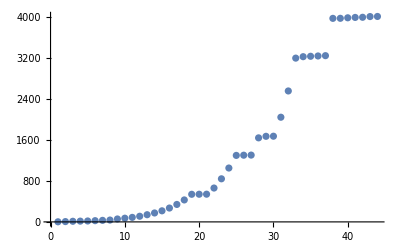

```mathematica
sgnChgs=Map[First,Select[Table[{x,Sign[GInv[x]]==-Sign[GInv[x-1]]},{x,2,5000}],#[[2]]===True&]]
ListPlot[sgnChgs]
```